```mathematica
Quit[];
```

```mathematica
Get["E:\\Data09\\mathematica control system\\Mathematica\\include.m"];
Include/@{"..\\LabVIEW\\LabVIEW.m","Data.nb","Fit.nb","Sequence.nb",(*"Sequencer.nb",*)(*"SerialDevices.nb",*)"PhononNumberFit.nb","Wave.nb",(*"PreDefinedFunctions.nb",*)"APP.nb","GUI.nb"(*,"TCPIPDevices.nb"*)};
```

```mathematica
sequencer=GetAllCtrls@"E:\\control procedure\\LabVIEW\\Sequencer\\Sequencer.vi";
(*awg=GetAllCtrls@"D:\\LabVIEW\\SpectrumAWG\\SpectrumAWG.vi";
DDSBox=GetAllCtrls@"D:\\app\\DDS\\DDSBox\\DDSBox.vi";*)
(*CurrentSource=SerialOpen["COM13",9600,8,1];
linetrigger=SerialOpen["COM21",9600,8,1];
Quiet@Close[$redpitdaya];
$redpitaya=SocketConnect["192.168.32.110:5000"];
Laser370Connect[]
Laser935Connect[]
Laser399Connect[]
InitializeCCD[]*)
```

```mathematica
CtrlGetValue[sequencer@"Sweep"]
```

False

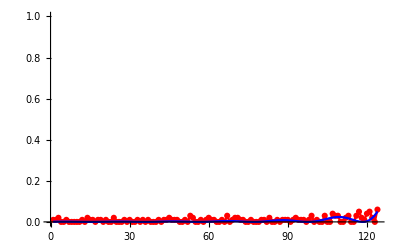

138.399

```mathematica
DriveFrequencyFit[Average["TimeScan-20210323085918",S1[]],True]
```

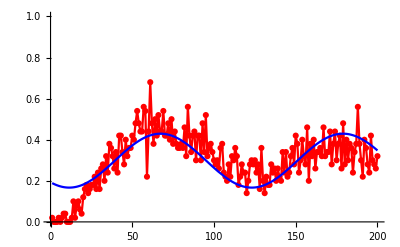

55.8507

```mathematica
RabiFrequencyFit[Average["TimeScan-20210408151214",S1[]],True]
```

```mathematica
DateString[]
```

2021-03-06 21:12:13

## Docked Buttons

```mathematica
(*switch变量原来是用来存储370强光开关电压的，临时拿来做vva控制电压存储*)
SetOptions[EvaluationNotebook[],DockedCells->Cell[BoxData[ToBoxes[Grid[{{Button["CCD",CreateDialog[emccdGUI[],WindowMargins->{{100,Automatic},{Automatic,60}},WindowTitle->"Andor iXon",WindowFrameElements->{"CloseBox","ZoomBox","MinimizeBox"}],BaseStyle->{"GenericButton",20,Bold}],
DynamicModule[{indicator="CCDView",v=-3.3},EventHandler[Button[Dynamic@indicator,Null,BaseStyle->{"GenericButton",20,Bold}],{"MouseDown":>(indicator=indicator/.{"CCDView"->"PMTView","PMTView"->"CCDView"};v=v/.{-3.3->0,0->-3.3};flipper=v;VoltageWriter@WriteSingleSample[True,VoltageList])}]],
ActionMenu["RFCtrl",{"Trap RF Ctrl":>CreateDialog[rfGUI[],WindowMargins->{{Automatic,100},{Automatic,50}},WindowTitle->"RF Control",WindowFrameElements->{"CloseBox","ZoomBox","MinimizeBox","ResizeArea"}],"Raman PLL RF Ctrl":>CreateDialog[RamanPLLGUI[],WindowMargins->{{Automatic,100},{Automatic,50}},WindowTitle->"RF Control",WindowFrameElements->{"CloseBox","ZoomBox","MinimizeBox","ResizeArea"}],"...":>CreateDialog[{}]},Appearance->"PopupMenu",BaseStyle->{"GenericButton",20,Bold}],DynamicModule[{indicator="370Off",v=0},EventHandler[Button[Dynamic@indicator,Null,BaseStyle->{"GenericButton",20,Bold}],{"MouseDown":>(indicator=indicator/.{"370Off"->"370On","370On"->"370Off"};v=v/.{0->1,1->0};rpDigitalOut[$redpitaya,"7_N",v](*switch=v;VoltageWriter@WriteSingleSample[True,VoltageList]*))}]],Button["Find370LP",CreateDialog[{TextCell["Enter a target cooling counts:"],InputField[Dynamic[ccounts],Number,FieldHint->"Do not exceed 14"],DefaultButton[DialogReturn@CheckLockPoint[ccounts]]},WindowMargins->{{1000,Automatic},{Automatic,60}}],BaseStyle->{"GenericButton",15,Bold}],Button["Trigger",CreateDialog[Column[{TextCell["Delay time set:",FontSize->12],Row[{Button["reset",delaytime=0;tstep=100],Spacer[10],Button["save",TriggerSave[linetrigger];]}],Row[{Panel[EventHandler[InputField[Dynamic[delaytime],ImageSize->{50,20},FrameMargins->Tiny],{"UpArrowKeyDown":>(delaytime=delaytime+tstep;SetTriggerDelayTime[linetrigger,IntegerPart@delaytime];),"DownArrowKeyDown":>(delaytime=delaytime-tstep;SetTriggerDelayTime[linetrigger,IntegerPart@delaytime];),"LeftArrowKeyDown":>(If[tstep<1000,tstep=tstep*10]),"RightArrowKeyDown":>(If[tstep>1,tstep=tstep/10])}],FrameMargins->Tiny],Panel[Dynamic[ToString[tstep]<>" ms"],FrameMargins->Small,ImageSize->{60,30}]}]}],WindowMargins->{{Automatic,300},{Automatic,60}},WindowTitle->"Trigger"],BaseStyle->{"GenericButton",15,Bold}]},{DynamicModule[{indicator="355Off",v=False},EventHandler[Button[Dynamic@indicator,Null,BaseStyle->{"GenericButton",20,Bold}],{"MouseDown":>(indicator=indicator/.{"355Off"->"355On","355On"->"355Off"};v=v/.{False->True,True->False};CtrlSignalValue[sequencer@"Sweep",False];SequenceFile@DataPath@"Sequence/protection.seq";CtrlSignalValue[sequencer@"Sweep",v])}]],DynamicModule[{indicator="Start",v=True},EventHandler[Button[Dynamic@indicator,Null,BaseStyle->{"GenericButton",20,Bold}],{"MouseDown":>(indicator=indicator/.{"Start"->"Stop","Stop"->"Start"};v=v/.{True->False,False->True};symbol=v)}]],
(*ActionMenu["LaserCtrl",{"laser 370/935/399":>laserGUI[],"370 signal display":>laserSignalDispGUI[laser370]},BaseStyle->{"GenericButton",20,Bold},Appearance->"PopupMenu"]*)Button["LaserCtrl",CreateDialog[laserGUI[],WindowMargins->{{400,Automatic},{Automatic,60}},WindowTitle->"Laser 370/935/399",WindowFrameElements->{"CloseBox","ZoomBox","MinimizeBox","ResizeArea"}],BaseStyle->{"GenericButton",20,Bold}],ActionMenu["Tasks",{"Before SBC":>(symbol=True;WaveFile0@DataPath@"Wave\\Null.csv";openCloseTaggedCell[EvaluationNotebook[],"Before SBC",Open];
SelectionMove[Cells[CellTags->"Before SBC"][[1]],All,Cell];),"SBC":>(symbol=True;
WaveFile0@DataPath@"Wave\\Null.csv";
CtrlSignalValue[sequencer@"Repeats",200];CtrlSignalValue[sequencer@"Trigger",False];CtrlSignalValue[sequencer@"Count or State",1];openCloseTaggedCell[EvaluationNotebook[],"SBC",Open];
SelectionMove[Cells[CellTags->"SBC"][[1]],All,Cell];),"Trap freq measure":>(symbol=True;
WaveFile0@DataPath@"Wave\\Null.csv";
CtrlSignalValue[sequencer@"Repeats",200];CtrlSignalValue[sequencer@"Trigger",False];CtrlSignalValue[sequencer@"Count or State",1];openCloseTaggedCell[EvaluationNotebook[],"Trap frequency measurement",Open];
SelectionMove[Cells[CellTags->"Trap frequency measurement"][[1]],All,Cell];),
"Spin dependent force":>(symbol=True;
WaveFile0@DataPath@"Wave\\Null.csv";
CtrlSignalValue[sequencer@"Repeats",200];CtrlSignalValue[sequencer@"Trigger",False];CtrlSignalValue[sequencer@"Count or State",1];openCloseTaggedCell[EvaluationNotebook[],"spin dependent force",Open];
SelectionMove[Cells[CellTags->"spin dependent force"][[1]],All,Cell];),"QRM Calibrate":>(symbol=True;
WaveFile0@DataPath@"Wave\\Null.csv";openCloseTaggedCell[EvaluationNotebook[],"QRM Calibrate",Open];
SelectionMove[Cells[EvaluationNotebook[],CellTags->"QRM Calibrate"][[1]],All,Cell];),
"QRM Full Calibrate":>(WaveFile0@DataPath@"Wave\\Null.csv";QRModelFullCalibrate[];),"T/P Monitor":>(NotebookOpen["E:\\member\\cml_maverick\\TemperaturePressureMonitor.nb"];)
},BaseStyle->{"GenericButton",20,Bold},Appearance->"PopupMenu"],Button["InitAWG",WaveFile0@DataPath@"Wave\\Null.csv",BaseStyle->{"GenericButton",15,Bold}],Button["T/P Monitor",CreateDialog[{Row[{Style["WLM T(^oC):",Bold],Panel[Dynamic[Refresh[NumberForm[GetWLMTemperature[],{6,4}],UpdateInterval->1]],ImageSize->{55,Automatic},FrameMargins->Tiny]}],Row[{Style["WLM P(mbar):",Bold],Panel[Dynamic[Refresh[NumberForm[GetWLMPressure[],{6,2}],UpdateInterval->1]],ImageSize->{55,Automatic},FrameMargins->Tiny]}]},WindowMargins->{{900,Automatic},{Automatic,60}},WindowTitle->"T/P Monitor"],BaseStyle->{"GenericButton",15,Bold}]}},Alignment->{Left,Top}]]],"DockedCell"]];
```

# 2021 records

M.- L. Cai

## Fundamental Tasks

### Pumping and detection efficiency

```mathematica
SequenceFile@DataPath@"Sequence\\Pumping.seq";
CtrlSignalValue[sequencer@"Repeats",200];
```

```mathematica
ScanPar["Time",2,{0.1,20,0.5}]
```

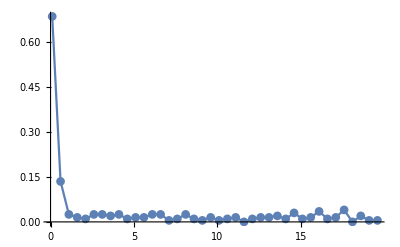

```mathematica
DataPlot[Average["TimeScan-20190929153418",S1[]],PlotRange->All]
```

```mathematica
SequenceFile@DataPath@"Sequence\\Detection.seq";
CtrlSignalValue[sequencer@"Repeats",200];
```

```mathematica
ScanPar["Time",2,{0.1,800,20}]
```

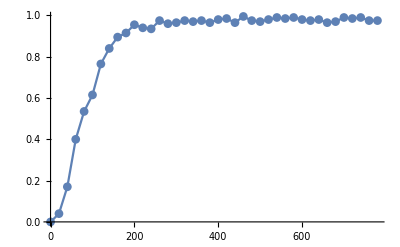

```mathematica
DataPlot[Average["TimeScan-20190929153521",S1[]],PlotRange->All]
```

### 370 frequency variation measured by counts

```mathematica
SequenceFile@DataPath@"Sequence\\Cooling.seq";
CtrlSignalValue[sequencer@"Repeats",1000];
CtrlSignalValue[sequencer@"Count or State",0];
```

```mathematica
ClearAll[T1,CountsData];CountsData={};T1=2000;
```

```mathematica
Dynamic[ListPlot[CountsData,PlotStyle->PointSize[Medium]]]
totaltime1=AbsoluteTiming[Table[CtrlSignalValue[sequencer@"Data",True];
While[CtrlGetValue@sequencer@"Data"===True,Pause[0.1]];AppendTo[CountsData,{i,CtrlGetValue[sequencer@"Average Plot"][[1]]}],{i,T1}]][[1]];
```

$Aborted

```mathematica
totaltime1/60
Mean@DeleteCases[CountsData,_?(#[[2]]<10&)][[All,2]]
StandardDeviation@DeleteCases[CountsData,_?(#[[2]]<10&)][[All,2]]
```

12.9014

0.983245

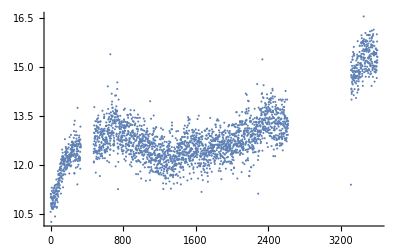

```mathematica
ListPlot@DeleteCases[CountsData,_?(#[[2]]<10&)]
```

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>ToString[totaltime1/60]<>" min detection state variation"<>DateString[{"Hour","Minute","Second"}]<>".csv",CountsData];
```

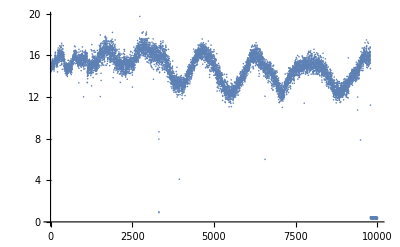

```mathematica
ListPlot@Import["D:\\Data\\2019\\201908\\20190822\\longterm cooling florescence variation.csv"]
```

### Ion position variation monitor

```mathematica
ClearAll[Tp,PositionData];PositionData={};Tp=50;
```

```mathematica
totaltimep=AbsoluteTiming[Do[AppendTo[PositionData,IonPositionFit[Partition[NETObjectToExpression@buf,256][[100;;150,80;;100]],100,80]],Tp]][[1]];
```

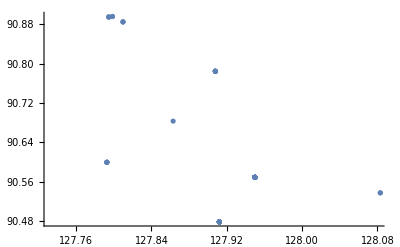

```mathematica
ListPlot[PositionData]
```

```mathematica
StandardDeviation@PositionData[[All,1]]
```

0.831295

```mathematica
Mean@PositionData[[All,1]]
```

125.919

```mathematica
StandardDeviation@PositionData[[All,2]]
```

0.676714

```mathematica
Mean@PositionData[[All,2]]
```

119.984

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>ToString[totaltimep/60]<>" min ion position monitor "<>DateString[{"Hour","Minute","Second"}]<>".csv",PositionData];
```

```mathematica
cameradata=CtrlGetValue@CCD@"Image";
```

```mathematica
maxpoint=Position[cameradata,Max@(Max/@cameradata)][[1]];
```

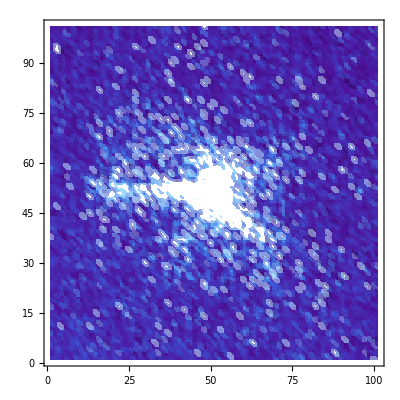

```mathematica
ListDensityPlot[Flatten[MapIndexed[{#2⟦1⟧,#2⟦2⟧,#1}&,cameradata[[maxpoint[[1]]-50;;maxpoint[[1]]+50,maxpoint[[2]]-50;;maxpoint[[2]]+50]],{2}],1],ColorFunction->"DeepSeaColors"]
```

### Fundamental tests by microwave:

#### microwave coherence measurement:

```mathematica
(*the ad9910(used to mix with LO) freq is fixed at 187MHz,Rf reference is tunable*)
```

```mathematica
SequenceFile["Sequence/Horn.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[5],"Zero"[1],"Horn"[6],"Detection"[300,1,1],"Zero"[1]}];
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Profile",0];
CtrlSignalValue[DDSBox@"Amplitude",1];
```

```mathematica
ScanPar["AWG2",1,{186.6,187.4,0.02}]
```

AWG2Scan-20210306170422

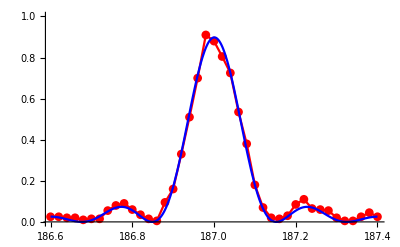

187.001

```mathematica
MWCarr=DriveFrequencyFit[Average["AWG2Scan-20210306170422",S1[]],True]
```

```mathematica
SequenceFile["Sequence/Horn.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[5],"Zero"[1],"Horn"[10],"Detection"[300,1,1],"Zero"[1]}];
CtrlSignalValue[sequencer@"Count or State",1];
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Profile",0];
CtrlSignalValue[DDSBox@"Frequency (MHz)",MWCarr];
(*CtrlSignalValue[sequencer@"Item","AD9910"];*)
```

```mathematica
MWCarrPiFile=ScanPar["Time",4,{0.1,50,.8}];
```

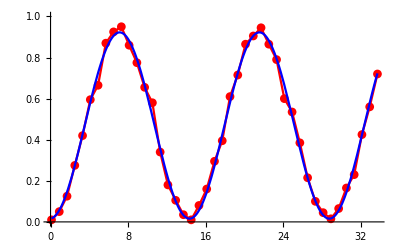

7.20363

```mathematica
MWCarrPi=RabiFrequencyFit[Average[MWCarrPiFile,S1[]],True]
```

Bright state fidelity=0.95

Dark state fidelity=0.01

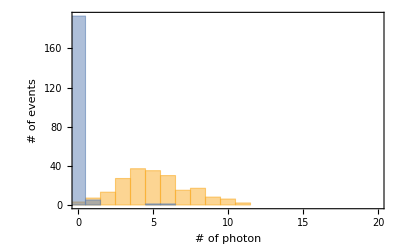
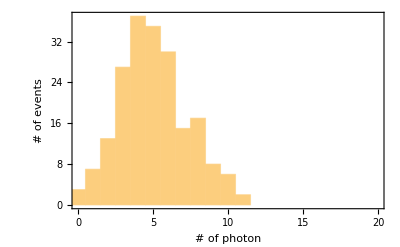
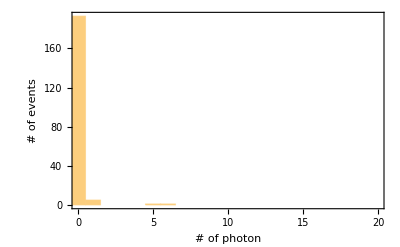

```mathematica
StateOverlap[MWCarrPiFile]
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/HornRamsey.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[5],"Zero"[1],"Horn"[MWCarrPi/2],"Zero"[100],"Horn"[MWCarrPi/2],"Detection"[300,1,1],"Zero"[1]}]];
CtrlSignalValue[sequencer@"Repeats",100];
```

```mathematica
MWDetuningFile=ScanPar["Time",5,{0.1,50000,100}];
```

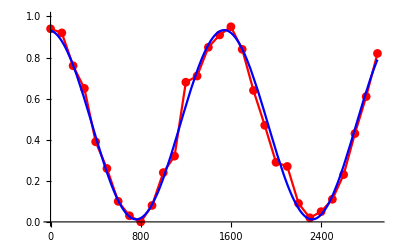

0.000640393

```mathematica
MWDetuning=1/(2RabiFrequencyFit[Average[MWDetuningFile,S1[]],True])
```

```mathematica
MWCarr=MWCarr+MWDetuning
CtrlSignalValue[DDSBox@"Frequency (MHz)",MWCarr];
```

187.001

```mathematica
MWDetuningFile=ScanPar["Time",5,{0.1,100000,1000}];
```

coherence time=305.015ms

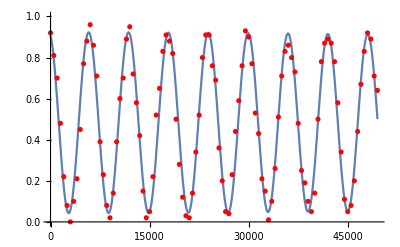

```mathematica
GaussianCoherenceFit[Average["TimeScan-20200726141029",S1[]],10000,5000]
```

coherence time=1128.15ms

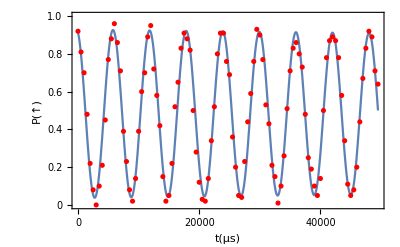

```mathematica
CoherenceTimeFit[Average["TimeScan-20200726141029",S1[]],10000]
```

```mathematica
SequenceFile@DataPath@"Sequence\\Horn.seq";
CtrlSignalValue[sequencer@"Count or State",1];
```

```mathematica
MWZeemanFile=ScanPar["AWG2",1,{178,178.5,0.005}]
```

AWG2Scan-20210130133242

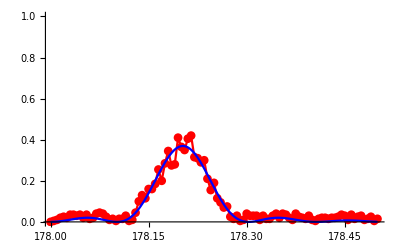

178.202

```mathematica
MWZeemanUp=DriveFrequencyFit[Average[MWZeemanFile,S1[]],True]
```

```mathematica
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Profile",0];
CtrlSignalValue[DDSBox@"Frequency (MHz)",MWZeemanUp];
```

```mathematica
MWZeemanPiFile=ScanPar["Time",4,{0.1,100,2}]
```

TimeScan-20210130133333

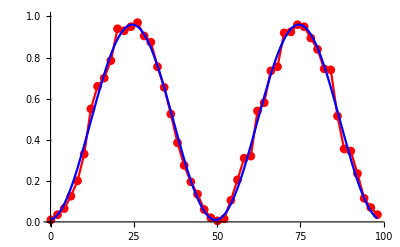

25.004

```mathematica
MWZeemanUpPi=RabiFrequencyFit[Average[MWZeemanPiFile,S1[]],True]
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/HornRamsey.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"Horn"[MWZeemanUpPi/2],"Zero"[100],"Horn"[MWZeemanUpPi/2],"Detection"[300,1,1],"Zero"[1]}]];
```

```mathematica
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Profile",0];
CtrlSignalValue[DDSBox@"Frequency (MHz)",MWZeemanUp-0.004];
```

```mathematica
ZeemanRamseyFile=ScanPar["Time",5,{0.1,1000,20}]
```

TimeScan-20210130133404

coherence time=0.407531ms

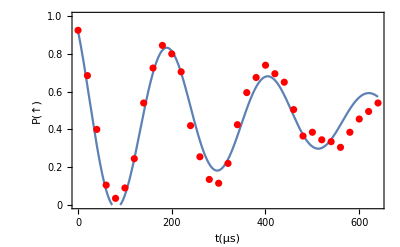

```mathematica
CoherenceTimeFit[Average[ZeemanRamseyFile,S1[]],300,60]
```

```mathematica
SequenceFile@DataPath@"Sequence\\Horn.seq";
CtrlSignalValue[sequencer@"Count or State",1];
```

```mathematica
MWZeemanFile=ScanPar["AWG2",1,{195.6,196,0.003}];
```

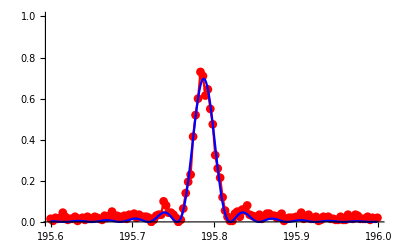

195.787

```mathematica
MWZeemanDown=DriveFrequencyFit[Average[MWZeemanFile,S1[]],True]
```

```mathematica
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Profile",0];
CtrlSignalValue[DDSBox@"Frequency (MHz)",MWZeemanDown];
```

```mathematica
MWZeemanPiFile=ScanPar["Time",4,{0.1,200,5}]
```

TimeScan-20210130133613

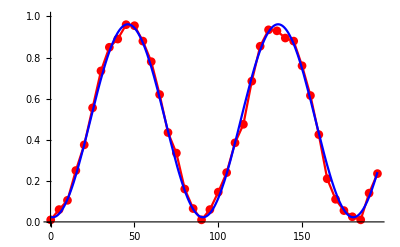

44.8566

```mathematica
MWZeemanDownPi=RabiFrequencyFit[Average[MWZeemanPiFile,S1[]],True]
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/HornRamsey.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"Horn"[MWZeemanDownPi/2],"Zero"[100],"Horn"[MWZeemanDownPi/2],"Detection"[400,1,1],"Zero"[1]}]];
```

```mathematica
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Profile",0];
CtrlSignalValue[DDSBox@"Frequency (MHz)",MWZeemanDown-0.004];
```

```mathematica
ZeemanRamseyFile=ScanPar["Time",5,{0.1,1000,20}]
```

TimeScan-20210130133642

coherence time=0.543729ms

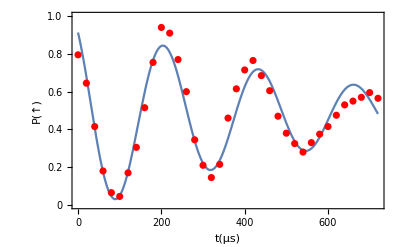

```mathematica
CoherenceTimeFit[Average[ZeemanRamseyFile,S1[]],500]
```

#### Sideband-induced carrier ac Stark shift probed by microwave

```mathematica
SequenceFile@DataPath@"Sequence\\Horn.seq";
CtrlSignalValue[sequencer@"Count or State",1];
CtrlSignalValue[sequencer@"Count or State",1];
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Profile",1];
CtrlSignalValue[DDSBox@"Frequency (MHz)",MWCarr];
CtrlSignalValue[DDSBox@"Amplitude",0.03];
```

```mathematica
MWCarrPiFile=ScanPar["Time",4,{0.1,1000,30}]
```

TimeScan-20210304155948

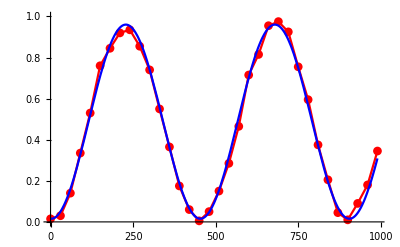

225.708

```mathematica
MWCarrPi=RabiFrequencyFit[Average[MWCarrPiFile,S1[]],True]
```

```mathematica
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{QRMRed+δr,0,amplitude,0,0},{QRMBlue+δb,0,amplitude,0,0},{0,MWCarrPi,0,0,0,"[0 1]"}}]];
CtrlSignalValue[awg@"Row",0];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/acStarkShift calibrate.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[5],"Zero"[1],"AWG"[1],"HornWithRaman"[MWCarrPi+2],"Zero"[1],"Detection"[300,1,1],"Zero"[1]}]];
```

```mathematica
filename=ScanPar["AWG2",1,{186.95,187.05,0.001},True]
```

AWG2Scan-20210130174703

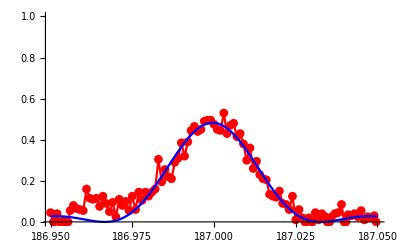

-0.00181727

```mathematica
acStarkShift=DriveFrequencyFit[{Average[filename,S1[]][[All,1]],Average[filename,S1[]][[All,2]]-0.15}ᵀ,True]-MWCarr
```

auto-calibrate:

```mathematica
amplitude=0.05;acStarkShift=0;DataForCarrShift={};
SelectionMove[InputNotebook[],Next,Cell];
```

```mathematica
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{SDFRed-δr,0,amplitude,0,0},{SDFBlue-δb,0,amplitude,0,0},{0,MWCarrPi,0,0,0,"[0 1]"}}]];
CtrlSignalValue[awg@"Row",0];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/acStarkShift calibrate.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"AWG"[1],"HornwithRaman"[MWCarrPi],"Zero"[5],"Detection"[400,1,1],"Zero"[1]}]];
Pause[0.5];
If[amplitude≤0.6,filename=ScanPar["AD9910",0,{173,173.09,0.002},True];
SelectionMove[InputNotebook[],Next,Cell,1];
FrontEndExecute[FrontEndToken["Evaluate"]],Null];
```

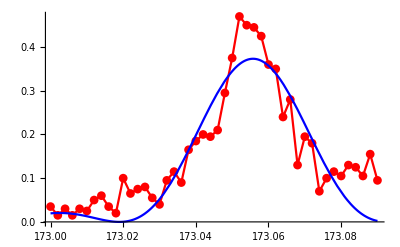

0.0153602

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[amplitude≤.3,offset=0,offset=0.1];
acStarkShift=DriveFrequencyFit[Join[{Average[filename,S1[]][[All,1]],Average[filename,S1[]][[All,2]]-offset}]ᵀ,True]-173.0408
SelectionMove[InputNotebook[],Next,Cell,1];
FrontEndExecute[FrontEndToken["Evaluate"]];
```

```mathematica
AppendTo[DataForCarrShift,{amplitude,acStarkShift}];
amplitude+=0.05;
SelectionMove[InputNotebook[],Previous,Cell,5];
FrontEndExecute[FrontEndToken["Evaluate"]];
```

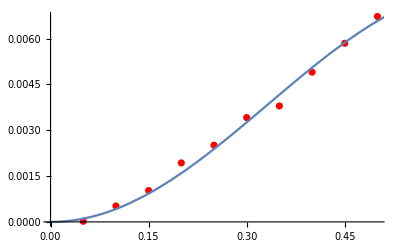

FittedModel[0.00768339 Sin[2.36445 x$893291]^2]

```mathematica
freqc=CalibrateForCarrierShift[DataForCarrShift[[2;;11]],δr,δb]
```

#### Longterm variation of Zeeman level:

```mathematica
SequenceFile@DataPath@"Sequence\\Horn.seq";
CtrlSignalValue[sequencer@"Count or State",1];
```

```mathematica
MWZeemanFile=ScanPar["AD9910",0,{180.75,180.9,0.004}]
```

AD9910Scan-20200114181705

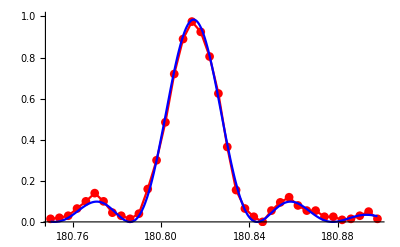

180.815

```mathematica
MWZeemanUp=DriveFrequencyFit[Average[MWZeemanFile,S1[]],True]
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/HornRamsey.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"Horn"[MWZeemanUpPi/2],"Zero"[1],"Horn"[MWZeemanUpPi/2],"Detection"[400,1,1],"Zero"[1]}]];
CtrlSignalValue[sequencer@"Item","AD9910"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",MWZeemanUp];
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/HornRamsey.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"Horn"[MWZeemanUpPi/2],"Zero"[50],"Horn"[MWZeemanUpPi/2],"Detection"[400,1,1],"Zero"[1]}]];
CtrlSignalValue[sequencer@"Trigger",False];
```

```mathematica
ZeemanRamseyfile=ScanPar["AD9910",0,{MWZeemanUp-0.01,MWZeemanUp+detuning+0.01,0.0008}];
```

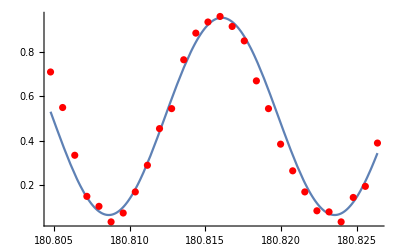

{0.444163,0.510192,180.816}

```mathematica
parameter=RamseyFrequencyFit[Average[ZeemanRamseyfile,S1[]],50+MWZeemanUpPi/2]
```

```mathematica
FreqSet=180.813;
CtrlSignalValue[sequencer@"Item","AD9910"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",FreqSet];
```

```mathematica
ClearAll[ZeemanLevelRawDataTable,T3];T3=3000;ZeemanLevelRawDataTable={};
```

```mathematica
Dynamic@ListPlot[ZeemanLevelRawDataTable,PlotRange->All,PlotStyle->PointSize[Medium]]
totaltime3=AbsoluteTiming[Table[CtrlSignalValue[sequencer@"Data",True];
While[CtrlGetValue@sequencer@"Data"===True,Pause[0.1]];AppendTo[ZeemanLevelRawDataTable,{i,CtrlGetValue[sequencer@"Average Plot"][[1]]}],{i,T3}]][[1]];
```

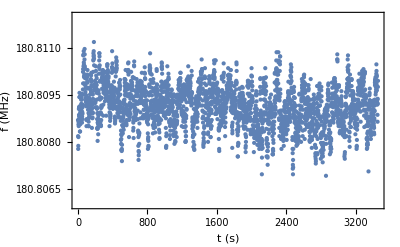

```mathematica
ListPlot[DataTable=Table[{(i-1)totaltime3/T3,FreqSet-ArcCos[(ZeemanLevelRawDataTable[[i,2]]/100-parameter[[2]])/parameter[[1]]]/(2Pi (50+MWZeemanUpPi/2))},{i,1,T3}],PlotRange->{All,{180.806,180.812}},PlotStyle->PointSize[Medium],Frame->True,Axes->False,FrameLabel->{"t (s)","f (MHz)"},LabelStyle->{Black,12}]
```

```mathematica
Mean@DataTable[[All,2]]
```

180.809

```mathematica
StandardDeviation@DataTable[[All,2]]
```

0.000659634

```mathematica
Max@DataTable[[All,2]]-Min@DataTable[[All,2]]
```

0.00425153

```mathematica
data=(DataTable[[All,2]]-173.0408)/1.4;
```

```mathematica
StandardDeviation@data
```

0.000471167

```mathematica
Mean@data
```

5.54882

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>ToString[totaltime3/60]<>" min variation of Zeeman level raw data.csv",ZeemanLevelRawDataTable];
```

### Fundamental tests by Raman laser:

#### Micro-motion measured by fluorescence and Raman

```mathematica
SequenceFile["Sequence/Raman.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[5],"Gap"[0.5],"Raman3"[20],"Detection"[300,1,1],"Zero"[1]}];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",31.465+187.0(*micromotion freq*)];
```

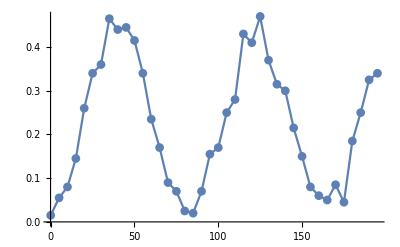

```mathematica
DataPlot[Average["TimeScan-20200808131419",S1[]]]
```

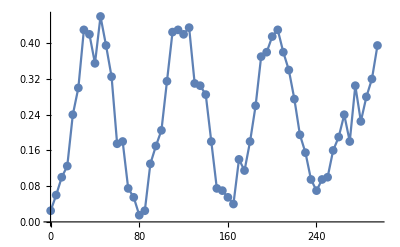

```mathematica
DataPlot[Average["TimeScan-20200808131836",S1[]]]
```

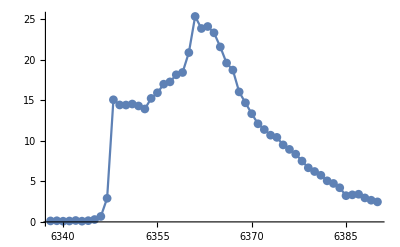

```mathematica
DataPlot[Average["WLMScan-20190613203436",C1[]]](*good compensation of MM,wavelength vs cooling counts*)
```

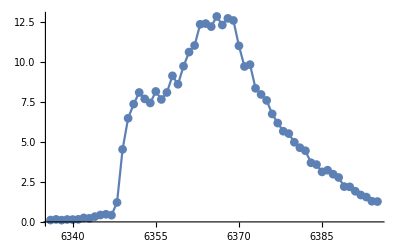

```mathematica
DataPlot[Average["WLMScan-20190613204100",C1[]]](*good compensation of MM,wavelength vs detection counts*)
```

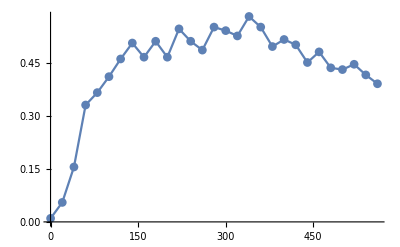

```mathematica
DataPlot[Average["TimeScan-20190610202025",S1[]]](*good compensation of MM*)
```

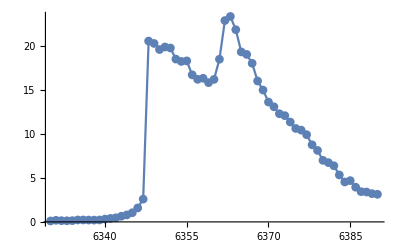

```mathematica
DataPlot[Average["WLMScan-20190613205940",C1[]]](*bad compensation of MM wavelength vs cooling counts*)
```

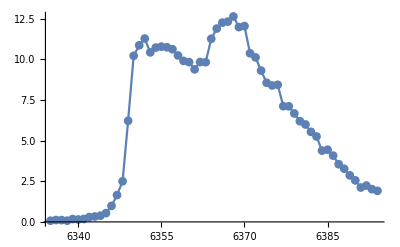

```mathematica
DataPlot[Average["WLMScan-20190613205547",C1[]]](*bad compensation of MM wavelength vs detection counts*)
```

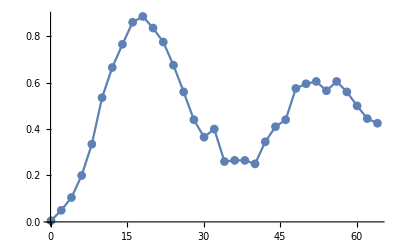

```mathematica
DataPlot[Average["TimeScan-20190613210346",S1[]]](*bad compensation of MM*)
```

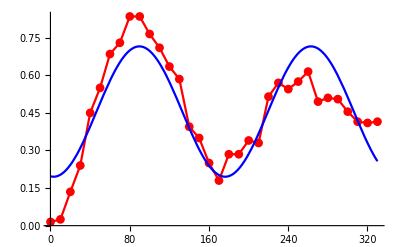

86.5688

```mathematica
RabiFrequencyFit[Average["TimeScan-20190523151238",S1[]],True](*micromotion Rabi without well elimination of the micromotion*)
```

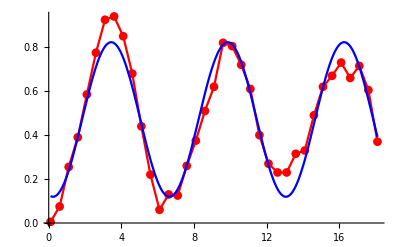

3.20595

```mathematica
RabiFrequencyFit[Average["TimeScan-20190530212244",S1[]],True](*carrier before SBC with well eliminated micromotion*)
```

#### Single Raman beam excitation

```mathematica
SequenceFile["Sequence/Raman.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[5],"Zero"[1],"Raman3"[4],"Detection"[300,1,1],"Zero"[1]}];
```

```mathematica
singleBeamCarrFile=ScanPar["AOM",0,{186.8,187.2,0.01}]
```

AOMScan-20210222174356

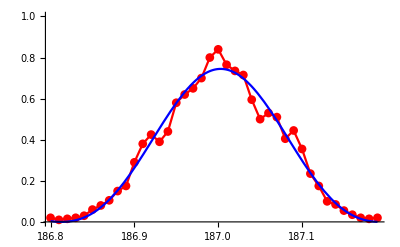

187.003

```mathematica
singleBeamCarr=DriveFrequencyFit[Average[singleBeamCarrFile,S1[]],True]
```

```mathematica
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",singleBeamCarr];
SequenceFile["Sequence/Raman.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[5],"Zero"[1],"Raman3"[5],"Detection"[300,1,1],"Zero"[1]}];
```

```mathematica
singleBeamCarrPiFile=ScanPar["Time",4,{.1,20,0.5}]
```

TimeScan-20210222175018

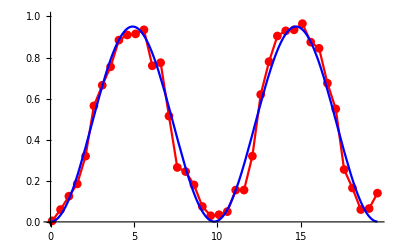

4.89538

```mathematica
singleBeamCarrPi=RabiFrequencyFit[Average[singleBeamCarrPiFile,S1[]],True]
```

```mathematica
SequenceFile["Sequence/Raman.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[5],"Zero"[1],"Raman3"[singleBeamCarrPi/2],"Zero"[1],"Raman3"[singleBeamCarrPi/2],"Detection"[300,1,1],"Zero"[1]}];
```

```mathematica
ScanPar["Time",5,{.1,10000,100}]
```

TimeScan-20210222175204

coherence time=332.928ms

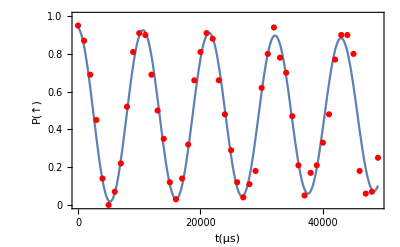

```mathematica
fig=CoherenceTimeFit[Average["TimeScan-20210222175645",S1[]],50000]
```

```mathematica
Export["E:\\member\\cml_maverick\\lab figure\\Single_Raman_beam_Ramsey.png",fig,ImageResolution->400]
```

E:\member\cml_maverick\lab figure\Single_Raman_beam_Ramsey.png

#### Spot size estimation by Raman laser

```mathematica
SequenceFile["Sequence/Raman.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[5],"Zero"[1],"Raman3"[1],"Detection"[300,1,1],"Zero"[1]}];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",173.041];
```

```mathematica
SpotSizeRabiFile={};locate=1.1;repeats=3;end=30;step=1.5;
```

```mathematica
Button[Dynamic[locate],locate+=0.04;SelectionMove[EvaluationNotebook[],Next,Cell];FrontEndTokenExecute["Evaluate"],BaseStyle->{"GenericButton",20,Bold}]
```

```mathematica
AppendTo[SpotSizeRabiFile,{locate,Table[SpotSizeFile=ScanPar["Time",4,{0.1,end,step}];While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];If[symbol,SpotSizeRabi=RabiFrequencyFit[Average[SpotSizeFile,S1[]]];
end=3*SpotSizeRabi;step=SpotSizeRabi/8;
1/(2SpotSizeRabi),Abort[]],repeats]}];
SelectionMove[EvaluationNotebook[],Previous,Cell,2];
```

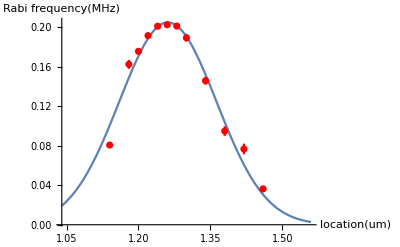

Fitted spot radius = 14.3945um

1.26135

```mathematica
SpotSizeFitByRaman[SpotSizeRabiFile]
```

```mathematica
1.46-1.261346
```

0.198654

#### Raman coherence measurement:

```mathematica
SequenceFile["Sequence/Raman.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[5],"Zero"[1],"Raman3"[1],"Detection"[300,1,1],"Zero"[1]}];
CtrlSignalValue[sequencer@"Count or State",1];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",Carr];
```

```mathematica
CarrFile=ScanPar["Time",4,{0.1,10,0.3}];
```

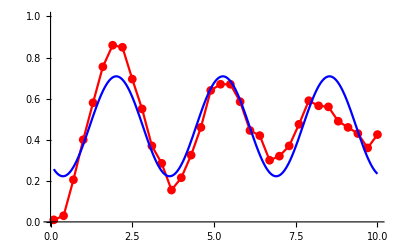

1.63057

```mathematica
CarrPi=RabiFrequencyFit[Average[CarrFile,S1[]],True]
```

```mathematica
RamanCarr=Carr;
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/RamanCoherence.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[5],"Zero"[1],"Raman3"[CarrPi/2+0.2],"Zero"[1],"Raman3"[CarrPi/2+0.2],"Detection"[300,1,1],"Zero"[1]}]];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",RamanCarr];
```

```mathematica
(*CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/RamanCoherence.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[5],"Zero"[1],"AWG"[1],"Raman"[8002],"Detection"[300,1,1],"Zero"[1]}]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Ramsey.csv",{{173.041,CarrPi/2,1,0,0},{0,1,0,0,0},{173.041,CarrPi/2,1,1.5(*绕y轴转*),0}}]];
CtrlSignalValue[awg@"Row",1];*)
```

```mathematica
RamanDetuningFile=ScanPar["Time",5,{0.1,10000,200}];
```

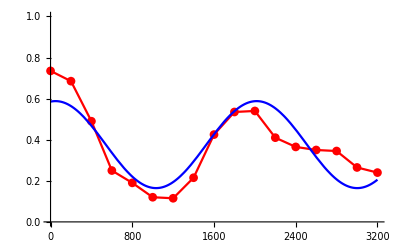

0.000507948

```mathematica
RamanDetuning=1/(2RabiFrequencyFit[Average[RamanDetuningFile,S1[]],True])
```

```mathematica
RamanCarr=RamanCarr-RamanDetuning
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",RamanCarr];
```

187.

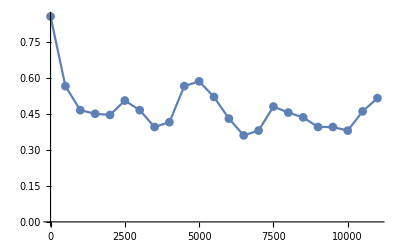

```mathematica
DataPlot["TimeScan-20191031111258",S1[],PlotRange->All](*when the laser purifying is on, the Raman coherence is ruined*)
```

coherence time=4.69617ms

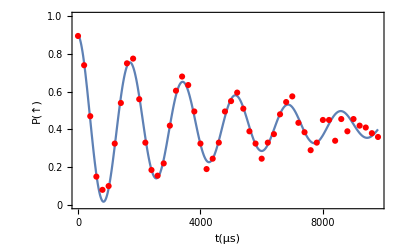

```mathematica
fig=CoherenceTimeFit[Average["TimeScan-20210223165834",S1[]],1000](*bad case may be due to optic path fluctuation*)
```

coherence time=43.7472ms

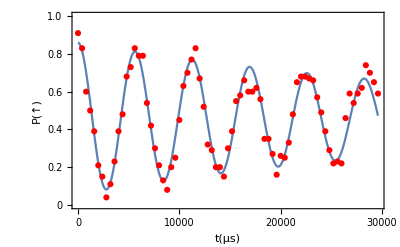

```mathematica
fig=CoherenceTimeFit[Average["TimeScan-20210223193253",S1[]],5000](*good case*)
```

coherence time=33.1413ms

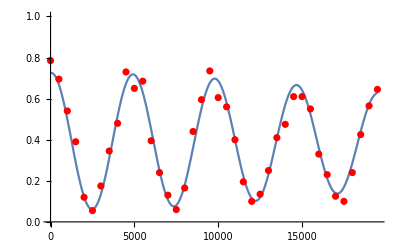

```mathematica
GaussianCoherenceFit[Average["TimeScan-20200114160546",S1[]],5000,2000]
```

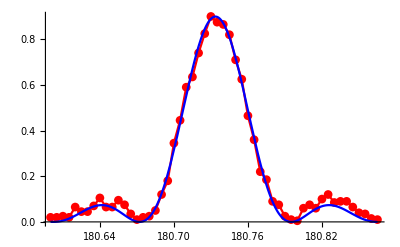

180.734

```mathematica
DriveFrequencyFit[Average["AOMScan-20190531134215",S1[]],True](*Zeeman +1 with Raman*)
```

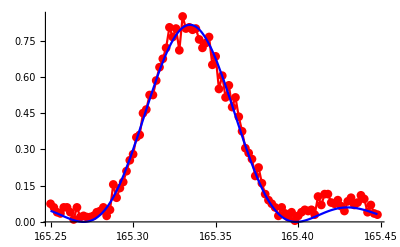

165.334

```mathematica
DriveFrequencyFit[Average["AOMScan-20190531151008",S1[]],True](*Zeeman -1 with Raman*)
```

```mathematica
173.047-165.334
```

7.713

```mathematica
180.734-173.047
```

7.687

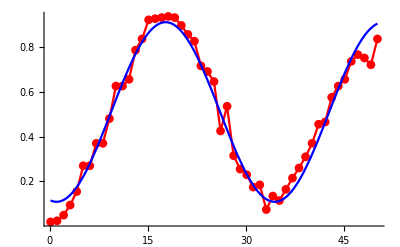

16.6772

```mathematica
RabiFrequencyFit[Average["TimeScan-20190531134344",S1[]],True](*Zeeman +1 with Raman*)
```

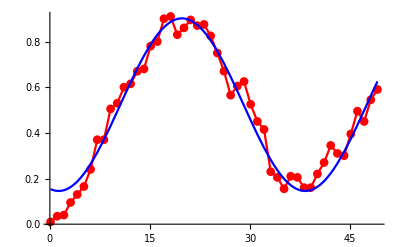

18.4695

```mathematica
RabiFrequencyFit[Average["TimeScan-20190531151150",S1[]],True](*Zeeman -1 with Raman*)
```

#### Raman T2Echo

```mathematica
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",173.041];
```

```mathematica
ClearAll[T2Echo];
T2Echo[range_List,Pitime_]:=Module[{file=NewData["T2Echo"<>"-"],data={},plot={},counts},SequencerAxis@@range;CtrlSignalValue[sequencer@"Repeats",100];CtrlSignalValue[sequencer@"Count or State",1];Table[CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/T2Echo.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"Raman3"[Pitime/2],"Zero"[t/2],"Raman3"[Pitime],"Zero"[t/2],"Raman3"[Pitime/2],"Detection"[400,1,1],"Zero"[1]}]];Pause[1];counts=SequencerCounts[];AppendTo[data,{t,counts}];
AppendTo[plot,{t,Mean@ToState@counts}],{t,range[[1]],range[[2]],range[[3]]}];{Each[plot,{#1,#2}&],ExportData[file,{"C"-><|"Channel"->{1}|>,"X"->List/@data⟦All,1⟧,"Y_Count"->data⟦All,2⟧}]}];
```

```mathematica
datafile=T2Echo[{0.1,20000,500},CarrPi][[2]];
```

### Before SBC

```mathematica
SequenceFile["Sequence/Raman.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[5],"Gap"[0.5],"Raman4"[1],"Detection"[300,1,1],"Zero"[1]}];
CtrlSignalValue[sequencer@"Count or State",1];
CtrlSignalValue[sequencer@"Repeats",200];
(*CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",173.05];*)
CtrlSignalValue[DDSBox@"Channel",0];
CtrlSignalValue[DDSBox@"Profile",1];
CtrlSignalValue[DDSBox@"Frequency (MHz)",Carr];
CtrlSignalValue[DDSBox@"Amplitude",Raman2Amp];
```

```mathematica
Raman2Amp=0.9
```

0.9

```mathematica
ScanPar["AWG2",1,{186.,188.,0.04}]
```

AWG2Scan-20210130193032

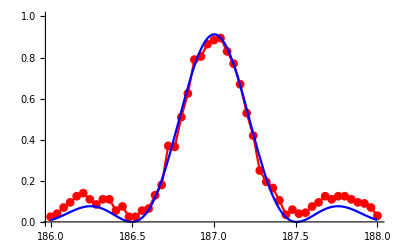

187.00183

```mathematica
Carr=SetAccuracy[DriveFrequencyFit[Average["AWG2Scan-20210130193032",S1[]],True],6](*Raman*)
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/Raman.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[5],"Gap"[0.5],"Raman2"[1],"Detection"[300,1,1],"Zero"[1]}]];
(*CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",Carr];*)
CtrlSignalValue[sequencer@"Repeats",200];
CtrlSignalValue[sequencer@"Count or State",1];
CtrlSignalValue[DDSBox@"Frequency (MHz)",Carr];
```

```mathematica
CarrFile=ScanPar["Time",4,{0.1,10,0.3},True]
```

TimeScan-20210223151235

Average phonon number=32.7027

η=0.0804856

Carrier Rabi rate=0.307506MHz

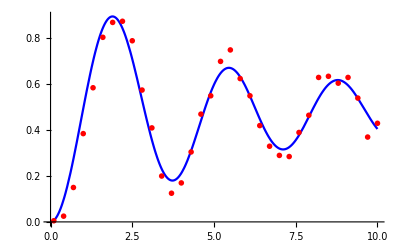

1.62599

```mathematica
CarrPi=CarrierRabiDecay[Average[CarrFile,S1[]],10,100(*phonon cutoff*)]
```

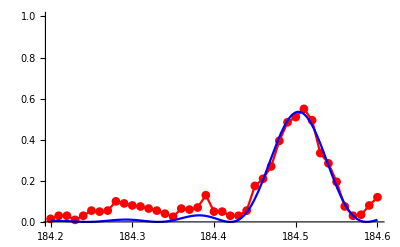

184.503

```mathematica
RedX=DriveFrequencyFit[Average["AWG2Scan-20210108154038",S1[]],True]
```

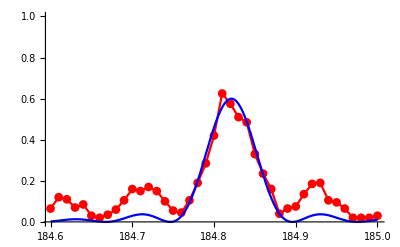

184.821

```mathematica
RedY=DriveFrequencyFit[Average["AWG2Scan-20210108154124",S1[]],True]
```

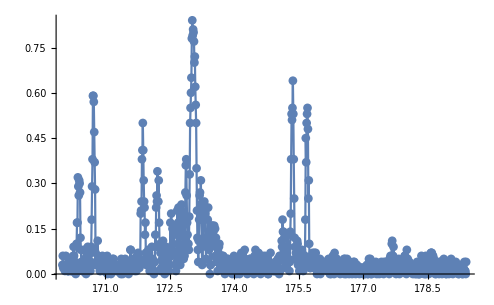

```mathematica
DataPlot[Average["AOMScan-20190527145546",S1[]],PlotRange->All]
```

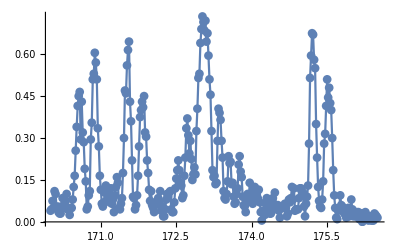

```mathematica
DataPlot[Average["AWG2Scan-20201013165126",S1[]],PlotRange->All]
```

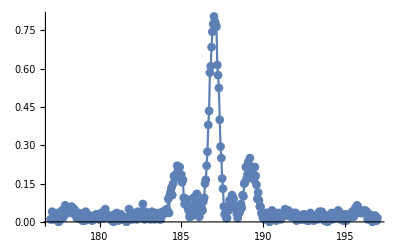

```mathematica
DataPlot[Average["AWG2Scan-20210223204250",S1[]],PlotRange->All]
```

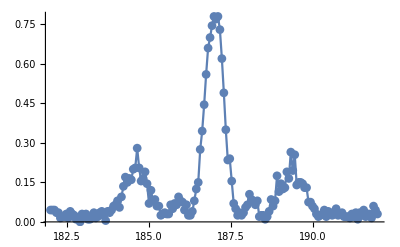

```mathematica
DataPlot[Average["AWG2Scan-20210223204754",S1[]],PlotRange->All]
```

### SBC

```mathematica
n=40;
m=40;
η1=0.08;
η2=0.1;
RedX=184.7;
RedY=185;
RedXPi=1.5/η1;
RedYPi=1.5/η2;
Raman2Amp=1;
```

```mathematica
If[symbol,If[NumberQ@RedXPi,SequenceFile["Sequence/SBCooling.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"Gap"[0.5],"Raman4"[10]}]],Abort[]];
CtrlSignalValue[DDSBox@"Channel",0];
CtrlSignalValue[DDSBox@"Profile",0];
If[NumberQ@RedX,CtrlSignalValue[DDSBox@"Frequency (MHz)",RedX];CtrlSignalValue[DDSBox@"Amplitude",Raman2Amp],Abort[]];
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Profile",0];
If[NumberQ@RedY,CtrlSignalValue[DDSBox@"Frequency (MHz)",RedY];CtrlSignalValue[DDSBox@"Amplitude",Raman2Amp],Abort[]];
If[NumberQ@Carr,
CtrlSignalValue[DDSBox@"Channel",0];CtrlSignalValue[DDSBox@"Profile",1];
CtrlSignalValue[DDSBox@"Frequency (MHz)",Carr];
CtrlSignalValue[DDSBox@"Amplitude",Raman2Amp],Abort[]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,Pause[0.5];
CarrFile=ScanPar["Time",2+4(n+m)+1,{0.1,7,.2}];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

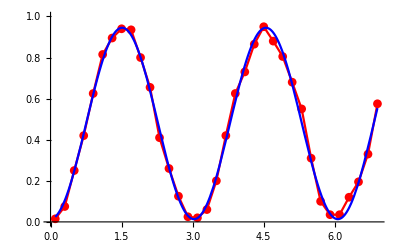

1.51757

0.329473

```mathematica
If[symbol,
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
CarrPi=RabiFrequencyFit[Average[CarrFile,S1[]],True];
Print[CarrPi];
Print[1/(2CarrPi)];
If[NumberQ@CarrPi,
CtrlSignalValue[DDSBox@"Channel",0];
CtrlSignalValue[DDSBox@"Profile",0];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"Gap"[0.5],"Raman4"[CarrPi],"Gap"[0.5],"Raman1"[RedXPi]}]],Abort[]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,
CtrlSignalValue[awg@"Duration (us)",CarrPi];
Pause[0.5];
RedXFile=ScanPar["AWG2",1,{184.45,184.7,0.006}];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

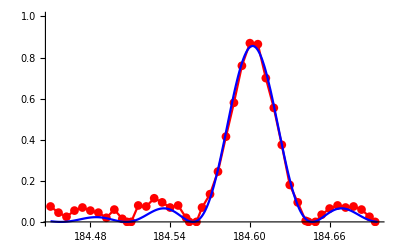

184.60207

2.39976

```mathematica
If[symbol,While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
RedX=DriveFrequencyFit[Join[{(Average[RedXFile,S1[]]ᵀ)[[1]]},{(0.9-(Average[RedXFile,S1[]]ᵀ)[[2]])}]ᵀ,True];(*red sideband x*)
Print[SetAccuracy[RedX,6]];
Print[Carr-RedX];
If[NumberQ@RedX,CtrlSignalValue[DDSBox@"Frequency (MHz)",RedX],Abort[]];
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Profile",0];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"Gap"[0.5],"Raman4"[CarrPi],"Gap"[0.5],"Raman2"[RedYPi]}]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,Pause[0.5];
RedYFile=ScanPar["AWG2",1,{184.75,185.2,0.007}];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

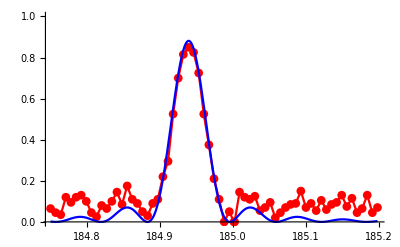

184.9393

2.06253

```mathematica
If[symbol,While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
RedY=DriveFrequencyFit[Join[{(Average[RedYFile,S1[]]ᵀ)[[1]]},{(0.9-(Average[RedYFile,S1[]]ᵀ)[[2]])}]ᵀ,True];(*red sideband y*)
Print[SetAccuracy[RedY,6]];
Print[Carr-RedY];
If[NumberQ@RedY,CtrlSignalValue[DDSBox@"Frequency (MHz)",RedY],Abort[]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"Gap"[0.5],"Raman4"[CarrPi],"Gap"[0.5],"Raman1"[RedXPi]}]]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,Pause[0.5];
RedXPiFile=ScanPar["Time",2+4(n+m)+3,{0.1,90,3}];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

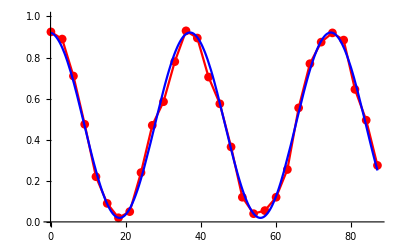

18.756

```mathematica
If[symbol,While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
RedXPi=RabiFrequencyFit[Average[RedXPiFile,S1[]],True];
Print[RedXPi];
If[NumberQ@RedXPi,CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"Zero"[1],"Raman4"[CarrPi],"Gap"[0.5],"Raman2"[RedYPi]}]]],Abort[]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,Pause[0.5];
RedYPiFile=ScanPar["Time",2+4(n+m)+3,{0.1,60,2}];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

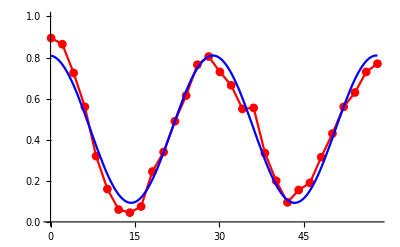

14.5327

```mathematica
If[symbol,While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
RedYPi=RabiFrequencyFit[Average[RedYPiFile,S1[]],True,20];
Print[RedYPi];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol&&(NumberQ@RedYPi),Print[η1=CarrPi/RedXPi];
Print[η2=CarrPi/RedYPi];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"Raman4"[RedXPi]}]];
CtrlSignalValue[DDSBox@"Channel",0];
CtrlSignalValue[DDSBox@"Profile",1];
CtrlSignalValue[DDSBox@"Amplitude",Raman2Amp];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]],Abort[]];
```

0.0809115

0.104425

```mathematica
If[symbol,Pause[0.5];
BlueXFile=ScanPar["AWG2",1,{189.3,189.6,0.006}];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

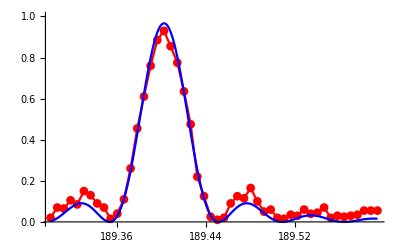

189.40209

2.40026

```mathematica
If[symbol,While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
BlueX=DriveFrequencyFit[Average[BlueXFile,S1[]],True];(*blue sideband x*)
Print[SetAccuracy[BlueX,6]];
Print[BlueX-Carr];
If[NumberQ@BlueX,CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"Gap"[0.5],"Raman4"[RedYPi]}]]],Abort[]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,Pause[0.5];
BlueYFile=ScanPar["AWG2",1,{188.9,189.25,0.007}];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

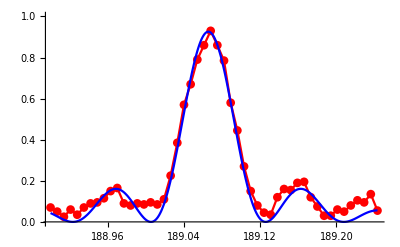

189.06555

2.06372

```mathematica
If[symbol,While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
BlueY=DriveFrequencyFit[Average[BlueYFile,S1[]],True];(*blue sideband x*)
Print[SetAccuracy[BlueY,6]];
Print[BlueY-Carr];
CtrlSignalValue[DDSBox@"Frequency (MHz)",BlueX];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,Pause[0.5];
BlueXPiFile=ScanPar["Time",2+4(n+m)+1,{0.1,100,2}];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

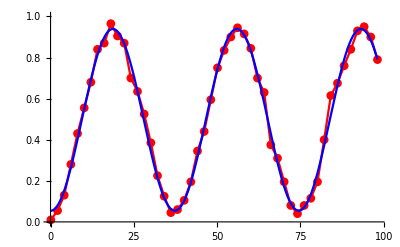

18.6044

0.808%

```mathematica
If[symbol,While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
BlueXPi=RabiFrequencyFit[Average[BlueXPiFile,S1[]],True,20];
Print[BlueXPi];
Print[NumberForm[Abs[BlueXPi-RedXPi]/RedXPi*100,3],"%"];SelectionMove[InputNotebook[],Next,Cell]];
```

```mathematica
SelectionMove[InputNotebook[],Previous,Cell,43];
```

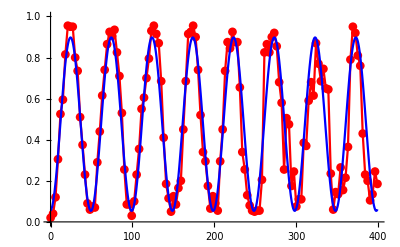

24.8818

```mathematica
BlueXPi=RabiFrequencyFit[Average["TimeScan-20201027163949",S1[]],True,25]
```

```mathematica
BlueXPi*11
```

268.881

π_b: 20.3046, Average phonon number: 0.0594688

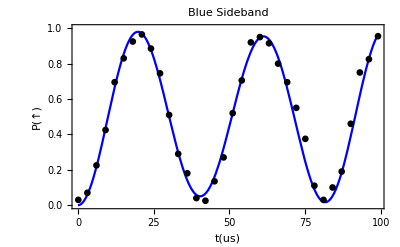

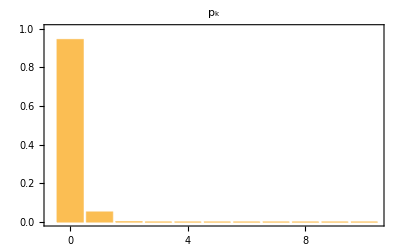

{0.0594688,20.3046}

```mathematica
ThermalStateFitBlue[Average[BlueXPiFile,S1[]],20,10]
```

```mathematica
BlueYPiFile=ScanPar["Time",3+4(n+m),{0.1,200,3}]
```

TimeScan-20191028142031

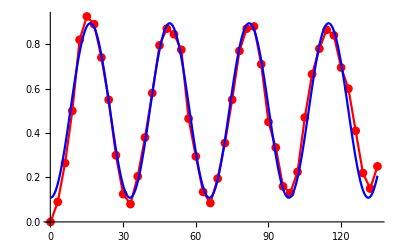

16.4017

```mathematica
BlueYPi=RabiFrequencyFit[Average[BlueYPiFile,S1[]],True]
```

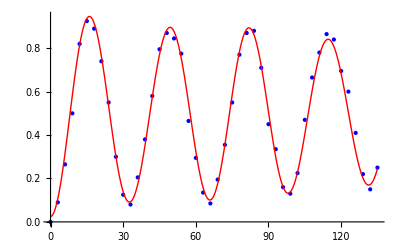

π-time: 16.403±0.05,   <n>: 0.04±0.049,   R^2: 0.995892

0.0447916

```mathematica
ThermalStateFit[Average[BlueYPiFile,S1[]],BlueYPi]
```

```mathematica
SequenceFile["Sequence/SBCooling.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"Raman2"[10]}]]
```

D:\Data\Sequence\SBCooling.seq

### After SBC

#### Raman Alignment optimization

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBCooling.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[51],"Zero"[1]}]]];
CtrlSignalValue[DDSBox@"Channel",0];
CtrlSignalValue[DDSBox@"Frequency (MHz)",RedX];
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Frequency (MHz)",RedY];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/test.csv",{{Carr,0.1,.6,0,0}}]];
```

```mathematica
ScanPar["AWG1",2,{0.1,30,.3}]
```

AWG1Scan-20191015142120

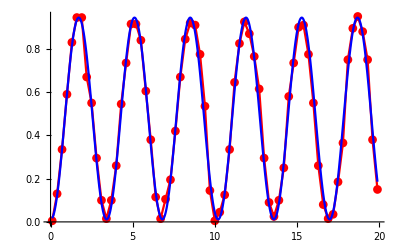

1.69683

```mathematica
RabiFrequencyFit[Average["AWG1Scan-20191015120201",S1[]],True,1.5]
```

#### Raman coherence measurement after SBC:

```mathematica
SequenceFile["Sequence/SBCooling.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"Raman3"[CarrPi/2],"Zero"[1],"Raman3"[CarrPi/2]}]];
CtrlSignalValue[DDSBox@"Channel",0];
CtrlSignalValue[DDSBox@"Frequency (MHz)",RedX];
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Frequency (MHz)",RedY];
CtrlSignalValue[sequencer@"Count or State",1];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",Carr];
CtrlSignalValue[sequencer@"Repeats",100];
```

```mathematica
ScanPar["Time",3+8n+1,{0.1,20000,200},True]
```

TimeScan-20210221164210

coherence time=47.5339ms

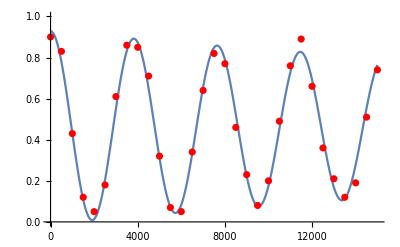

```mathematica
CoherenceTimeFit[Average["TimeScan-20200913144117",S1[]],5000]
```

#### Type 1 heating rate measurement:

```mathematica
delay=1;timevsnbar={};
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"Zero"[delay],"Raman3"[RedXPi]}]]];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",RedX];
```

```mathematica
reddata=SequencerScan["Time",3+8 n+1,0.1,100,5]
```

TimeScan-20190615150820

```mathematica
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",BlueX];
```

```mathematica
bluedata=SequencerScan["Time",3+8 n+1,0.1,100,5]
```

TimeScan-20190615150921

Average phonon number:0.82906

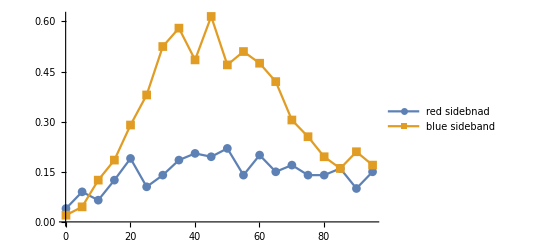

0.82906

```mathematica
nbar=PhononNumberFitByRBRatio[reddata,bluedata]
```

```mathematica
AppendTo[timevsnbar,{delay,nbar}];
delay=delay+2000;
```

HeatingRate=0.0949787/ms

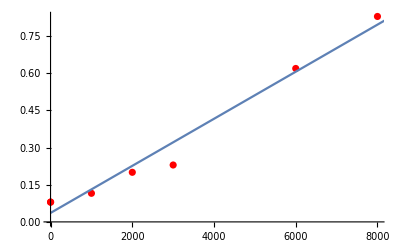

0.0949787

```mathematica
HeatingRateFit[timevsnbar]
```

#### Type 2 heating rate measurement(recommended):

```mathematica
delay=1000;timevsnbar={};repeats=1;CtrlSignalValue[sequencer@"Repeats",100];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",RedX];
DateString[]
```

2021-01-27 11:52:17

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"Zero"[delay],"Raman3"[RedXPi]}]]];
SelectionMove[EvaluationNotebook[],Next,Cell];FrontEndTokenExecute["Evaluate"];
```

```mathematica
If[symbol,AppendTo[timevsnbar,{delay,Table[redpeakfile=ScanPar["AOM",0,{184.45,184.7,0.006}];While[CtrlGetValue@sequencer@"Scan"];CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"Zero"[delay],"Raman3"[BlueXPi]}]]];bluepeakfile=ScanPar["AOM",0,{189.25,189.55,0.006}];While[CtrlGetValue@sequencer@"Scan"];ratio=PeakValueFit[Average[redpeakfile,S1[]]]/PeakValueFit[Average[bluepeakfile,S1[]]];ratio/(1-ratio),repeats]}];delay+=2000;If[delay≤11000,SelectionMove[EvaluationNotebook[],Previous,Cell,2];FrontEndTokenExecute["Evaluate"]]];
```

StandardDeviation::shlen: 参数 {0.0924104} 应该至少有两个元素.

StandardDeviation::shlen: 参数 {0.111301} 应该至少有两个元素.

StandardDeviation::shlen: 参数 {0.143663} 应该至少有两个元素.

General::stop: 在本次计算中，StandardDeviation::shlen 的进一步输出将被抑制.

HeatingRate=0.023726/ms

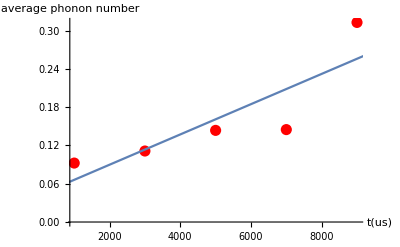

```mathematica
HeatingRateFit[timevsnbar[[1;;-2]]]
```

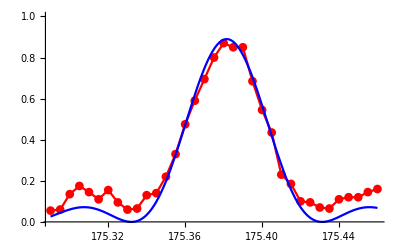

175.382

```mathematica
DriveFrequencyFit[Average["AOMScan-20191130201636",S1[]],True]
```

#### η fitting

```mathematica
sequenceTable={"Raman3"[RedXPi]};blueSidebandRabi={};end=90;step=3;
FockState=0;
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",BlueX];
```

```mathematica
If[symbol,CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,sequenceTable]]];
Pause[0.5];
blueSidebandFile=ScanPar["Time",3+8n+(Length@sequenceTable)-1,{0.1,end,step},True];
SelectionMove[EvaluationNotebook[],Next,Cell];
FrontEndTokenExecute["Evaluate"]];
```

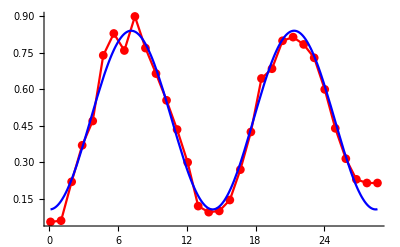

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,blueRabiPi=RabiFrequencyFit[Average[blueSidebandFile,S1[]],True];AppendTo[blueSidebandRabi,{FockState,1/(2blueRabiPi)}];
sequenceTable=Most[sequenceTable];
AppendTo[sequenceTable,"Raman3"[blueRabiPi]];
AppendTo[sequenceTable,"Pumping"[5]];
AppendTo[sequenceTable,"Raman3"[1]];
FockState+=1;
end=4*blueRabiPi;step=blueRabiPi/8;If[FockState≤10,SelectionMove[EvaluationNotebook[],Previous,Cell,3];
FrontEndTokenExecute["Evaluate"],SelectionMove[EvaluationNotebook[],Next,Cell];
FrontEndTokenExecute["Evaluate"]]];
```

0.0686272

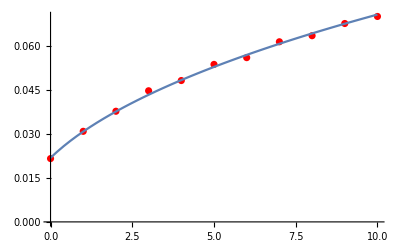

```mathematica
nlm=NonlinearModelFit[blueSidebandRabi,{E^(-η^2/2)η/Sqrt[x+1]LaguerreL[x,1,η^2]1/(2CarrPi)},{{η,0.07}},x];
η/.nlm["BestFitParameters"]
Show[ListPlot[blueSidebandRabi,PlotStyle->Red],Plot[nlm[x],{x,0,10}]]
```

#### AWG amplitude vs carrier Rabi rate

```mathematica
amplitude=0.1;CarrierRabi=0;DataForCarrRabi={};T=60;τ=1;i=1;
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[T+2]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/awg mplitude vs carrier Rabi calibrate.csv",{{Carr,CarrPi,amplitude,0,0}}]];
CtrlSignalValue[awg@"Row",0];
Pause[0.5];
If[amplitude≤1,filename=ScanPar["AWG1",2,{0.1,T,τ},True];SelectionMove[InputNotebook[],Next,Cell,1];
FrontEndExecute[FrontEndToken["Evaluate"]],Null];
```

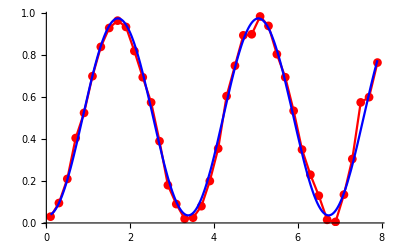

0.298395

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
CarrierRabi=1/(2RabiFrequencyFit[Average[filename,S1[]],True])
AppendTo[DataForCarrRabi,{amplitude,CarrierRabi}];
amplitude+=0.1;i+=1;
T-=(0.5*i^2+5);
τ-=.1;
If[T<0,T=8,Null];If[τ≤0.1,τ=0.2,Null];
SelectionMove[InputNotebook[],Previous,Cell,4];
FrontEndExecute[FrontEndToken["Evaluate"]];
```

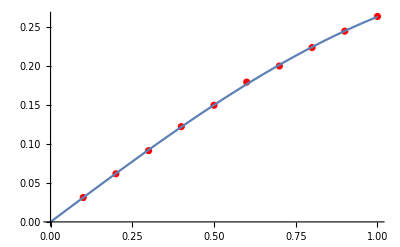

{0.312124,1.00103}

```mathematica
{a0,b0}=CalibrateForCarrierRabi[DataForCarrRabi]
```

### Motional coherence measurement

#### without separating qubit from motional coherence (recommended) :

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"Gap"[0.5],"Raman3"[BlueXPi/2],"Zero"[100],"Raman3"[BlueXPi/2]}]]];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",BlueX+0.002];
```

```mathematica
CtrlSignalValue[sequencer@"Trigger",False];
BlueXRamseyFile=ScanPar["Time",3+8n+1,{0.1,3200,40},True]
```

TimeScan-20210304114542

coherence time=0.843632ms

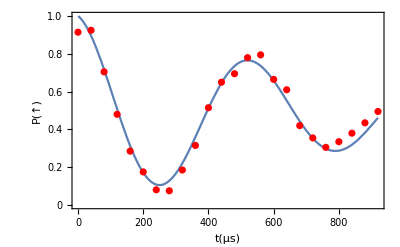

```mathematica
CoherenceTimeFit[Average[BlueXRamseyFile,S1[]],500](*After sbc BlueX without line-trigger*)
```

coherence time=0.651919ms

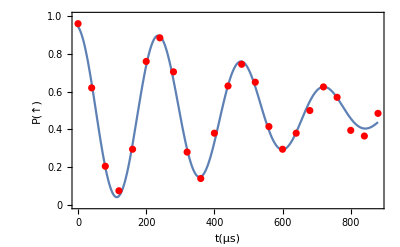

```mathematica
GaussianCoherenceFit[Average[BlueXRamseyFile,S1[]],500,100](*After sbc BlueX without line-trigger*)
```

Noise amplitude=0.407181kHz

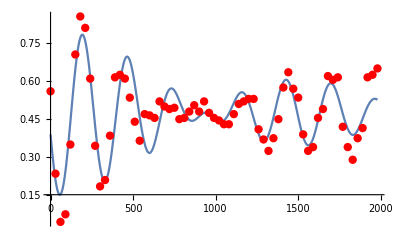

```mathematica
BesselCoherenceFit[Average[BlueXRamseyFile,S1[]],800]
```

```mathematica
totalDuration=Total@TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"Gap"[0.5],"Raman3"[BlueXPi/2],"Zero"[2000],"Raman3"[BlueXPi/2]}][[All,1]]
```

4040.8

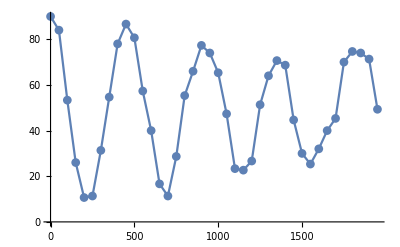

RamseyScanTime-20210302200700.mat

```mathematica
RamseyScanTime[BlueXPi,{.1,2000,50},"s",Ceiling@totalDuration,1,2,75,True]
```

coherence time=3.08206ms

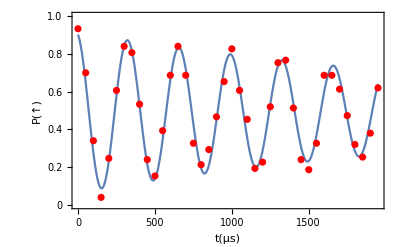

```mathematica
CoherenceTimeFit[Average["RamseyScanTime-20210301211649.mat",S1[1]],500]
```

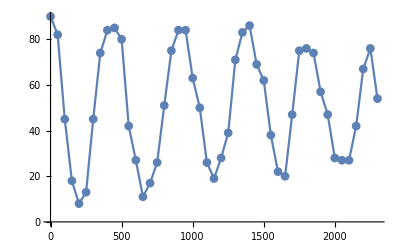

$Aborted

```mathematica
SequencerScanTime[TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"Gap"[0.5],"Raman3"[BlueXPi/2],"Zero"[100],"Raman3"[BlueXPi/2]}],2+8n+2,{.1,4000,50},"s",1,100,True]
```

```mathematica
BlueXRamseyFile="TimeScan-20201014160255";
```

coherence time=6.3165ms

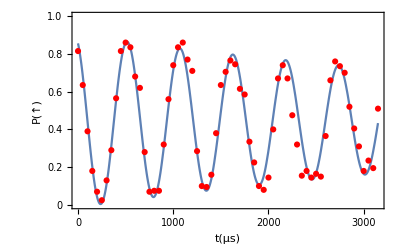

```mathematica
CoherenceTimeFit[Average[BlueXRamseyFile,S1[]],500,200]
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedYPi,η2,RedXPi,η1,{"Raman3"[BlueYPi/2],"Zero"[100],"Raman3"[BlueYPi/2]}]]];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",BlueY];
```

```mathematica
SequencerScan["Time",3+8n+1,0.1,1200,20]
```

$Aborted

coherence time=0.619691ms

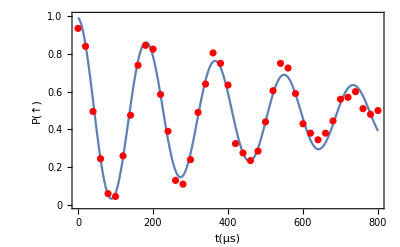

```mathematica
CoherenceTimeFit[Average["TimeScan-20190620203212",S1[]],500](*After sbc BlueY without line-trigger*)
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBCRaman.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"Raman3"[18]}]]];
CtrlSignalValue[sequencer@"Trigger",False];
CtrlSignalValue[sequencer@"Repeats",200];
```

```mathematica
BlueXFile=ScanPar["AOM",0,{BlueX-0.1,BlueX+0.1,0.005}]
```

AOMScan-20210130135124

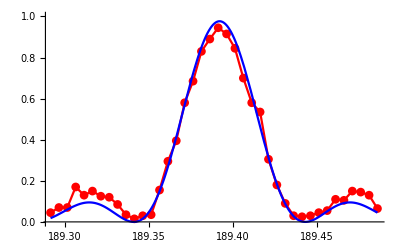

189.392

```mathematica
BlueX=DriveFrequencyFit[Average[BlueXFile,S1[]],True]
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/RamanCoherence.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"Raman3"[4.5],"Zero"[1],"Raman3"[4.5],"Detection"[300,1,1],"Zero"[1]}]];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",BlueX+0.012];
```

```mathematica
CtrlSignalValue[sequencer@"Trigger",False];
BlueXRamseyFile=ScanPar["Time",5,{.1,2000,40},True]
```

TimeScan-20200909213716

coherence time=0.619888ms

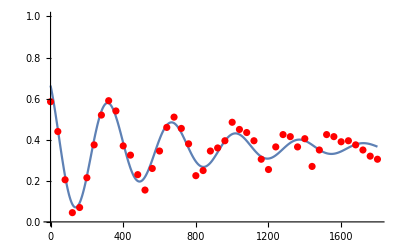

```mathematica
CoherenceTimeFit[Average[BlueXRamseyFile,S1[]],500,180](*After Doppler cooling,BlueX without line trigger*)
```

coherence time=5.71913ms

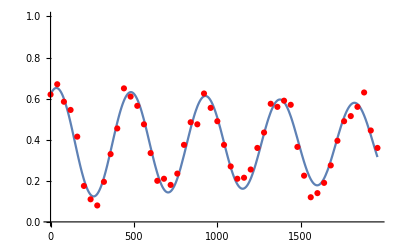

```mathematica
CoherenceTimeFit[Average[BlueXRamseyFile,S1[]],1000,200](*After Doppler cooling,BlueX with line trigger*)
```

coherence time=3.83278ms

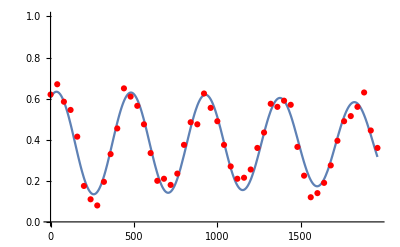

```mathematica
GaussianCoherenceFit[Average[BlueXRamseyFile,S1[]],2000,170](*After Doppler cooling,BlueX with line trigger*)
```

```mathematica
CtrlSignalValue[sequencer@"Trigger",False];
BlueXRamseyFile=ScanPar["Time",5,{.1,3000,20},True]
```

TimeScan-20200728120813

Noise amplitude=0.261978kHz

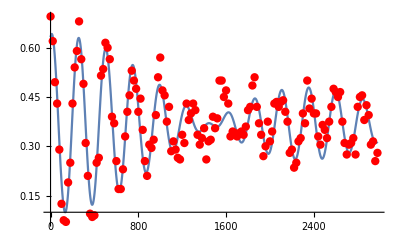

```mathematica
BesselCoherenceFit[Average[BlueXRamseyFile,S1[]],500]
```

Noise amplitude=0.33197kHz

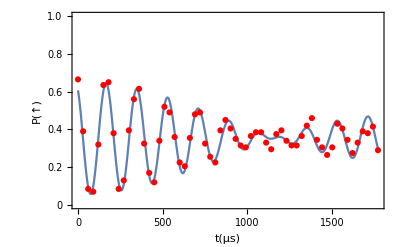

```mathematica
fig=BesselCoherenceFit[Average["TimeScan-20190710162207",S1[]],1000,50*^-6]
```

```mathematica
Export["E:\\member\\cml_maverick\\lab figure\\BesselCoherenceFit.png",fig,ImageResolution->400]
```

E:\member\cml_maverick\lab figure\BesselCoherenceFit.png

#### separating qubit from motional coherence:

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SDF.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"AWG"[1],"Raman"[1000],"Detection"[400,1,1],"Zero"[1]}]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Ramsey.csv",{{Carr,1.9,1,0,0},{BlueX,6.5,1,0,0},{BlueX,6.5,1,0,0},{Carr,1.9,1,0,0}}]];
CtrlSignalValue[awg@"Row",1];
```

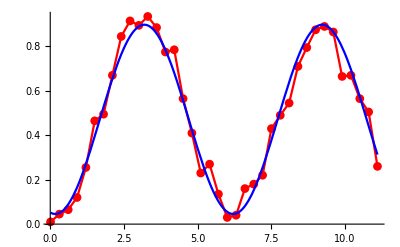

3.02006

```mathematica
CarrPi=RabiFrequencyFit[Average["TimeScan-20190525161530",S1[]],True]
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"Gap"[10],"Raman4"[CarrPi/2],"Raman3"[BlueXPi],"Gap"[100],"Raman3"[BlueXPi],"Raman4"[CarrPi/2]}]]];(*notice to open the profile1 of dds1 in chapter Raman3*)
```

```mathematica
ScanPar["Time",3+8n+3,{0.1,1000,20},True]
```

TimeScan-20190622211531

coherence time=0.703591ms

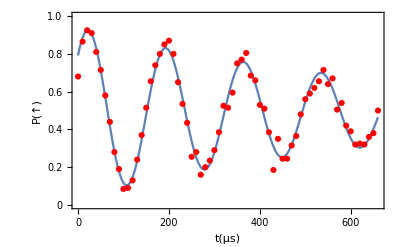

```mathematica
CoherenceTimeFit[Average["TimeScan-20190527225042",S1[]],500]
```

```mathematica
(*microwave as Pi/2 pulse driver*)
```

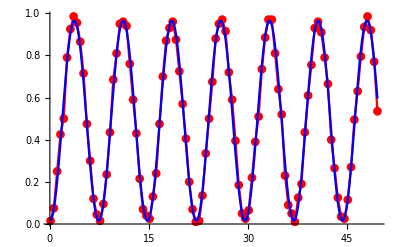

3.69193

```mathematica
MWCarrPi=RabiFrequencyFit[Average["TimeScan-20190719195817",S1[]],True,4]
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"Horn"[MWCarrPi/2],"Raman3"[BlueXPi],"Zero"[100],"Raman3"[BlueXPi],"Horn"[MWCarrPi/2]}]]];
```

```mathematica
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",BlueX];
```

```mathematica
ScanPar["Time",3+8n+2,{0.1,2000,20},True]
```

TimeScan-20190719201758

coherence time=0.488817ms

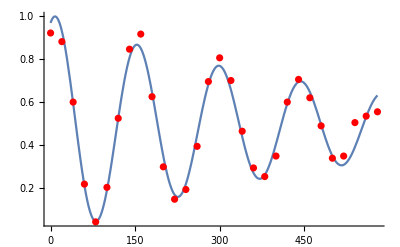

```mathematica
CoherenceTimeFit[Average["TimeScan-20190719201648",S1[]],500](*Without line trigger*)
```

coherence time=7.05312ms

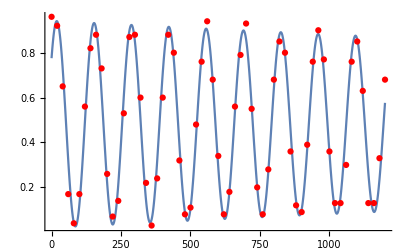

```mathematica
CoherenceTimeFit[Average["TimeScan-20190719201758",S1[]],1000](*With line trigger*)
```

#### T2Echo:

```mathematica
ClearAll[T2Echo];
T2Echo[range_List,Pitime_]:=Module[{file=NewData["T2Echo"<>"-"],data={},plot={},counts},SequencerAxis@@range;CtrlSignalValue[sequencer@"Repeats",100];CtrlSignalValue[sequencer@"Count or State",1];Table[CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/T2Echo.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"Raman3"[Pitime/2],"Zero"[t/2],"Raman3"[Pitime],"Zero"[t/2],"Raman3"[Pitime/2],"Detection"[400,1,1],"Zero"[1]}]];Pause[1];counts=SequencerCounts[];AppendTo[data,{t,counts}];
AppendTo[plot,{t,Mean@ToState@counts}],{t,range[[1]],range[[2]],range[[3]]}];{Each[plot,{#1,#2}&],ExportData[file,{"C"-><|"Channel"->{1}|>,"X"->List/@data⟦All,1⟧,"Y_Count"->data⟦All,2⟧}]}];
```

```mathematica
datafile=T2Echo[{0.1,1400,30},9][[2]];
```

coherence time=2.29339ms

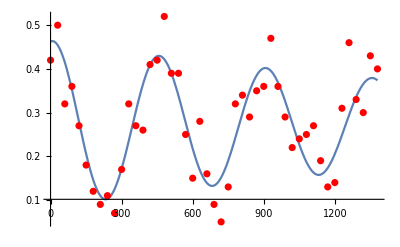

```mathematica
CoherenceTimeFit[Average[datafile,S1[1]],1000]
```

coherence time=1.69268ms

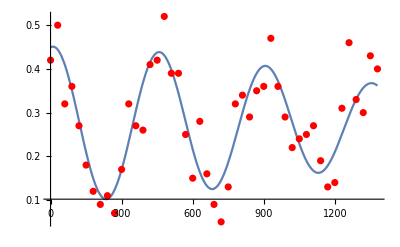

```mathematica
GaussianCoherenceFit[Average[datafile,S1[1]],1000,250]
```

### Trap frequency measurement

#### precision measurement of trap freq:

```mathematica
If[symbol,CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBCRaman.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"Raman3"[18]}]]];
CtrlSignalValue[sequencer@"Trigger",False];
CtrlSignalValue[sequencer@"Repeats",200];
Pause[0.1];
BlueXFile=ScanPar["AOM",0,{BlueX-0.1,BlueX+0.1,0.005}];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
BlueX=DriveFrequencyFit[Average[BlueXFile,S1[]],True];
Print@BlueX;
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

Transpose::nmtx: {Missing[KeyAbsent,X],Missing[KeyAbsent,Y]} 的前两层无法转置.

DriveFrequencyFit[Average[Transpose[Missing[KeyAbsent,X,ToState[Missing[]]]],Mean],True]

```mathematica
If[symbol,CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBCRamanCoherence.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"Gap"[0.5],"Raman3"[BlueXPi/2],"Zero"[1],"Raman3"[BlueXPi/2]}]]];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",BlueX];
CtrlSignalValue[sequencer@"Trigger",False];
Pause[0.1];
BlueXRamseyFile=ScanPar["Time",3+4(n+m)+1,{.1,200,3},True];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

MakeNETObject::arg: MakeNETObject cannot convert DriveFrequencyFit[Average[Transpose[Missing[KeyAbsent,X,ToState[Missing[]]]],Mean],True] to a .NET object. It does not operate on arguments of that type.

NET::netexcptn: A .NET exception occurred: System.ArgumentException: Expression cannot be read as the requested type.
   at Wolfram.NETLink.Internal.CallPacketHandler.makeObject(KernelLinkImpl ml).

NET::methodargs: Improper arguments supplied for method named Call.

```mathematica
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
Bluedetuning=1/(2RabiFrequencyFit[Average[BlueXRamseyFile,S1[]],True,20])
```

Transpose::nmtx: {Missing[KeyAbsent,X],Missing[KeyAbsent,Y]} 的前两层无法转置.

1/(2 RabiFrequencyFit[Average[Transpose[Missing[KeyAbsent,X,ToState[Missing[]]]],Mean],True,20])

```mathematica
gap=100;spanleft=0.006;spanright=0.006;step=0.0006;Ramseyblue=BlueX+Bluedetuning;
CtrlSignalValue[sequencer@"Repeats",100];
CtrlSignalValue[sequencer@"Trigger",False];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",BlueX];
DateString[]
SelectionMove[EvaluationNotebook[],Next,Cell];
FrontEndTokenExecute["Evaluate"];
```

2021-03-06 22:03:47

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBCRamanCoherence.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"Raman3"[BlueXPi/2],"Zero"[gap],"Raman3"[BlueXPi/2]}]]];
SelectionMove[EvaluationNotebook[],Next,Cell];
FrontEndTokenExecute["Evaluate"];
```

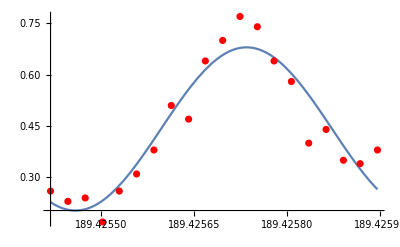

189.425735

```mathematica
If[gap≤600,CtrlSignalValue[sequencer@"Trigger",False],CtrlSignalValue[sequencer@"Trigger",True]];
Ramseybluefile=ScanPar["AOM",0,{Ramseyblue-spanleft,Ramseyblue+spanright,step}];
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,Ramseyblue=RamseyFrequencyFit[Average[Ramseybluefile,S1[]],gap+BlueXPi/2][[3]];
Print@NumberForm[Ramseyblue,9];
Which[gap≤300,gap+=100,gap≤1000,gap+=200,gap≤2000,gap+=300,gap>2000,gap+=300];spanleft=1./gap/2;spanright=1./gap/2;step=(spanright+spanleft)/20.;
If[gap≤2000,SelectionMove[EvaluationNotebook[],Previous,Cell,4];
FrontEndTokenExecute["Evaluate"],SelectionMove[EvaluationNotebook[],Next,Cell];
FrontEndTokenExecute["Evaluate"]]];
```

```mathematica
trapfreq=Ramseyblue-MWCarr
DateString[]
(*If[StringQ@CalibrateTag,SelectionMove[Cells[CellTags->CalibrateTag][[1]],All,Cell];FrontEndTokenExecute["Evaluate"]];*)
```

2.42501

2021-03-06 22:08:39

#### trap freq measurement by weak laser pulse:

```mathematica
trapfreqTable={};
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBCRaman.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"Raman3"[400]}]]];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",1];
```

```mathematica
Do[BlueXFile=ScanPar["AOM",0,{BlueX,BlueX+0.012,0.0004}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
TrueBlueX=DriveFrequencyFit[Average[BlueXFile,S1[]]];AppendTo[trapfreqTable,TrueBlueX],100]
```

$Aborted

```mathematica
trapfreqTable
```

{175.532,175.532,175.532}

#### longterm variation of trap freq:

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBCRamanCoherence.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"Raman3"[BlueXPi/2],"Zero"[100],"Raman3"[BlueXPi/2]}]]];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",1];
```

```mathematica
Ramseybluefile=ScanPar["AOM",0,{TrueBlueX-0.006,TrueBlueX+0.006,0.0005}];
```

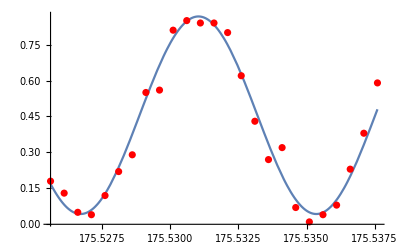

{0.412161,0.455121,175.531}

```mathematica
result=RamseyFrequencyFit[Average[Ramseybluefile,S1[]],100+BlueXPi/2]
```

```mathematica
FreqSet=175.530;
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",FreqSet];
```

```mathematica
ClearAll[RawDataTable,T2];T2=1000;RawDataTable={};
```

```mathematica
Dynamic@ListPlot[RawDataTable,PlotStyle->PointSize[Medium]]
totaltime2=AbsoluteTiming[Table[CtrlSignalValue[sequencer@"Data",True];
While[CtrlGetValue@sequencer@"Data"===True,Pause[0.1]];AppendTo[RawDataTable,{i,FreqSet-Abs[ArcCos[(CtrlGetValue[sequencer@"Average Plot"][[1]]/100-result[[2]])/result[[1]]]]/(2Pi (200+4))}],{i,T2}]][[1]];
```

UpSet::write: NETObjectQ[«NETObject[System.UInt32]»] 中的标签 «NETObject[System.UInt32]» 被保护.

SetDelayed::write: («NETObject[System.UInt32]»)[(NETLink`CallNET`Private`meth$:_[___])[NETLink`CallNET`Private`args$___]] 中的标签 «NETObject[System.UInt32]» 被保护.

SetDelayed::write: («NETObject[System.UInt32]»)[NETLink`CallNET`Private`fieldOrProp$_Symbol[NETLink`CallNET`Private`arg$__]] 中的标签 «NETObject[System.UInt32]» 被保护.

SetDelayed::write: («NETObject[System.UInt32]»)[NETLink`CallNET`Private`meth$_[NETLink`CallNET`Private`args$___]] 中的标签 «NETObject[System.UInt32]» 被保护.

General::stop: 在本次计算中，SetDelayed::write 的进一步输出将被抑制.

UpSet::write: NETLink`CallNET`Private`aqTypeNameFromInstance[«NETObject[System.UInt32]»] 中的标签 «NETObject[System.UInt32]» 被保护.

UpSet::write: NETLink`CallNET`Private`isCOMObject[«NETObject[System.UInt32]»] 中的标签 «NETObject[System.UInt32]» 被保护.

General::stop: 在本次计算中，UpSet::write 的进一步输出将被抑制.

Set::write: «NETObject[System.UInt32]» 中的标签 «NETObject[System.UInt32]» 被保护.

Set::write: MakeBoxes[«NETObject[System.UInt32]»,NETLink`CallNET`Private`fmt$_] 中的标签 «NETObject[System.UInt32]» 被保护.

General::stop: 在本次计算中，Set::write 的进一步输出将被抑制.

$Aborted

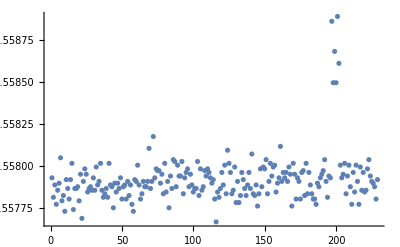

```mathematica
ListPlot[RawDataTable,PlotRange->All]
```

```mathematica
totaltime2/60
```

16.9661

```mathematica
trapfreqM=SetAccuracy[Mean@(RawDataTableᵀ[[2]]),7]
trapfreqSD=SetAccuracy[StandardDeviation@(RawDataTableᵀ[[2]]),7]
```

175.560871

0.000135

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>ToString[totaltime2/60]<>" min variation of trap freq raw data"<>DateString[{"Hour","Minute","Second"}]<>".csv",Prepend[RawDataTable,{"mean="<>ToString@trapfreqM,"standard deviation="<>ToString@trapfreqSD}]];
```

### Spin dependent force

#### Rough calibrate

```mathematica
δ=0.015;
amplitude=0.2;
SDFRed=freqr[amplitude];
SDFBlue=freqb[amplitude];
SDFRedPi=1/(2 A[amplitude]);
SDFBluePi=1/(2 A[amplitude]);
```

```mathematica
If[symbol,CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[SDFBluePi+2]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{SDFRed-δ,0,amplitude,0,0},{SDFBlue,0,amplitude,0,0},{0,SDFBluePi,0,0,0,"[0 1]"}}]];
CtrlSignalValue[awg@"Row",1];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,Pause[0.5];
SDFBlueFile=ScanPar["AWG1",1,{189.35,189.55,0.002},True];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

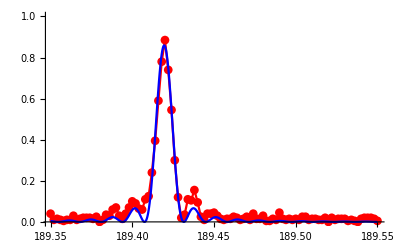

189.42

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,SDFBlue=DriveFrequencyFit[Average[SDFBlueFile,S1[]],True];(*blue sideband x for SDF*)
Print[SDFBlue];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[SDFRedPi+4]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{Carr,CarrPi,1,0,0},{SDFRed,0,amplitude,0,0},{SDFBlue+δ,0,amplitude,0,0},{0,SDFRedPi,0,0,0,"[1 2]"}}]];
CtrlSignalValue[awg@"Row",1];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,Pause[0.5];
SDFRedFile=ScanPar["AWG1",1,{184.45,184.65,0.002},True];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

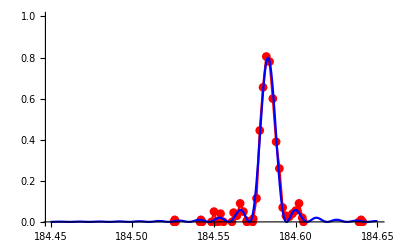

184.583

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,SDFRed=DriveFrequencyFit[Join[{(Average[SDFRedFile,S1[]]ᵀ)[[1]]},{(0.9-(Average[SDFRedFile,S1[]]ᵀ)[[2]])}]ᵀ,True];(*Red sideband x for SDF*)
Print[SDFRed];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[252]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{Carr,CarrPi,1,0,0},{SDFRed,0,amplitude,0,0},{SDFBlue+δ,0,amplitude,0,0},{0,RedXPi,0,0,0,"[1 2]"}}]];
CtrlSignalValue[awg@"Row",3];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,Pause[0.5];
SDFRedPiFile=ScanPar["AWG1",2,{0.1,250,8},True];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

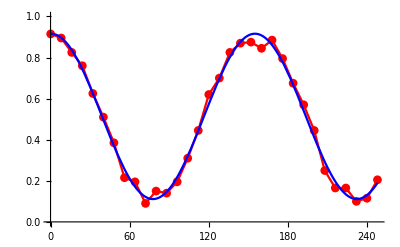

77.3534

0.00646384

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,SDFRedPi=RabiFrequencyFit[Average[SDFRedPiFile,S1[]],True];(*Red Pi time*)
Print[SDFRedPi];
Print[1/(2SDFRedPi)];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[252]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{SDFRed-δ,0,amplitude,0,0},{SDFBlue,0,amplitude,0,0},{0,BlueXPi,0,0,0,"[0 1]"}}]];
CtrlSignalValue[awg@"Row",2];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,Pause[0.5];
SDFBluePiFile=ScanPar["AWG1",2,{0.1,250,8},True];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

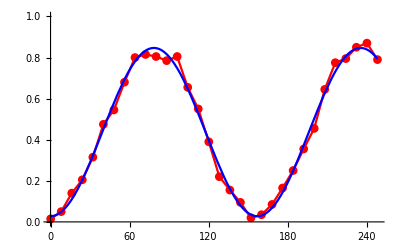

78.4164

0.00637622

1.37417

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,SDFBluePi=RabiFrequencyFit[Average[SDFBluePiFile,S1[]],True,60];(*Blue Pi time*)
Print[SDFBluePi];
Print[1/(2SDFBluePi)];
Print[100Abs[SDFBluePi-SDFRedPi]/SDFRedPi];
SelectionMove[InputNotebook[],Next,Cell]];
```

```mathematica
SelectionMove[InputNotebook[],Previous,Cell,21];
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[5]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{187,6,amplitude,0,0}}]];
```

```mathematica
CarrFreqFile=ScanPar["AWG1",1,{186.6,187.4,0.01},True]
```

AWG1Scan-20210127112051

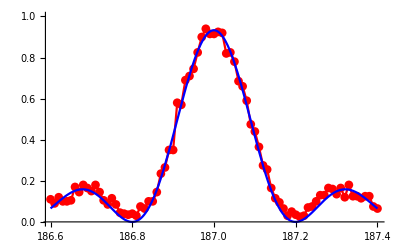

187.

```mathematica
Carrfreq=DriveFrequencyFit[Average[CarrFreqFile,S1[]],True]
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[12]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{Carrfreq,0.1,1,0,0}}]];
```

```mathematica
CarrFile=ScanPar["AWG1",2,{0.1,10,.2},True]
```

AWG1Scan-20210127112203

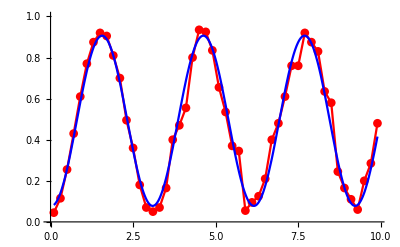

0.326215

```mathematica
1/(2RabiFrequencyFit[Average[CarrFile,S1[]],True])
```

```mathematica
PulseInducedCarrShift[{0.1,5000,100},187,CarrPi,amplitude,SDFRed-δ,SDFBlue+δ]
```

Pulse induced carrier shift-20210127161104.mat

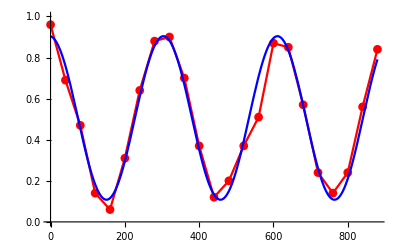

```mathematica
CarrierShift=1/(2RabiFrequencyFit[Average["Pulse induced carrier shift-20210118173842.mat",S1[]],True])
```

```mathematica
(SDFRed+SDFBlue)/2-173.0408
```

0.00170811

```mathematica
WaveFile["Wave/SDFCal.csv",{{SDFRed-2δ,0,0.5,0,0},{SDFBlue+2δ,0,0.5,0,0},{0,3200,0,0,0,"[0 1]"}}];
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/HornRamsey.seq",{"Cooling"[3000],"Zero"[1],"Pumping"[10],"Zero"[1],"Horn"[MWCarrPi/2],"AWG"[1],"Gap"[1000],"Horn"[MWCarrPi/2],"Detection"[300,1,1],"Zero"[1]}]];
```

```mathematica
ScanPar["Time",6,{0.1,3000,100}]
```

TimeScan-20210118213827

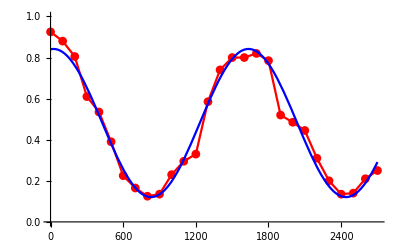

0.000621181

```mathematica
1/(2RabiFrequencyFit[Average["TimeScan-20210118213827",S1[]],True])
```

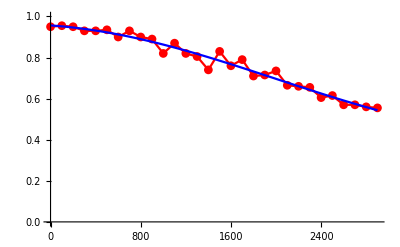

0.000107146

```mathematica
(*pll一侧单路Raman光引起的fourth order Stark shift*)
1/(2RabiFrequencyFit[Average["TimeScan-20210118213550",S1[]],True])
```

#### Fine calibrate(Refer to the thesis of P. J. Lee):

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[SDFBluePi+5]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{SDFRed-0.02,0,amplitude,0,0},{SDFBlue+0.02,0,amplitude,0,0},{0,SDFBluePi,0,0,0,"[0 1]"}}]];
CtrlSignalValue[sequencer@"Item","RF"];
CtrlSignalValue[sequencer@"Parameter",0];
RF=CtrlGetValue@sequencer@"Value";
```

```mathematica
Do[CtrlSignalValue[sequencer@"Start",RF-0.005 i];Pause[0.5],{i,10}];
```

```mathematica
CurrentRF=CtrlGetValue[sequencer@"Value"];Pause[0.1];
RFScanForBlue=ScanPar["RF",0,{CurrentRF,RF+0.001,0.001},True]
```

RFScan-20190818203559

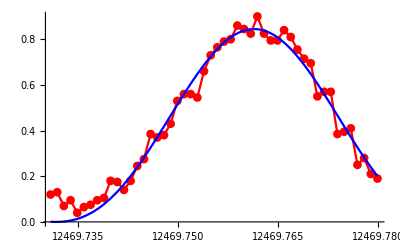

```mathematica
BlueRF=DriveFrequencyFit[Average[RFScanForBlue,S1[]],True]
```

```mathematica
12469.76135601497
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[SDFRedPi+5]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{Carr,CarrPi,1,0,0},{SDFRed-0.02,0,amplitude,0,0},{SDFBlue+0.02,0,amplitude,0,0},{0,SDFRedPi,0,0,0,"[1 2]"}}]];
CtrlSignalValue[sequencer@"Item","RF"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",RF];
```

```mathematica
RFScanForRed=ScanPar["RF",0,{RF,RF+0.05,0.001},True]
```

RFScan-20190818164046

```mathematica
RedRF=DriveFrequencyFit[Average[RFScanForRed,S1[]],True]
```

```mathematica
(*CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[SDFRedPi+5]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{Carr,CarrPi/2,1,0,0},{SDFRed-0.02,0,1,0,0},{SDFBlue+0.02,0,1,0,0},{0,SDFRedPi,0,0,0,"[0 1]"}}]];
CtrlSignalValue[sequencer@"Item","RF"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",RF];*)
```

#### Coherent state generation:

```mathematica
δ=0.003;
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[1/(2δ)+2],"Pumping"[3],"Raman3"[1]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{SDFRed-δ,0,amplitude,0,0},{SDFBlue+δ,0,amplitude,0,0},{0,1/(2δ),0,0,0,"[0 1]"}}]];
```

```mathematica
CtrlSignalValue[sequencer@"Trigger",True];
ScanPar["Time",8*n+6,{0.1,140,2}]
```

TimeScan-20200102121635

```mathematica
theodata=Table[{i,PDF[PoissonDistribution[3.15],i]},{i,0,12}];
```

π_b: 19.8884, Average phonon number: 3.14629±1.22369, Occupation: 0.92742, R^2: 0.996068

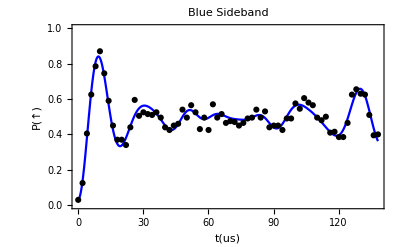

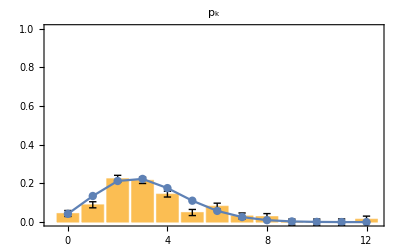

{{{0.044626,0.0154301},{0.0895882,0.0156448},{0.224293,0.0174922},{0.215976,0.0162629},{0.144709,0.0149187},{0.0496986,0.0157483},{0.0824098,0.0154996},{0.031969,0.0152566},{0.028772,0.0152849},{5.04725×10^-7,0.015588},{0.0000479528,0.015678},{1.94684×10^-6,0.0162334},{0.0153276,0.015679}},3.14629,1.22369,19.8884,{0.311571,0.311571}}

```mathematica
PhononBSBFit[Average["TimeScan-20200102121635",S1[]],theodata,BlueXPi,12]
```

πb_(0, 1) = 19.9866

α = 1.14166 ± 0.0322505

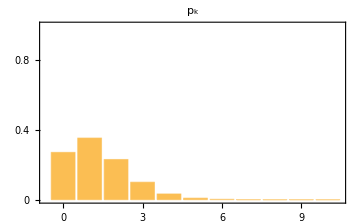

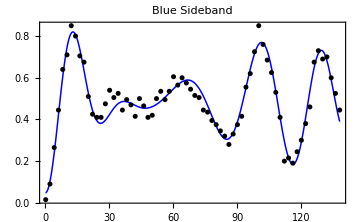

{1.14166,0.0322505}

```mathematica
CoherentStateFittingBlue[Average["TimeScan-20200102120717",S1[]],BlueXPi,Sqrt[1.3],10]
```

#### Scan time with fixed detuning:

```mathematica
δ=0.01;
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[302]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{SDFRed-δ,0,amplitude,0,0},{SDFBlue+δ,0,amplitude,0,0},{0,10,0,0,0,"[0 1]"}}]];
CtrlSignalValue[awg@"Row",2];
```

```mathematica
CtrlSignalValue[sequencer@"Trigger",False];
ScanPar["AWG1",2,{0.1,300,5},True]
```

AWG1Scan-20210127114258

period=90.9092us

initial phonon number=0.0806212

heating rate=0.696378/ms

sideband Rabi rate=6.28046kHz

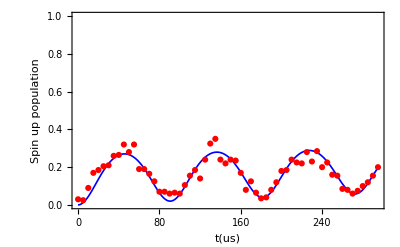

0.011

```mathematica
SDFScanTimeFit[Average["AWG1Scan-20210127114258",S1[]],1/(2SDFBluePi),0.01,0.01](*abnormal heating rate may indicate there are other dephasing factors*)
```

```mathematica
amplitude=0.5;CarrierShift=0.0002;
```

```mathematica
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{(*SDFRed-δ*)MWCarr+CarrierShift-trapfreq-δ,0,amplitude,0,0},{(*SDFBlue+δ*)MWCarr+CarrierShift+trapfreq+δ,0,amplitude,0,0},{0,320,0,0,0,"[0 1]"}}]];
```

```mathematica
Total[{"Cooling"[1000],"Zero"[1],"Pumping"[5],"Zero"[1],"AWG"[1],"Raman"[350],"Detection"[300,1,1],"Zero"[1]}[[All,1]]]
```

1659

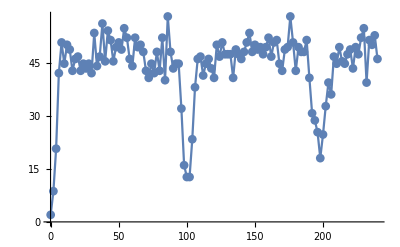

Time-20210130201813.mat

```mathematica
SequencerScanTime[{"Cooling"[1000],"Zero"[1],"Pumping"[5],"Zero"[1],"AWG"[1],"Raman"[250],"Detection"[300,1,1],"Zero"[1]},5,{.1,250,2},"s",3,50,True]
```

period=99.4316us

initial phonon number=19.9943

heating rate=0.999805/ms

sideband Rabi rate=6.69465kHz

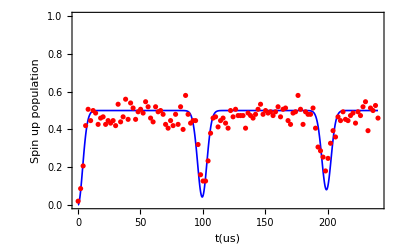

0.0100572

```mathematica
SDFScanTimeFit[Average["Time-20210130201813.mat",S1[1]],1/(2SDFBluePi),0.011](*0.01*)
```

```mathematica
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{173.0408+CarrierShift-trapfreq-δ,0,amplitude,0,0},{173.0408+CarrierShift+trapfreq+δ,0,amplitude,0,0},{0,10,0,0,0,"[0 1]"}}]];
CtrlSignalValue[awg@"Row",2];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SDF.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"AWG"[1],"Raman"[250],"Detection"[400,1,1],"Zero"[1]}]];
```

```mathematica
ScanPar["AWG1",2,{0.1,250,3}]
```

AWG1Scan-20191017222145

period=87.2727us

initial phonon number=19.9992

heating rate=0.999855/ms

sideband Rabi rate=5.24993kHz

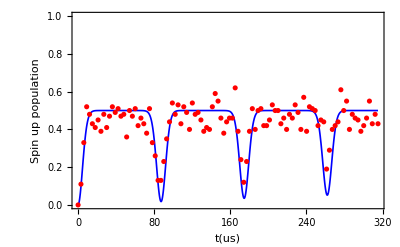

0.0114583

```mathematica
SDFScanTimeFit[Average["AWG1Scan-20190715214531",S1[]],0.005,0.0115](*0.011*)
```

#### Scan detuning with fixed time:

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[202]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFScan.csv",{{0.,1/δ,0,0,0,ToFormulaString[amplitude(Cos[2Pi(SDFRed-(f-4*δ))t]+Cos[2Pi(SDFBlue+(f-4*δ))t])]}}]];
```

```mathematica
CtrlSignalValue[sequencer@"Trigger",True];
ScanPar["AWG1",1,{0.,8*δ,0.001},True]
```

AWG1Scan-20191130165231

period=99.2837us

initial phonon number=1.01442×10^-6

heating rate=8.17769×10^-6/ms

sideband Rabi rate=4.75kHz

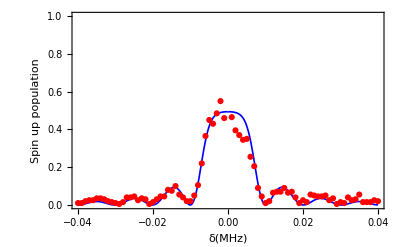

0.0100721

```mathematica
SDFScanDetuningFit[DeleteCases[{Average["AWG1Scan-20191130165231",S1[]][[All,1]]-4δ,Average["AWG1Scan-20191130165231",S1[]][[All,2]]}ᵀ,{0.,_}],1/(2*100),100]
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SDF.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"AWG"[1],"Raman"[102],"Detection"[300,1,1],"Zero"[1]}]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFScan.csv",{{0.,1/δ,0,0,0,ToFormulaString[amplitude(Cos[2Pi(SDFRed-(f-4*δ))t]+Cos[2Pi(SDFBlue+(f-4*δ))t])]}}]];
```

```mathematica
CtrlSignalValue[sequencer@"Trigger",True];
ScanPar["AWG1",1,{0.,8*δ,0.0008},True]
```

AWG1Scan-20191130211854

period=99.5061us

initial phonon number=2.59205

heating rate=0.999974/ms

sideband Rabi rate=5.24992kHz

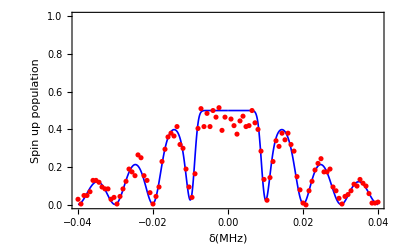

0.0100496

```mathematica
SDFScanDetuningFit[DeleteCases[{Average["AWG1Scan-20191130211854",S1[]][[All,1]]-4δ,Average["AWG1Scan-20191130211854",S1[]][[All,2]]-0.015}ᵀ,{0.,_}],1/(2*100),100]
```

```mathematica
Plot[1/2(1-E^(-2 (Ωsb/δ)^2 hr τ-(2n0+1)(Ωsb/δ)^2(1-Cos[2Pi δ τ])))/.{Ωsb->0.004,hr->5*10^-3,τ->100,n0->6},{δ,-0.04,0.04},PlotRange->All]
```

-Graphics-

### Two ions monitor

```mathematica
SequenceFile@DataPath@"Sequence\\Cooling.seq";
CtrlSignalValue[sequencer@"Repeats",200];
CtrlSignalValue[sequencer@"Count or State",0];
```

```mathematica
ClearAll[T1,CountsData,counts];CountsData={};T1=4000;
```

```mathematica
Dynamic[ListPlot[CountsData,PlotStyle->PointSize[Medium]]]
totaltime1=AbsoluteTiming[Table[CtrlSignalValue[sequencer@"Data",True];
While[CtrlGetValue@sequencer@"Data"===True,Pause[0.1]];
counts=CtrlGetValue[sequencer@"Average Plot"][[1]];AppendTo[CountsData,{i,If[counts≤1,CtrlSignalValue[DCV@"switch",5];Pause[2];CtrlSignalValue[DCV@"switch",0];counts,counts]}],{i,T1}]][[1]];
```

```mathematica
totaltime1/60
Cases[CountsData,_?(#[[2]]≤1&)]
```

57.3627

{{279,0.84},{515,0.72},{829,0.705},{1067,0.6},{1127,0.635},{1170,0.495},{1174,0.83},{1193,0.945},{1240,0.82},{1556,0.92},{1600,0.435},{1685,0.885},{2103,0.72},{2506,0.785},{2893,0.675},{2995,0.42},{3264,0.665},{3808,0.875},{3912,0.67},{3936,0.73}}

```mathematica
ListPlot[CountsData,PlotRange->All]
```

-Graphics-

### MS gate

```mathematica
amplitude=0.2;
MSRed1=MSRed2=freqr[amplitude] ;
MSBlue1=MSBlue2=freqb[amplitude];
MSRedPi1=MSRedPi2=1/(2 a0 Sin[b0 amplitude]);
MSBluePi1=MSBluePi2=1/(2 a0 Sin[b0 amplitude]);
```

```mathematica
If[symbol,CtrlSignalValue[sequencer@"Sequence File",If[NumberQ@RedXPi,ExportSequenceFile["Sequence/SBCooling.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[15],"Zero"[1]}]],Abort[]]];
CtrlSignalValue[DDSBox@"Channel",0];
If[NumberQ@RedX,CtrlSignalValue[DDSBox@"Frequency (MHz)",RedX],Abort[]];
CtrlSignalValue[DDSBox@"Channel",1];
If[NumberQ@RedY,CtrlSignalValue[DDSBox@"Frequency (MHz)",RedY],Abort[]];
If[NumberQ@Carr,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/test.csv",{{Carr,.1,1,0,0}}]],Abort[]];
SelectionMove[InputNotebook[],Next,Cell](*;
FrontEndExecute[FrontEndToken["Evaluate"]]*)];
```

```mathematica
CarrFile=ScanPar["AWG1",2,{0.1,14,0.2},True]
```

AWG1Scan-20191212214408

```mathematica
CarrfreqPi=RabiFrequencyFit[Average[CarrFile,C1[]],True,1.5,PlotRange->All]
```

-Graphics-

1.53929

```mathematica
CtrlSignalValue[sequencer@"Start",4CarrfreqPi]
```

6.00044

```mathematica
If[symbol,CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[MSBluePi1+2]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{MSRed1-0.02,0,amplitude,0,0},{MSBlue1,0,amplitude,0,0},{0,MSBluePi1,0,0,0,"[0 1]"}}]];
CtrlSignalValue[awg@"Row",1];
SelectionMove[InputNotebook[],Next,Cell](*;
FrontEndExecute[FrontEndToken["Evaluate"]]*)];
```

```mathematica
MSBlueFile1=ScanPar["AWG1",1,{175.37,175.42,0.001},True]
```

AWG1Scan-20191212214454

```mathematica
MSBlue1=DriveFrequencyFit[Join[{(Average[MSBlueFile1,S1[]]ᵀ)[[1]]},{(Average[MSBlueFile1,S1[]]ᵀ)[[2]]-0}]ᵀ,True](*blue sideband 1*)
```

-Graphics-

175.404

```mathematica
MSBlueFile2=ScanPar["AWG1",1,{175.30,175.37,0.001},True]
```

AWG1Scan-20191212214536

```mathematica
MSBlue2=DriveFrequencyFit[Join[{(Average[MSBlueFile2,S1[]]ᵀ)[[1]]},{(Average[MSBlueFile2,S1[]]ᵀ)[[2]]-0}]ᵀ,True](*blue sideband 2*)
```

-Graphics-

175.341

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[MSRedPi1+2]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{Carr,CarrPi,1,0,0},{MSRed1,0,amplitude,0,0},{MSBlue1+0.02,0,amplitude,0,0},{0,MSRedPi1,0,0,0,"[1 2]"}}]];
CtrlSignalValue[awg@"Row",1];
```

```mathematica
MSRedFile1=ScanPar["AWG1",1,{170.66,170.70,0.001},True]
```

AWG1Scan-20191212214631

```mathematica
MSRed1=DriveFrequencyFit[Join[{(Average[MSRedFile1,S1[]]ᵀ)[[1]]},{(1-(Average[MSRedFile1,S1[]]ᵀ)[[2]])}]ᵀ,True](*red sideband 1*)
```

-Graphics-

170.68

```mathematica
MSRedFile2=ScanPar["AWG1",1,{170.72,170.77,0.001},True]
```

AWG1Scan-20191212214703

```mathematica
MSRed2=DriveFrequencyFit[Join[{(Average[MSRedFile2,S1[]]ᵀ)[[1]]},{(1-(Average[MSRedFile2,S1[]]ᵀ)[[2]])}]ᵀ,True](*red sideband 2*)
```

-Graphics-

170.742

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[402]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{Carr,CarrPi,1,0,0},{MSRed1,0,amplitude,0,0},{MSBlue1+0.02,0,amplitude,0,0},{0,MSRedPi1,0,0,0,"[1 2]"}}]];
CtrlSignalValue[awg@"Row",3];
SelectionMove[InputNotebook[],Next,Cell];
(*FrontEndExecute[FrontEndToken["Evaluate"]]*)
```

```mathematica
If[symbol,Pause[0.5];
MSRedPiFile1=ScanPar["AWG1",2,{0.1,400,10},True];
SelectionMove[InputNotebook[],Next,Cell](*;
FrontEndExecute[FrontEndToken["Evaluate"]]*)];
```

```mathematica
If[symbol,MSRedPi1=RabiFrequencyFit[Average[MSRedPiFile1,C1[]],True,130,PlotRange->All];(*Red1 Pi time*)
Print[MSRedPi1];
Print[1/(2MSRedPi1)];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[401]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{Carr,CarrPi,1,0,0},{MSRed2,0,amplitude,0,0},{MSBlue1+0.02,0,amplitude,0,0},{0,MSRedPi2,0,0,0,"[1 2]"}}]];
CtrlSignalValue[awg@"Row",3];
SelectionMove[InputNotebook[],Next,Cell]]
```

-Graphics-

127.845

0.00391097

```mathematica
If[symbol,Pause[0.5];
MSRedPiFile2=ScanPar["AWG1",2,{0.1,400,10},True];
SelectionMove[InputNotebook[],Next,Cell](*;
FrontEndExecute[FrontEndToken["Evaluate"]]*)]
```

```mathematica
If[symbol,MSRedPi2=RabiFrequencyFit[Average[MSRedPiFile2,C1[]],True,130,PlotRange->All];(*Blue1 Pi time*)
Print[MSRedPi2];
Print[1/(2MSRedPi2)];
Print[Abs[MSRedPi1-MSRedPi2]/MSRedPi2];
SelectionMove[InputNotebook[],Next,Cell]];
```

-Graphics-

126.825

0.00394245

0.008048

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[401]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{MSRed1-0.02,0,amplitude,0,0},{MSBlue1,0,amplitude,0,0},{0,MSBluePi1,0,0,0,"[1 2]"}}]];
CtrlSignalValue[awg@"Row",2];
SelectionMove[InputNotebook[],Next,Cell];
(*FrontEndExecute[FrontEndToken["Evaluate"]]*)
```

```mathematica
If[symbol,Pause[0.5];
MSBluePiFile1=ScanPar["AWG1",2,{0.1,400,10},True];
SelectionMove[InputNotebook[],Next,Cell](*;
FrontEndExecute[FrontEndToken["Evaluate"]]*)];
```

```mathematica
If[symbol,MSBluePi1=RabiFrequencyFit[Average[MSBluePiFile1,C1[]],True,130,PlotRange->All];(*Red1 Pi time*)
Print[MSBluePi1];
Print[1/(2MSBluePi1)];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[401]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{MSRed1-0.02,0,amplitude,0,0},{MSBlue2,0,amplitude,0,0},{0,MSBluePi2,0,0,0,"[0 1]"}}]];
CtrlSignalValue[awg@"Row",2];
SelectionMove[InputNotebook[],Next,Cell](*;
FrontEndExecute[FrontEndToken["Evaluate"]]*)];
```

-Graphics-

137.348

0.00364039

```mathematica
If[symbol,Pause[0.5];
MSBluePiFile2=ScanPar["AWG1",2,{0.1,400,10},True];
SelectionMove[InputNotebook[],Next,Cell](*;
FrontEndExecute[FrontEndToken["Evaluate"]]*)];
```

```mathematica
(*While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];*)
If[symbol,MSBluePi2=RabiFrequencyFit[Average[MSBluePiFile2,C1[]],True,135,PlotRange->All];(*Blue1 Pi time*)
Print[MSBluePi2];
Print[1/(2MSBluePi2)];
Print[Abs[MSBluePi1-MSBluePi2]/MSBluePi2];
SelectionMove[InputNotebook[],Next,Cell]];
```

-Graphics-

129.58

0.00385863

0.0599502

```mathematica
MSBlue1-MSBlue2
```

0.0624859

```mathematica
MSRed1-MSRed2
```

-0.0624042

#### With considering the tilt mode

```mathematica
ClearAll[wx,wz];
{wx,wz}=Abs/@({wx,wz}/.NSolve[{wx==(MSBlue1-MSRed1)/2,Sqrt[wx^2-wz^2]==(MSBlue2-MSRed2)/2},{wx,wz}][[1]])
```

{2.36202,0.540447}

```mathematica
amplitude=x/.NSolve[a0 Sin[b0 x]/η1==RabiFreq,x][[1]]
```

NSolve::ifun: NSolve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

0.169367

```mathematica
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{(MSBlue1+MSRed1)/2-μ,0,amplitude,0,0},{(MSBlue1+MSRed1)/2+μ,0,amplitude,0,0},{0,10,0,0,0,"[0 1]"}}]];
CtrlSignalValue[awg@"Row",2];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SDF.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"AWG"[1],"Raman"[301],"Detection"[250,1,1],"Zero"[1]}]];
```

```mathematica
CtrlSignalValue[sequencer@"Trigger",True];
ScanPar["AWG1",2,{0.1,300,3}]
```

AWG1Scan-20191212135048

```mathematica
MSGateFitWithSpin00[Average["AWG1Scan-20191212135048",P1[]],0.08 RabiFreq,1/τ]
```

period=147.026us

initial phonon number=2.40561

sideband Rabi rate=6.13413kHz

-Graphics-

0.0068015

```mathematica
MSGatePopulationFit["AWG1Scan-20191212135048",1,9,0.08 RabiFreq,1/τ]
```

period=147.026us

initial phonon number=2.40561

sideband Rabi rate=6.13413kHz

-Graphics-

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[301]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{(MSBlue2+MSRed2)/2-μ,0,amplitude,0,0},{(MSBlue2+MSRed2)/2+μ,0,amplitude,0,0},{0,10,0,0,0,"[0 1]"}}]];
CtrlSignalValue[awg@"Row",2];
```

```mathematica
CtrlSignalValue[sequencer@"Trigger",True];
ScanPar["AWG1",2,{0.1,300,5}]
```

AWG1Scan-20191212214944

```mathematica
TwoQubitState[LoadCounts["AWG1Scan-20191212214944",C1[]][[15,2]],0.1,7.5,16.0]
```

-Graphics-

{{0.645029,0.197403,0.157569},{0.109992,7.28316,14.767}}

```mathematica
MSGatePopulationFit["AWG1Scan-20191212214944",0.1,7.5,16.0,0.05 RabiFreq,1/τ]
```

period=136.038us

initial phonon number=0.366958

sideband Rabi rate=3.13684kHz

-Graphics-

```mathematica
data=SequencerCounts[];
```

```mathematica
DistributionFit[data]["BestFitParameters"][[1,2]]
```

-Graphics-

8.78853

```mathematica
OneQubitState[data,8.7885]
```

-Graphics-

{{0.0170762,0.982924},{0.109596,8.77988}}

```mathematica
TwoQubitState[data,0.1,8.7885,15]
```

-Graphics-

{{0.0137526,0.908892,0.0773556},{0.109382,8.56585,13.5079}}

#### Without considering the tilt mode

```mathematica
δ=1/MSRedPi1;amplitude=0.15;
```

```mathematica
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{MSRed1-δ,0,amplitude,0,0},{MSBlue1+δ,0,amplitude,0,0},{0,10,0,0,0,"[0 1]"}}]];
CtrlSignalValue[awg@"Row",2];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SDF.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[10],"Zero"[1],"AWG"[1],"Raman"[250],"Detection"[250,1,1],"Zero"[1]}]];
```

```mathematica
CtrlSignalValue[sequencer@"Trigger",True];
ScanPar["AWG1",2,{0.1,250,3}]
```

AWG1Scan-20191212110108

```mathematica
MSGateFitWithSpin00[Average["AWG1Scan-20191212110108",P1[]],1/(2MSRedPi1),1/MSRedPi1]
```

period=116.224us

initial phonon number=2.70226

sideband Rabi rate=3.51988kHz

-Graphics-

0.00860408

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[250]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SDFCal.csv",{{MSRed1-δ,0,amplitude,0,0},{MSBlue1+δ,0,amplitude,0,0},{0,10,0,0,0,"[0 1]"}}]];
CtrlSignalValue[awg@"Row",2];
```

```mathematica
CtrlSignalValue[sequencer@"Trigger",True];
ScanPar["AWG1",2,{0.1,250,3}]
```

AWG1Scan-20191212094232

```mathematica
MSGateFitWithSpin00[Average["AWG1Scan-20191212094232",P1[]][[1;;-3]],1/(2MSBluePi1),1/MSBluePi1]
```

period=124.862us

initial phonon number=0.0000236946

sideband Rabi rate=3.27635kHz

-Graphics-

0.00800884

## Quantum Rabi model experiment 2

### QRM calibrate:

```mathematica
QRMRed=RedX;QRMBlue=BlueX;
QRMBluePi=BlueXPi;QRMRedPi=RedXPi;
symbol=True;
```

```mathematica
(*{δr,δb}={-0.04,0.04};
amplitude=0.5;
CtrlSignalValue[sequencer@"Repeats",200];
CtrlSignalValue[sequencer@"Trigger",False];*)
```

```mathematica
(*{δr,δb}={-0.04,0.04};*)
amplitude=0.4;
QRMRed=freqr[amplitude];
QRMBlue=freqb[amplitude];
QRMRedPi=1/(2 A[amplitude]);
QRMBluePi=1/(2 A[amplitude]);
QRMPiList={};
```

```mathematica
If[symbol&&MatchQ[{QRMRed,QRMBlue,QRMBluePi,QRMRedPi},{__?NumberQ}],SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[QRMBluePi+2]}]];
WaveFile["Wave/QRMCal.csv",{{QRMRed+If[Abs@δr≤0.03,2 δr,δr],0,amplitude,0,0},{QRMBlue,0,amplitude,0,0},{0,QRMBluePi,0,0,0,"[0 1]"}}];
CtrlSignalValue[awg@"Row",1];
SelectionMove[EvaluationNotebook[],Next,Cell];
FrontEndTokenExecute["Evaluate"],Abort[]];
```

```mathematica
If[symbol,Pause[0.5];
QRMBlueFile=ScanPar["AWG1",1,{BlueX-0.1,BlueX+0.1,If[amplitude≤0.2,0.002,0.003]},True];
SelectionMove[EvaluationNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,QRMBlue=DriveFrequencyFit[Average[QRMBlueFile,S1[]],True];
Print[SetAccuracy[QRMBlue,6]];
If[NumberQ@QRMBlue,SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[QRMRedPi+2]}]];
WaveFile["Wave/QRMCal.csv",{{Carr,CarrPi,carrAmp,0,0},{QRMRed,0,amplitude,0,0},{QRMBlue+If[δb≤0.03,2 δb,δb],0,amplitude,0,0},{0,QRMRedPi,0,0,0,"[1 2]"}}];
CtrlSignalValue[awg@"Row",1];
SelectionMove[EvaluationNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]],Abort[]]];
```

-Graphics-

189.42469

```mathematica
If[symbol,Pause[0.5];
QRMRedFile=ScanPar["AWG1",1,{RedX-0.1,RedX+0.1,If[amplitude≤0.2,0.002,0.003]},True];
SelectionMove[EvaluationNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,QRMRed=DriveFrequencyFit[Join[{(Average[QRMRedFile,S1[]]ᵀ)[[1]]},{(0.95-(Average[QRMRedFile,S1[]]ᵀ)[[2]])}]ᵀ,True];
Print[SetAccuracy[QRMRed,6]];
If[amplitude≤0.2,step=10;end=400,step=5;end=150];
If[NumberQ@QRMRed,
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[end+2]}]];
WaveFile["Wave/QRMCal.csv",{{Carr,CarrPi,carrAmp,0,0},{QRMRed,0,amplitude,0,0},{QRMBlue+If[δb≤0.03,2 δb,δb],0,amplitude,0,0},{0,RedXPi,0,0,0,"[1 2]"}}];
CtrlSignalValue[awg@"Row",3];
SelectionMove[EvaluationNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]],Abort[]]];
```

-Graphics-

184.57544

```mathematica
If[symbol,Pause[0.5];
QRMRedPiFile=ScanPar["AWG1",2,{0.1,end,step},True];
SelectionMove[EvaluationNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,QRMRedPi=RabiFrequencyFit[Average[QRMRedPiFile,S1[]],True];(*Red Pi time*)
Print[QRMRedPi];
Print[1/(2QRMRedPi)];
If[NumberQ@QRMRedPi,SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[end+2]}]];
WaveFile["Wave/QRMCal.csv",{{QRMRed+If[Abs@δr≤0.03,2 δr,δr],0,amplitude,0,0},{QRMBlue,0,amplitude,0,0},{0,BlueXPi,0,0,0,"[0 1]"}}];
CtrlSignalValue[awg@"Row",2];
SelectionMove[EvaluationNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]],Abort[]]];
```

-Graphics-

40.8872

0.0122288

```mathematica
If[symbol,Pause[0.5];
QRMBluePiFile=ScanPar["AWG1",2,{0.1,end,step},True];
SelectionMove[EvaluationNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];
If[symbol,QRMBluePi=RabiFrequencyFit[Average[QRMBluePiFile,S1[]],True];(*Blue Pi time*)
Print[QRMBluePi];
Print[1/(2QRMBluePi)];
Print[NumberForm[Abs[QRMBluePi-QRMRedPi]/QRMRedPi*100,3],"%"];
AppendTo[QRMPiList,{1/(2QRMBluePi),1/(2QRMRedPi)}];
(*amplitude-=0.02;*)
If[StringQ@CalibrateTag,SelectionMove[Cells[CellTags->CalibrateTag][[1]],All,Cell];FrontEndTokenExecute["Evaluate"]]];
```

-Graphics-

40.0742

0.0124769

1.99%

```mathematica
SelectionMove[EvaluationNotebook[],Previous,Cell,21];
```

```mathematica
CarrierShiftFile=PulseInducedCarrShift[{0.1,150,5},CarrPi,amplitude,QRMRed+δr,QRMBlue+δb]
```

Pulse induced carrier shift-20201209151918.mat

```mathematica
CarrierShift=1/(2RabiFrequencyFit[Average[CarrierShiftFile,S1[]],True])
```

-Graphics-

0.0136734

### AWG test:

```mathematica
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/test.csv",{{173.045,5,1,0,0},{},{173.045,5,0.5,0,0},{},{173.045,5,1,0,0},{},{173.045,5,0.5,0,0},{},{173.045,5,0.5,0,0},{},{173.045,5,0.5,0,0}}]];
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/AWG.seq",{"Zero"[1],"AWG"[1],"Zero"[6](*"Detection"[200,1,1],"Zero"[1]*)}]];
```

```mathematica
data=Table[Cos[2Pi 1*i],{i,0,10,0.001}];
```

```mathematica
Export["C:\\Users\\TIQC\\SB6_ApplicationData\\data\\test.txt",data]
```

C:\Users\TIQC\SB6_ApplicationData\data\test.txt

```mathematica
Export["C:\\Users\\TIQC\\SB6_ApplicationData\\data\\test1.txt",data]
```

C:\Users\TIQC\SB6_ApplicationData\data\test1.txt

```mathematica
DATA=Import["C:\\Users\\TIQC\\SB6_ApplicationData\\data\\test2.txt","CSV"];
```

```mathematica
DATA=Table[{0.01 i,DATA[[i,1]]},{i,Length@DATA}];
```

```mathematica
ListLinePlot[DATA,PlotRange->All]
```

-Graphics-

#### SBC by AWG test:

```mathematica
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/SBC.csv",SBCWaveString[n,{{RedX,η1,RedXPi},{RedY,η2,RedYPi}}]]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",SBCSequence[n,{{η1,RedXPi},{η2,RedYPi}},{"Raman3"[25],"Zero"[1]}]]];
```

```mathematica
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",1];
CtrlSignalValue[sequencer@"Start",-6.];
```

```mathematica
BlueXFile=ScanPar["AOM",0,{175.29,175.48,0.005}]
```

AOMScan-20191227202947

```mathematica
BlueX=DriveFrequencyFit[Average[BlueXFile,S1[]],True]
```

-Graphics-

175.397

```mathematica
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",BlueX];
```

```mathematica
BlueXPiFile=ScanPar["Time",4+6*n,{0.1,100,3},True]
```

TimeScan-20191227203029

```mathematica
BlueXPi=RabiFrequencyFit[Average[BlueXPiFile,S1[]],True,20]
```

-Graphics-

25.7315

### SBCooling rate measurement:

```mathematica
j=1;coolingrate={};repeats=1;end=120;step=1.5;
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",BlueX];
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Profile",0];
CtrlSignalValue[DDSBox@"Amplitude",0.67];
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",OneModeSBC["Raman4",m,RedYPi,η2,Flatten@Append[Table[{"Raman2"[5],"Zero"[1],"Pumping"[3],"Zero"[1]},j],{"Raman3"[0.1]}]]]];
Pause[0.5];
SelectionMove[EvaluationNotebook[],Next,Cell];FrontEndTokenExecute["Evaluate"];
```

```mathematica
If[symbol,AppendTo[coolingrate,{j,Table[filename=ScanPar["Time",3+4*m+4j,{0.1,end,step}];
While[CtrlGetValue@sequencer@"Scan"===True,Pause[1]];filename,repeats]}];j+=5;
If[j≤20,end=120;step=1.5,end=140;step=2];
If[j≤71,SelectionMove[EvaluationNotebook[],Previous,Cell,2];FrontEndTokenExecute["Evaluate"]]];
```

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"Sideband cooling rate measurement file "<>DateString[{"Hour","Minute","Second"}]<>".csv",coolingrate];
```

```mathematica
FileTable=coolingrate;
```

```mathematica
NotebookSave[nb=CreateWindow[WindowStatusArea->DateString[]],"D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"thermal state average phonon number fit "<>DateString[{"Hour","Minute","Second"}]];
NotebookWrite[nb,"FittedAveragePhononNumberVariation[FileTable,"<>ToString@Table[16,15]<>","<>ToString@BlueXPi<>",ThermalStateFitBlue]"];
SelectionMove[nb,All,Cell];
FrontEndTokenExecute[nb,"Evaluate"];
```

### Experiment:

```mathematica
ClearAll[δr,δb]
ratio=50;
s=Solve[{δb+δr==0.002*ratio,δb-δr==0.002},{δb,δr}];
{δb,δr}={δb,δr}/.s[[1]]
```

{0.051,0.049}

```mathematica
QRMBluePi
QRMRedPi
```

42.0769

42.0769

```mathematica
CtrlSignalValue[sequencer@"Trigger",False];
WaveFile0["Wave/QRModel.csv",{{0,0,0,0,0}}];
WaveFile["Wave/Spectrumprobe.csv",{{MWCarr+trapfreq+δb,0,amplitude,0,0},{MWCarr-trapfreq+δr,0,amplitude,0,0},{0,MWCarrPi+5,0,0,0,"[0 1]"}}];
Pause[0.1];
While[CtrlGetValue@awg@"Action"===True,Pause[0.1]];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Gap"[1],"HornWithRaman"[200],"Zero"[1]}]];
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Profile",0];
CtrlSignalValue[DDSBox@"Frequency (MHz)",MWCarr];
CtrlSignalValue[DDSBox@"Amplitude",0.03];
```

```mathematica
file1=ScanPar["AWG2",1,{186.98,187.02,0.0005}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
```

```mathematica
CarrShift=DriveFrequencyFit[Average[file1,S1[]],True]-MWCarr
```

-Graphics-

-0.00151704

#### calibrate for cooling red sideband:

```mathematica
rsblist={};RedcPi=20;Redc=RedX;stepf=0.005;
stept=3;maxt=100;
rsbamplitude=0.8;
```

```mathematica
If[symbol,CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[CarrPi+2],"Raman4"[RedcPi],"Zero"[1]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/test.csv",{{Carr,CarrPi,carrAmp,0,0}}]];
CtrlSignalValue[DDSBox@"Channel",0];
CtrlSignalValue[DDSBox@"Profile",1];
Pause[0.5];
CtrlSignalValue[DDSBox@"Amplitude",rsbamplitude];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,RedXFile=ScanPar["AWG2",1,{Redc-0.1,Redc+0.1,stepf},True];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

```mathematica
If[symbol,Pause[0.5];
While[CtrlGetValue@sequencer@"Scan"===True,Pause[0.1]];
Pause[1];
Redc=DriveFrequencyFit[Join[{(Average[RedXFile,S1[]]ᵀ)[[1]]},{(0.95-(Average[RedXFile,S1[]]ᵀ)[[2]])}]ᵀ,True];
Print[Redc];
CtrlSignalValue[DDSBox@"Frequency (MHz)",Redc];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
]
```

-Graphics-

184.582

```mathematica
If[symbol,RedXPiFile=ScanPar["Time",8n+4,{0.1,maxt,stept}];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

```mathematica
If[symbol,Pause[0.5];
While[CtrlGetValue@sequencer@"Scan"===True,Pause[0.1]];
Pause[1];
RedcPi=RabiFrequencyFit[Average[RedXPiFile,S1[]],True];
Print[RedcPi];
maxt=maxt*rsbamplitude/(rsbamplitude-0.1);
stept=stept*rsbamplitude/(rsbamplitude-0.1);
stepf=stepf*(rsbamplitude-0.1)/rsbamplitude;
rsblist=Append[rsblist,{rsbamplitude,{Redc,RedcPi}}];
rsbamplitude-=0.1;
If[rsbamplitude>=0.1,SelectionMove[InputNotebook[],Previous,Cell,9];
FrontEndExecute[FrontEndToken["Evaluate"]]]
]
```

-Graphics-

133.239

```mathematica
rsblist=Reverse@rsblist
```

{{0.1,{184.582,133.239}},{0.2,{184.583,65.9999}},{0.3,{184.586,44.5469}},{0.4,{184.589,33.8708}},{0.5,{184.593,27.9007}},{0.6,{184.597,23.7751}},{0.7,{184.602,21.0418}},{0.8,{184.605,19.0551}}}

```mathematica
rsbnlm=NonlinearModelFit[{rsblist[[All,1]],1/(2rsblist[[All,2,2]])}ᵀ,a Sin[x]+b,{a,b},x]
```

FittedModel[0.000357671+0.0364129 Sin[x]]

```mathematica
Show[Plot[rsbnlm[x],{x,0,1}],ListPlot[{rsblist[[All,1]],1/(2rsblist[[All,2,2]])}ᵀ,PlotStyle->Red]]
```

-Graphics-

```mathematica
rsbFreqnlm=NonlinearModelFit[{rsblist[[All,1]],rsblist[[All,2,1]]}ᵀ,a (rsbnlm[x])^2+b,{a,b},x]
```

FittedModel[184.581+35.3336 (0.000357671+«19» «1»)^2]

```mathematica
Show[Plot[rsbFreqnlm[x],{x,0,1}],ListPlot[{rsblist[[All,1]],rsblist[[All,2,1]]}ᵀ,PlotStyle->Red]]
```

-Graphics-

manually calibrate:

```mathematica
Redc=RedX;
```

```mathematica
NSolve[rsbnlm[x]==0.02,x]
```

NSolve::ifun: NSolve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

{{x→0.569764}}

```mathematica
rsbparlist={{0.605,184.596633639407},{0.28,184.5858707057663},{0.14,184.5832963451683}};
```

```mathematica
RedcPi=25;rsbamplitude=0.59;stepf=0.005;
stept=3;
maxt=100;
```

```mathematica
If[symbol,CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[CarrPi+2],"Raman4"[RedcPi],"Zero"[1]}]]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/test.csv",{{Carr,CarrPi,carrAmp,0,0}}]];
CtrlSignalValue[DDSBox@"Channel",0];
CtrlSignalValue[DDSBox@"Profile",1];
CtrlSignalValue[DDSBox@"Amplitude",rsbamplitude];
Pause[0.5];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,RedXFile=ScanPar["AWG2",1,{Redc-0.1,Redc+0.1,stepf},True];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

```mathematica
If[symbol,Pause[0.5];
While[CtrlGetValue@sequencer@"Scan"===True,Pause[0.1]];
Pause[1];
Redc=DriveFrequencyFit[Join[{(Average[RedXFile,S1[]]ᵀ)[[1]]},{(0.95-(Average[RedXFile,S1[]]ᵀ)[[2]])}]ᵀ,True];
Print[Redc];
CtrlSignalValue[DDSBox@"Frequency (MHz)",Redc];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
]
```

-Graphics-

184.591

```mathematica
If[symbol,RedXPiFile=ScanPar["Time",8n+4,{0.1,maxt,stept}];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

```mathematica
If[symbol,Pause[0.5];
While[CtrlGetValue@sequencer@"Scan"===True,Pause[0.1]];
Pause[1];
RedcPi=RabiFrequencyFit[Average[RedXPiFile,S1[]],True];
Print[RedcPi];
]
```

-Graphics-

25.5591

#### Phonon number parsing test

```mathematica
CtrlSignalValue[sequencer@"Repeats",200];
CtrlSignalValue[sequencer@"Trigger",False];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBCooling.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"Raman3"[18]}]]];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",1];
CtrlSignalValue[sequencer@"Start",-4.];
Pause[0.5];
ProbeBlueFile=ScanPar["AOM",0,{BlueX-0.1,BlueX+0.1,0.005}];
```

```mathematica
ProbeBlue=DriveFrequencyFit[Average[ProbeBlueFile,S1[]],True]
```

-Graphics-

189.402

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBCooling.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"Raman3"[20]}]]];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",ProbeBlue];
Pause[0.5];
```

```mathematica
probeBlueFile=ScanPar["Time",2+4(n+m),{0.01,200,3}]
```

TimeScan-20210306215031

```mathematica
BlueXPi=PhononBSBFit[Average[probeBlueFile,S1[]],18,5][[1,2,1]]
```

π_b: 18.7088, Average phonon number: 0.182±0.301222, Occupation: 0.988338, R^2: 0.993944

-Graphics-

-Graphics-

18.7088

#### Steady state verify after SBC:

```mathematica
rounds=5;tQRM=20;tcooling=5;FileTable={{0,{probeBlueFile}}};repeats=1;
CtrlSignalValue[sequencer@"Repeats",200];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",ProbeBlue];
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Profile",0];
Pause[0.5];
CtrlSignalValue[DDSBox@"Frequency (MHz)",Redc];
CtrlSignalValue[DDSBox@"Amplitude",rsbamplitude];
```

```mathematica
(*If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/QRM.csv",{{(*173.0408+CarrierShift-trapfreq+δr*)QRMRed+δr,0,amplitude,0,0},{(*173.0408+CarrierShift+trapfreq+δb*)QRMBlue+δb,0,amplitude,0,0},{0,2+Total@QRMSequence[rounds,tQRM,tcooling][[All,1]],0,0,0,"[0 1]"}}]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,Join[QRMSequence[rounds,tQRM,tcooling],{"Pumping"[3],"Zero"[0.5],"Raman3"[1]}]]]];
(*If[20<=rounds,CtrlSignalValue[sequencer@"Trigger",True],CtrlSignalValue[sequencer@"Trigger",True]];*)
Pause[5];
While[CtrlGetValue[sequencer@"Compile"]===True,Pause[0.1]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]*)
CtrlSignalValue[sequencer@"Sweep",True];
Pause[0.5];
CtrlSignalValue[sequencer@"Sweep",False];
If[symbol,
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/QRM.csv",{{QRMRed+δr,0,amplitude,0,0},{QRMBlue+δb,0,amplitude,0,0},{0,2+Total@QRMSequence[rounds,tQRM,tcooling][[All,1]],0,0,0,"[0 1]"}}]];
Pause[2];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
(*If[symbol,
AppendTo[FileTable,{rounds,Table[filename=ScanPar["Time",8n+8rounds+6,{0.1,150,1.5}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];filename,repeats]}];
If[rounds≤17,rounds+=5,rounds+=30];
If[(rounds==17)||(rounds==82)||(rounds==142)||(rounds==202),CalibrateTag="steady state verify after SBC";CalibrateDuringExperiment["QRM Calibrate"],If[rounds≤210,SelectionMove[InputNotebook[],Previous,Cell,2];
FrontEndExecute[FrontEndToken["Evaluate"]],CalibrateTag=0;amplitude=0.5]]];*)
If[symbol,
AppendTo[FileTable,{rounds,Table[filename=SequencerScanTime[TwoModeSBC[n,RedXPi,η1,RedYPi,η2,Join[QRMSequence[rounds,tQRM,tcooling],{"Pumping"[3],"Zero"[0.5],"Raman3"[1]}]],8n+8rounds+6,{0.1,140,2},"s",2,75,True];filename,repeats]}];
If[rounds≤15,rounds+=5,rounds+=20];
CheckLockPoint[13];
CtrlSignalValue[sequencer@"Count or State",1];
If[rounds≤120,SelectionMove[Cells[CellTags->"steady state verify after SBC"][[1]],All,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]]
```

-Graphics-

```mathematica
FileTable=Sort[FileTable,#1[[1]]<#2[[1]]&]
```

{{0,{TimeScan-20201105170155}},{5,{Time-20201105190238.mat}},{10,{Time-20201105190409.mat}},{15,{Time-20201105190541.mat}},{20,{Time-20201105190713.mat}},{40,{Time-20201105190847.mat}},{60,{Time-20201105191021.mat}},{80,{Time-20201105191156.mat}},{100,{Time-20201105191333.mat}},{120,{Time-20201105191510.mat}},{140,{Time-20201105192940.mat}}}

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"Average phonon number variation raw data"<>DateString[{"Hour","Minute","Second"}]<>".csv",Prepend[FileTable,{{"Ultimate Rabi rate",{"blue="<>ToString[1/(2QRMBluePi)],"Red="<>ToString[1/(2QRMRedPi)]}},{"red detuning="<>ToString@δr,"blue detuning="<>ToString@δb}}]];
DateString[]
```

2020-11-05 19:30:20

```mathematica
NotebookSave[nb=CreateWindow[WindowStatusArea->DateString[]],"D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"Phonon distribution fit "<>DateString[{"Hour","Minute","Second"}]];
NotebookWrite[nb,"FittedAveragePhononNumberVariation[FileTable,"<>ToString@Table[10,11]<>","<>ToString@BlueXPi<>",PhononBSBFit]"];
SelectionMove[nb,All,Cell];
FrontEndTokenExecute[nb,"Evaluate"];
```

```mathematica
(*expdata=Table[{FileTable[[i,1]],pn[i,1][[-1]]},{i,Length@FileTable}];
AppendTo[expdata,{{1/(2QRMBluePi),1/(2QRMRedPi)},{δr,δb}}];
ExportFile["Z:\\Seafile\\私人资料库\\phd work\\experiments with Rabi model\\QRM experiment 2\\raw data\\steady state verify after SBC\\"<>DateString[{"Year","Month","Day"}]<>"\\Average phonon number data "<>DateString[{"Hour","Minute"}]<>".csv",expdata];*)
```

#### Steady state verify after Doppler cooling:

```mathematica
rounds=100;tQRM=20;tcooling=5;FileTable={};repeats=1;
CtrlSignalValue[sequencer@"Repeats",200];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",ProbeBlue];
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Profile",0];
Pause[0.5];
CtrlSignalValue[DDSBox@"Frequency (MHz)",Redc];
CtrlSignalValue[DDSBox@"Amplitude",rsbamplitude];
```

```mathematica
(*If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/QRM.csv",{{(*173.0408+CarrierShift-trapfreq+δr*)QRMRed+δr,0,amplitude,0,0},{(*173.0408+CarrierShift+trapfreq+δb*)QRMBlue+δb,0,amplitude,0,0},{0,2+Total@QRMSequence[rounds,tQRM,tcooling][[All,1]],0,0,0,"[0 1]"}}]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",OneModeSBC["Raman4",m,RedYPi,η2,Join[QRMSequence[rounds,tQRM,tcooling],{"Pumping"[3],"Zero"[0.5],"Raman3"[1]}]]]];
If[20<=rounds,CtrlSignalValue[sequencer@"Trigger",True],CtrlSignalValue[sequencer@"Trigger",True]];
Pause[5];
While[CtrlGetValue[sequencer@"Compile"]===True,Pause[0.1]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]*)
CtrlSignalValue[sequencer@"Sweep",True];
Pause[0.5];
CtrlSignalValue[sequencer@"Sweep",False];
If[symbol,
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/QRM.csv",{{QRMRed+δr,0,amplitude,0,0},{QRMBlue+δb,0,amplitude,0,0},{0,2+Total@QRMSequence[rounds,tQRM,tcooling][[All,1]],0,0,0,"[0 1]"}}]];
Pause[2];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
(*If[symbol,
AppendTo[FileTable,{rounds,Table[filename=ScanPar["Time",4n+8rounds+6,{0.1,150,1}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];filename,repeats]}];
If[rounds≤17,rounds+=3,rounds+=30];
If[rounds≤250,SelectionMove[InputNotebook[],Previous,Cell,2];
FrontEndExecute[FrontEndToken["Evaluate"]](*,SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]*)]]*)
If[symbol,
AppendTo[FileTable,{rounds,Table[filename=SequencerScanTime[OneModeSBC["Raman4",m,RedYPi,η2,Join[QRMSequence[rounds,tQRM,tcooling],{"Pumping"[3],"Zero"[0.5],"Raman3"[1]}]],4n+8rounds+6,{0.1,140,2},"s",3,50,True];filename,repeats]}];
If[rounds≤16,rounds+=5,rounds+=20];
CheckLockPoint[13];
CtrlSignalValue[sequencer@"Count or State",1];
If[rounds≤121,SelectionMove[Cells[CellTags->"steady state verify after Doppler cooling"][[1]],All,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]]
```

-Graphics-

```mathematica
FileTable=Sort[FileTable,#1[[1]]<#2[[1]]&]
```

{{1,{Time-20201105172331.mat}},{6,{Time-20201105172511.mat}},{11,{Time-20201105172642.mat}},{16,{Time-20201105172813.mat}},{21,{Time-20201105172944.mat}},{41,{Time-20201105173117.mat}},{61,{Time-20201105173250.mat}},{81,{Time-20201105173425.mat}},{101,{Time-20201105173601.mat}},{121,{Time-20201105173738.mat}}}

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"Average phonon number variation raw data"<>DateString[{"Hour","Minute","Second"}]<>".csv",Prepend[FileTable,{{"Ultimate Rabi rate",{"blue="<>ToString[1/(2QRMBluePi)],"Red="<>ToString[1/(2QRMRedPi)]}},{"red detuning="<>ToString@δr,"blue detuning="<>ToString@δb}}]];
DateString[]
```

2020-11-05 17:38:58

```mathematica
NotebookSave[nb=CreateWindow[WindowStatusArea->DateString[]],"D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"Phonon distribution fit "<>DateString[{"Hour","Minute","Second"}]];
NotebookWrite[nb,"FittedAveragePhononNumberVariation[FileTable,"<>ToString@Table[10,15]<>","<>ToString@BlueXPi<>",PhononBSBFit]"];
SelectionMove[nb,All,Cell];
FrontEndTokenExecute[nb,"Evaluate"];
```

```mathematica
(*expdata=Table[{FileTable[[i,1]],pn[i,1][[-1]]},{i,Length@FileTable}];
AppendTo[expdata,{{1/(2QRMBluePi),1/(2QRMRedPi)},{δr,δb}}];
ExportFile["Z:\\Seafile\\私人资料库\\phd work\\experiments with Rabi model\\QRM experiment 2\\raw data\\steady state verify after Doppler cooling\\"<>DateString[{"Year","Month","Day"}]<>"\\Average phonon number data "<>DateString[{"Hour","Minute"}]<>".csv",expdata];*)
```

#### phonon number experiment after SBC:

```mathematica
rounds=120;tQRM=20;tcooling=5;
amplitude=0.5;
FileTable={{0,{probeBlueFile},{0,0}}};repeats=1;
CtrlSignalValue[sequencer@"Repeats",200];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",ProbeBlue];
CtrlSignalValue[DDSBox@"Channel",0];
CtrlSignalValue[DDSBox@"Profile",1];
Pause[0.5];
CtrlSignalValue[DDSBox@"Frequency (MHz)",Redc];
CtrlSignalValue[DDSBox@"Amplitude",rsbamplitude];
```

```mathematica
(*If[symbol,CtrlSignalValue[sequencer@"Trigger",True];CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/QRM.csv",{{QRMRed+δr,0,amplitude,0,0},{QRMBlue+δb,0,amplitude,0,0},{0,2+Total@QRMSequence[rounds,tQRM,tcooling][[All,1]],0,0,0,"[0 1]"}}]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,Join[QRMSequence[rounds,tQRM,tcooling],{"Pumping"[3],"Zero"[0.5],"Raman3"[1]}]]]];
Pause[5];
While[CtrlGetValue[sequencer@"Compile"]===True,Pause[0.1]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];*)
If[symbol,
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/QRM.csv",{{MWCarr+CarrShift-trapfreq+δr,0,amplitude,0,0},{MWCarr+CarrShift+trapfreq+δb,0,amplitude,0,0},{0,2+Total@QRMSequence[rounds,tQRM,tcooling][[All,1]],0,0,0,"[0 1]"}}]];
Pause[2];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
(*If[symbol,
AppendTo[FileTable,{amplitude,Table[filename=ScanPar["Time",8n+8rounds+6,{0.1,140,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];filename,repeats],{1/(2QRMRedPi),1/(2QRMBluePi)}}];
If[amplitude≤0.3,amplitude-=0.1,amplitude-=0.05];
If[0.1<=amplitude≤0.5,CalibrateTag="phonon number experiment";CalibrateDuringExperiment["QRM Calibrate"](*SelectionMove[InputNotebook[],Previous,Cell,2]*),CalibrateTag=0;
amplitude=0.5]];*)
If[symbol,
AppendTo[FileTable,{amplitude,Table[filename=SequencerScanTime[TwoModeSBC[n,RedXPi,η1,RedYPi,η2,Join[QRMSequence[rounds,tQRM,tcooling],{"Pumping"[3],"Zero"[0.5],"Raman3"[1]}]],8n+8rounds+5,{0.1,140,2},"s",3,50,True];filename,repeats],{1/(2QRMRedPi),1/(2QRMBluePi)}}];
amplitude-=0.1;
CheckLockPoint[13];
CtrlSignalValue[sequencer@"Count or State",1];
(*If[0.1<=amplitude≤0.5,CalibrateTag="phonon number experiment after SBC";CalibrateDuringExperiment["QRM Calibrate"](*SelectionMove[InputNotebook[],Previous,Cell,2]*),CalibrateTag=0;
amplitude=0.5;]*)]
```

-Graphics-

```mathematica
PhononBSBFit[Average[filename,S1[1]],18,9]
```

π_b: 19.3784, Average phonon number: 3.45287±3.7116, Occupation: 0.950001, R^2: 0.994396

-Graphics-

-Graphics-

{{{0.00616418,0.00115648},{19.3784,0.127624},{0.900869,0.00906958},{0.222983,0.021256},{0.110596,0.0224728},{0.151229,0.0278691},{0.0505378,0.0336609},{0.0734994,0.042352},{0.0652158,0.0569512},{0.0110673,0.0798228},{0.0910675,0.108727},{7.528×10^-6,0.129979},{0.173798,0.0887095}},{3.45287,0.352233}}

```mathematica
{0.5,{filename},{1/(2 QRMBluePi),1/(2QRMRedPi)}}
```

```mathematica
{0.5,{"Time-20210306221255.mat"},{0.012476862143733874,0.01222875407069291}}
```

```mathematica
FileTable=Sort[FileTable,#1[[1]]<#2[[1]]&]
```

{{0,{TimeScan-20201030194025},{0,0}},{0.1,{Time-20201030200429.mat},{0.0025155,0.00240268}},{0.2,{Time-20201030195959.mat},{0.00476054,0.00478633}},{0.3,{Time-20201030195531.mat},{0.00695115,0.00695844}},{0.4,{Time-20201030195153.mat},{0.00897982,0.00913276}},{0.5,{Time-20201030194759.mat},{0.0106013,0.0106548}}}

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"Average phonon number variation raw data"<>DateString[{"Hour","Minute","Second"}]<>".csv",Prepend[FileTable,{"red detuning="<>ToString@δr,"blue detuning="<>ToString@δb}]];
DateString[]
```

2020-10-30 20:04:42

```mathematica
NotebookSave[nb=CreateWindow[WindowStatusArea->DateString[]],"D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"Phonon distribution fit "<>DateString[{"Hour","Minute","Second"}]];
NotebookWrite[nb,"FittedAveragePhononNumberVariation[FileTable,"<>ToString@Table[8,10]<>","<>ToString@BlueXPi<>",PhononBSBFit]"];
SelectionMove[nb,All,Cell];
FrontEndTokenExecute[nb,"Evaluate"];
```

```mathematica
(*expdata=Table[{Mean@FileTable[[i,3]],pn[i,1][[-1,1]],pn[i,1][[-1,2]]},{i,Length@FileTable}];
AppendTo[expdata,{δr,δb}];
ExportFile["Z:\\Seafile\\私人资料库\\phd work\\experiments with Rabi model\\QRM experiment 2\\raw data\\phonon number after SBC\\"<>DateString[{"Year","Month","Day"}]<>"\\Average phonon number data "<>DateString[{"Hour","Minute"}]<>".csv",expdata];*)
```

#### phonon number experiment after Doppler cooling:

```mathematica
rounds=120;tQRM=20;tcooling=5;
amplitude=0.5;
FileTable={{0,{probeBlueFile},{0,0}}};repeats=1;
CtrlSignalValue[sequencer@"Repeats",200];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",ProbeBlue];
CtrlSignalValue[DDSBox@"Channel",0];
CtrlSignalValue[DDSBox@"Profile",1];
Pause[0.5];
CtrlSignalValue[DDSBox@"Frequency (MHz)",Redc];
CtrlSignalValue[DDSBox@"Amplitude",rsbamplitude];
```

```mathematica
(*If[symbol,CtrlSignalValue[sequencer@"Trigger",True];CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/QRM.csv",{{QRMRed+δr,0,amplitude,0,0},{QRMBlue+δb,0,amplitude,0,0},{0,2+Total@QRMSequence[rounds,tQRM,tcooling][[All,1]],0,0,0,"[0 1]"}}]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",OneModeSBC["Raman4",n,RedYPi,η2,Join[QRMSequence[rounds,tQRM,tcooling],{"Pumping"[3],"Zero"[0.5],"Raman3"[1]}]]]];
Pause[5];
While[CtrlGetValue[sequencer@"Compile"]===True,Pause[0.1]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];*)
If[symbol,
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/QRM.csv",{{MWCarr+CarrShift-trapfreq+δr,0,amplitude,0,0},{MWCarr+CarrShift+trapfreq+δb,0,amplitude,0,0},{0,2+Total@QRMSequence[rounds,tQRM,tcooling][[All,1]],0,0,0,"[0 1]"}}]];
Pause[2];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
(*If[symbol,
AppendTo[FileTable,{amplitude,Table[filename=ScanPar["Time",4n+8rounds+6,{0.1,140,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];filename,repeats],{1/(2QRMRedPi),1/(2QRMBluePi)}}];
amplitude-=0.1;
If[0.1<=amplitude≤0.5,CalibrateTag="phonon number experiment after Doppler cooling";CalibrateDuringExperiment["QRM Calibrate"](*SelectionMove[InputNotebook[],Previous,Cell,2]*),CalibrateTag=0;
amplitude=0.5]];*)
If[symbol,
AppendTo[FileTable,{amplitude,Table[filename=SequencerScanTime[OneModeSBC["Raman2",n,RedYPi,η2,Join[QRMSequence[rounds,tQRM,tcooling],{"Pumping"[3],"Zero"[0.5],"Raman3"[1]}]],4n+8rounds+5,{0.1,140,2},"s",3,50,True];filename,repeats],{1/(2QRMRedPi),1/(2QRMBluePi)}}];
amplitude-=0.1;
CheckLockPoint[13];
CtrlSignalValue[sequencer@"Count or State",1];
(*If[0.1<=amplitude≤0.5,CalibrateTag="phonon number experiment after Doppler cooling";CalibrateDuringExperiment["QRM Calibrate"](*SelectionMove[InputNotebook[],Previous,Cell,2]*),CalibrateTag=0;
amplitude=0.5;]*)]
```

-Graphics-

```mathematica
Total@OneModeSBC["Raman4",n,RedYPi,η2,Join[QRMSequence[rounds,tQRM,tcooling],{"Pumping"[3],"Zero"[0.5],"Raman3"[1]}]][[All,1]]
```

5603.31

```mathematica
PhononBSBFit[Average[filename,S1[1]],18,9]
```

π_b: 19.3914, Average phonon number: 3.34161±3.41134, Occupation: 0.950001, R^2: 0.989923

-Graphics-

-Graphics-

{{{0.00495834,0.00121296},{19.3914,0.147541},{0.898229,0.0121467},{0.177648,0.0247591},{0.146354,0.0283763},{0.157299,0.0322381},{0.124126,0.0370491},{0.0268704,0.0454986},{0.0513729,0.0546006},{0.0506558,0.0704403},{0.0505307,0.0921947},{0.0000160475,0.113075},{0.165129,0.086637}},{3.34161,0.435848}}

```mathematica
(1/(2 QRMBluePi)+1/(2QRMRedPi))/2
```

0.0123528

```mathematica
{0.5,{filename},{1/(2 QRMBluePi),1/(2QRMRedPi)}}
```

{0.5,{Time-20210306215335.mat},{0.0124769,0.0122288}}

```mathematica
FileTable=Sort[FileTable,#1[[1]]<#2[[1]]&]
```

{{0,{TimeScan-20201029202859},{0,0}},{0.1,{Time-20201029205719.mat},{0.00250395,0.00250858}},{0.2,{Time-20201029205253.mat},{0.00481985,0.00476259}},{0.3,{Time-20201029204830.mat},{0.00703751,0.00694494}},{0.4,{Time-20201029204444.mat},{0.00891006,0.00865109}},{0.5,{Time-20201029203131.mat},{0.0106986,0.010634}}}

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"Average phonon number variation raw data"<>DateString[{"Hour","Minute","Second"}]<>".csv",Prepend[FileTable,{"red detuning="<>ToString@δr,"blue detuning="<>ToString@δb}]];
DateString[]
```

2020-10-29 20:58:55

```mathematica
NotebookSave[nb=CreateWindow[WindowStatusArea->DateString[]],"D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"Phonon distribution fit "<>DateString[{"Hour","Minute","Second"}]];
NotebookWrite[nb,"FittedAveragePhononNumberVariation[FileTable,"<>ToString@Table[8,10]<>","<>ToString@BlueXPi<>",PhononBSBFit]"];
SelectionMove[nb,All,Cell];
FrontEndTokenExecute[nb,"Evaluate"];
```

```mathematica
(*FileTable=Import["D:\\Data\\2020\\202010\\20201030\\Average phonon number variation raw data224522.csv"];
FileTable=Table[{FileTable[[i,1]],ToExpression@FileTable[[i,2]],ToExpression@FileTable[[i,3]]},{i,2,Length@FileTable}];*)
```

```mathematica
(*Table[SelectionMove[Cells[EvaluationNotebook[],CellStyle->"Subsection"][[i]],Next,Cell];FrontEndTokenExecute["Evaluate"],{i,Length@Cells[EvaluationNotebook[],CellStyle->"Subsection"]}];*)
```

```mathematica
(*expdata=Table[{Mean@FileTable[[i,3]],pn[i,1][[-1,1]],pn[i,1][[-1,2]]},{i,Length@FileTable}];
AppendTo[expdata,{δr,δb}];
ExportFile["Z:\\Seafile\\私人资料库\\phd work\\experiments with Rabi model\\QRM experiment 2\\raw data\\phonon number after Doppler cooling\\"<>DateString[{"Year","Month","Day"}]<>"\\Average phonon number data "<>DateString[{"Hour","Minute"}]<>".csv",expdata];*)
```

#### phonon number experiment with different rsb Rabi rate:

```mathematica
rounds=100;tQRM=20;tcooling=5;
amplitude=0.24;
FileTable={{0,{probeBlueFile},{0,0}}};repeats=1;
CtrlSignalValue[sequencer@"Repeats",200];
CtrlSignalValue[sequencer@"Item","AOM"];
CtrlSignalValue[sequencer@"Parameter",0];
CtrlSignalValue[sequencer@"Start",ProbeBlue];
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Profile",0];
Pause[0.5];
CtrlSignalValue[DDSBox@"Frequency (MHz)",rsbparlist[[3,2]]];
CtrlSignalValue[DDSBox@"Amplitude",rsbparlist[[3,1]]];
```

```mathematica
Total@TwoModeSBC[n,RedXPi,η1,RedYPi,η2,Join[QRMSequence[rounds,tQRM,tcooling],{"Pumping"[3],"Zero"[1],"Raman3"[1]}]][[All,1]]
```

5320.33

```mathematica
(*If[symbol,CtrlSignalValue[sequencer@"Trigger",True];CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/QRM.csv",{{QRMRed+δr,0,amplitude,0,0},{QRMBlue+δb,0,amplitude,0,0},{0,2+Total@QRMSequence[rounds,tQRM,tcooling][[All,1]],0,0,0,"[0 1]"}}]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,RedXPi,η1,RedYPi,η2,Join[QRMSequence[rounds,tQRM,tcooling],{"Pumping"[3],"Zero"[0.5],"Raman3"[1]}]]]];
Pause[5];
While[CtrlGetValue[sequencer@"Compile"]===True,Pause[0.1]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];*)
CtrlSignalValue[sequencer@"Sweep",True];
Pause[2];
CtrlSignalValue[sequencer@"Sweep",False];
If[symbol,
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/QRM.csv",{{MWCarr-trapfreq+δr,0,amplitude,0,0},{MWCarr+trapfreq+δb,0,amplitude,0,0},{0,2+Total@QRMSequence[rounds,tQRM,tcooling][[All,1]],0,0,0,"[0 1]"}}]];
Pause[4];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
(*If[symbol,
AppendTo[FileTable,{amplitude,Table[filename=ScanPar["Time",8n+8rounds+6,{0.1,140,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];filename,repeats],{1/(2QRMRedPi),1/(2QRMBluePi)}}];
If[amplitude≤0.3,amplitude-=0.1,amplitude-=0.05];
If[0.1<=amplitude≤0.5,CalibrateTag="phonon number experiment";CalibrateDuringExperiment["QRM Calibrate"](*SelectionMove[InputNotebook[],Previous,Cell,2]*),CalibrateTag=0;
amplitude=0.5]];*)
If[symbol,
AppendTo[FileTable,{amplitude,Table[filename=SequencerScanTime[TwoModeSBC[n,RedXPi,η1,RedYPi,η2,Join[QRMSequence[rounds,tQRM,tcooling],{"Pumping"[3],"Zero"[1],"Raman3"[1]}]],8n+8rounds+6,{0.1,If[amplitude≥0.4,100,120],If[amplitude≥0.4,1.,2]},"s",3,50,True];filename,repeats],{1/(2QRMRedPi),1/(2QRMBluePi)}}];
amplitude-=0.02;
CheckLockPoint[10.];
CtrlSignalValue[sequencer@"Count or State",1];
If[0.1<=amplitude≤0.5,CalibrateTag="phonon number experiment with different rsb Rabi rate";CalibrateDuringExperiment["QRM Calibrate"](*SelectionMove[InputNotebook[],Previous,Cell,5];*)(*FrontEndTokenExecute["Evaluate"]*),CalibrateTag=0]]
```

-Graphics-

0

```mathematica
FileTable=Sort[FileTable,#1[[1]]<#2[[1]]&]
```

{{0,{TimeScan-20210203113852},{0,0}},{0.1,{Time-20210203121654.mat},{0.00346046,0.00348576}},{0.12,{Time-20210203121213.mat},{0.00408418,0.00411886}},{0.14,{Time-20210203120730.mat},{0.00474247,0.00478698}},{0.16,{Time-20210203120238.mat},{0.00543377,0.0054658}},{0.18,{Time-20210203115758.mat},{0.0060253,0.00609313}},{0.2,{Time-20210203115320.mat},{0.00667635,0.00680456}},{0.22,{Time-20210203114831.mat},{0.00723791,0.00757324}},{0.24,{Time-20210203114105.mat},{0.00797615,0.00815971}}}

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"Average phonon number variation raw data"<>DateString[{"Hour","Minute","Second"}]<>".csv",Prepend[FileTable,{"red detuning="<>ToString@δr,"blue detuning="<>ToString@δb}]];
DateString[]
```

2021-02-03 14:02:23

```mathematica
NotebookSave[nb=CreateWindow[WindowStatusArea->DateString[]],"D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"Phonon distribution fit "<>DateString[{"Hour","Minute","Second"}]];
NotebookWrite[nb,"FittedAveragePhononNumberVariation[FileTable,"<>ToString@Table[8,10]<>","<>ToString@BlueXPi<>",PhononBSBFit]"];
SelectionMove[nb,All,Cell];
FrontEndTokenExecute[nb,"Evaluate"];
```

```mathematica
(*expdata=Table[{Mean@FileTable[[i,3]],pn[i,1][[-1,1]],pn[i,1][[-1,2]]},{i,Length@FileTable}];
AppendTo[expdata,{δr,δb}];
ExportFile["E:\\member\\cml_maverick\\QRM实验2\\raw data\\phonon number experiment with different rsb Rabi rate\\average phonon number data "<>DateString[{"Year","Month","Day","Hour","Minute"}]<>".csv",expdata];*)
```

## Quantum Rabi model experiment 3

### Calibrate:

#### carrier freq with blue sideband on (use DDSBox):

```mathematica
WaveFile0@DataPath@"Wave\\Null.csv";
```

```mathematica
amp=0.07;ampblue=0.9;
CtrlSignalValue[sequencer@"Trigger",False];
CtrlSignalValue[sequencer@"Repeats",200];
If[symbol,
CtrlSignalValue[DDSBox@"Channel",0];
CtrlSignalValue[DDSBox@"Profile",1];
CtrlSignalValue[DDSBox@"Frequency (MHz)",MWCarr];
CtrlSignalValue[DDSBox@"Amplitude",amp];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"Gap"[.5],"Raman4"[1],"Zero"[1]}]];
Pause[1];
CarrFile=ScanPar["Time",2+4(n+m)+1,{0.1,80,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,CarrPiC=RabiFrequencyFit[Average[CarrFile,S1[]],True];
Print[CarrPiC];
Print[1/(2CarrPiC)];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

-Graphics-

15.9549

0.0313384

```mathematica
If[symbol,
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Profile",1];
CtrlSignalValue[DDSBox@"Amplitude",ampblue];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"Gap"[0.5],"Raman5"[20],"Zero"[1]}]];
Pause[1];
BlueXFile=ScanPar["AWG2",1,{BlueX-0.1,BlueX+0.1,0.005}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

```mathematica
If[symbol,BlueXC=DriveFrequencyFit[Average[BlueXFile,S1[]],True];
Print[BlueXC];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

189.402

```mathematica
If[symbol,
CtrlSignalValue[DDSBox@"Frequency (MHz)",BlueXC];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"Gap"[0.5],"Raman5"[1],"Zero"[1]}]];
Pause[1];
BlueXPiFile=ScanPar["Time",2+4(n+m)+1,{0.1,100,3}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

```mathematica
If[symbol,BlueXPiC=RabiFrequencyFit[Average[BlueXPiFile,S1[]],True];
Print@BlueXPiC;
Print[1/(2BlueXPiC)];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

18.6624

0.0267919

```mathematica
If[symbol,
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Profile",1];
CtrlSignalValue[DDSBox@"Frequency (MHz)",BlueXC+0.1];
CtrlSignalValue[DDSBox@"Channel",0];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"Gap"[.5],"Raman4and5"[CarrPiC+2],"Zero"[1]}]];
Pause[1];
CarrFreqFile=ScanPar["AWG2",1,{186.85,187.15,0.005}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,CarrFreq1=DriveFrequencyFit[Average[CarrFreqFile,S1[]],True];
Print@CarrFreq1;
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

186.976

```mathematica
If[symbol,
CtrlSignalValue[DDSBox@"Frequency (MHz)",CarrFreq1];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"Gap"[0.5],"Raman4and5"[1],"Zero"[1]}]];
Pause[1];
CarrRabiFile=ScanPar["Time",2+4(n+m)+1,{0.1,120,3}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

```mathematica
If[symbol,CarrPi1=RabiFrequencyFit[Average[CarrRabiFile,S1[]],True];
Print@CarrPi1;
Print[1/(2CarrPi1)];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

25.6376

0.0195026

```mathematica
If[symbol,
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Profile",1];
CtrlSignalValue[DDSBox@"Frequency (MHz)",BlueXC-0.1];
CtrlSignalValue[DDSBox@"Channel",0];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"Gap"[0.5],"Raman4and5"[CarrPiC+2],"Zero"[1]}]];
Pause[1];
CarrFreqFile=ScanPar["AWG2",1,{186.85,187.15,0.005}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

```mathematica
If[symbol,CarrFreq2=DriveFrequencyFit[Average[CarrFreqFile,S1[]],True];
Print[CarrFreq2];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

186.981

```mathematica
If[symbol,
CtrlSignalValue[DDSBox@"Frequency (MHz)",CarrFreq2];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"Gap"[0.5],"Raman4and5"[1],"Zero"[1]}]];
Pause[1];
CarrRabiFile=ScanPar["Time",2+4(n+m)+1,{0.1,120,3}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,CarrPi2=RabiFrequencyFit[Average[CarrRabiFile,S1[]],True];
Print@CarrPi2;
Print[1/(2CarrPi2)];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

25.5148

0.0195965

```mathematica
αb=2 BlueXPiC/(CarrPi1+CarrPi2)(*displacement amplitude*)
CarrFreqb=(CarrFreq1+CarrFreq2)/2
```

0.729676

186.979

```mathematica
1/(2BlueXPiC)
```

0.0259909

```mathematica
1/(CarrPi1+CarrPi2)
```

0.0189902

#### carrier freq with blue sideband on (use AWG):

```mathematica
WaveFile0@DataPath@"Wave\\Null.csv";
```

```mathematica
amp=0.07;ampblue=0.9;
CtrlSignalValue[sequencer@"Trigger",False];
CtrlSignalValue[sequencer@"Repeats",200];
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Carrier.csv",{{Carr,1,amp,0,0}}]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[82],"Zero"[1]}]]];
Pause[0.5];
CarrFile=ScanPar["AWG1",2,{0.1,80,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,CarrPiC=RabiFrequencyFit[Average[CarrFile,S1[]],True];
Print[CarrPiC];
Print[1/(2CarrPiC)];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

-Graphics-

16.4689

0.0303603

```mathematica
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/BlueSideband.csv",{{BlueX,20,ampblue,0,0}}]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[22],"Zero"[1]}]]];
Pause[0.5];
BlueXFile=ScanPar["AWG1",1,{BlueX-0.1,BlueX+0.1,0.005}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

```mathematica
If[symbol,BlueXC=DriveFrequencyFit[Average[BlueXFile,S1[]],True];
Print[BlueXC];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

189.404

```mathematica
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/BlueSideband.csv",{{BlueXC,1,ampblue,0,0}}]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[102],"Zero"[1]}]]];
Pause[0.5];
BlueXPiFile=ScanPar["AWG1",2,{0.1,100,3}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

```mathematica
If[symbol,BlueXPiC=RabiFrequencyFit[Average[BlueXPiFile,S1[]],True];
Print@BlueXPiC;
Print[1/(2BlueXPiC)];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

19.3545

0.0258337

```mathematica
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Carrier.csv",{{Carr,0,amp,0,0},{BlueXC+0.1,0,ampblue,0,0},{0,CarrPiC,0,0,0,"[0 1]"}}]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[CarrPiC+2],"Zero"[1]}]]];
Pause[0.5];
CarrFreqFile=ScanPar["AWG1",1,{186.85,187.15,0.005}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,CarrFreq1=DriveFrequencyFit[Average[CarrFreqFile,S1[]],True];
Print@CarrFreq1;
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

186.981

```mathematica
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Carrier.csv",{{CarrFreq1,0,amp,0,0},{BlueXC+0.1,0,ampblue,0,0},{0,1,0,0,0,"[0 1]"}}]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[122],"Zero"[1]}]]];
CtrlSignalValue[awg@"Row",2];
Pause[0.5];
CarrRabiFile=ScanPar["AWG1",2,{0.1,120,3}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

```mathematica
If[symbol,CarrPi1=RabiFrequencyFit[Average[CarrRabiFile,S1[]],True];
Print@CarrPi1;
Print[1/(2CarrPi1)];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

25.0182

0.0199855

```mathematica
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Carrier.csv",{{Carr,0,amp,0,0},{BlueXC-0.1,0,ampblue,0,0},{0,CarrPiC,0,0,0,"[0 1]"}}]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[CarrPiC+2],"Zero"[1]}]]];
Pause[0.5];
CarrFreqFile=ScanPar["AWG1",1,{186.85,187.15,0.005}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

```mathematica
If[symbol,CarrFreq2=DriveFrequencyFit[Average[CarrFreqFile,S1[]],True];
Print[CarrFreq2];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

186.983

```mathematica
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Carrier.csv",{{CarrFreq2,0,amp,0,0},{BlueXC-0.1,0,ampblue,0,0},{0,1,0,0,0,"[0 1]"}}]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[122],"Zero"[1]}]]];
CtrlSignalValue[awg@"Row",2];
Pause[0.5];
CarrRabiFile=ScanPar["AWG1",2,{0.1,120,3}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,CarrPi2=RabiFrequencyFit[Average[CarrRabiFile,S1[]],True];
Print@CarrPi2;
Print[1/(2CarrPi2)];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

24.9545

0.0200365

```mathematica
αb=2 BlueXPiC/(CarrPi1+CarrPi2)(*displacement amplitude*)
CarrFreqb=(CarrFreq1+CarrFreq2)/2
```

0.774605

186.982

```mathematica
1/(2BlueXPiC)
```

0.0259712

```mathematica
1/(CarrPi1+CarrPi2)
```

0.0202219

#### carrier freq with red sideband on (use DDSBox):

```mathematica
If[symbol,
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Profile",1];
WaveFile["Wave/Carrier.csv",{{Carr,CarrPi,1,0,0}}];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[CarrPi+2],"Raman5"[20],"Zero"[1]}]];
Pause[0.5];
RedXFile=ScanPar["AWG2",1,{RedX-0.1,RedX+0.1,0.005}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

```mathematica
If[symbol,RedXC=DriveFrequencyFit[Join[{(Average[RedXFile,S1[]]ᵀ)[[1]]},{(0.95-(Average[RedXFile,S1[]]ᵀ)[[2]])}]ᵀ,True];
Print[RedXC];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

184.601

```mathematica
If[symbol,
CtrlSignalValue[DDSBox@"Frequency (MHz)",RedXC];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[CarrPi+2],"Raman5"[1],"Zero"[1]}]];
Pause[0.5];
RedXPiFile=ScanPar["Time",2+4(n+m)+2,{0.1,100,3}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

```mathematica
If[symbol,RedXPiC=RabiFrequencyFit[Average[RedXPiFile,S1[]],True];
Print@RedXPiC;
Print[1/(2RedXPiC)];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

18.6885

0.0267544

```mathematica
If[symbol,
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Profile",1];
CtrlSignalValue[DDSBox@"Frequency (MHz)",RedXC+0.1];
CtrlSignalValue[DDSBox@"Channel",0];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"Gap"[0.5],"Raman4and5"[CarrPiC+2],"Zero"[1]}]];
Pause[0.5];
CarrFreqFile=ScanPar["AWG2",1,{186.85,187.15,0.005}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,CarrFreq1=DriveFrequencyFit[Average[CarrFreqFile,S1[]],True];
Print@CarrFreq1;
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

187.027

```mathematica
If[symbol,
CtrlSignalValue[DDSBox@"Frequency (MHz)",CarrFreq1];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"Gap"[0.5],"Raman4and5"[1],"Zero"[1]}]];
Pause[0.5];
CarrRabiFile=ScanPar["Time",2+4(n+m)+1,{0.1,120,3}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

```mathematica
If[symbol,CarrPi1=RabiFrequencyFit[Average[CarrRabiFile,S1[]],True];
Print@CarrPi1;
Print[1/(2CarrPi1)];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

26.0823

0.0191701

```mathematica
If[symbol,
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Profile",1];
CtrlSignalValue[DDSBox@"Frequency (MHz)",RedXC-0.1];
CtrlSignalValue[DDSBox@"Channel",0];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"Gap"[0.5],"Raman4and5"[CarrPiC+2],"Zero"[1]}]];
Pause[0.5];
CarrFreqFile=ScanPar["AWG2",1,{186.85,187.15,0.005}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

```mathematica
If[symbol,CarrFreq2=DriveFrequencyFit[Average[CarrFreqFile,S1[]],True];
Print[CarrFreq2];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

187.029

```mathematica
If[symbol,
CtrlSignalValue[DDSBox@"Frequency (MHz)",CarrFreq2];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"Gap"[0.5],"Raman4and5"[1],"Zero"[1]}]];
Pause[0.5];
CarrRabiFile=ScanPar["Time",2+4(n+m)+1,{0.1,120,3}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,CarrPi2=RabiFrequencyFit[Average[CarrRabiFile,S1[]],True,35];
Print@CarrPi2;
Print[1/(2CarrPi2)];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

25.8265

0.0193599

```mathematica
αr=2 BlueXPiC/(CarrPi1+CarrPi2)(*displacement amplitude*)
CarrFreqr=(CarrFreq1+CarrFreq2)/2
```

0.719044

187.028

#### carrier freq with red sideband on (use AWG):

```mathematica
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/RedSideband.csv",{{Carr,CarrPi,.9,0,0},{RedX,20,ampblue,0,0}}]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[CarrPi+20+2],"Zero"[1]}]]];
CtrlSignalValue[awg@"Row",1];
Pause[0.5];
RedXFile=ScanPar["AWG1",1,{RedX-0.1,RedX+0.1,0.005}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

```mathematica
If[symbol,RedXC=DriveFrequencyFit[Join[{(Average[RedXFile,S1[]]ᵀ)[[1]]},{(0.95-(Average[RedXFile,S1[]]ᵀ)[[2]])}]ᵀ,True];
Print[RedXC];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

184.6

```mathematica
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/RedSideband.csv",{{Carr,CarrPi,.9,0,0},{RedXC,1,ampblue,0,0}}]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[102],"Zero"[1]}]]];
CtrlSignalValue[awg@"Row",1];
Pause[0.5];
RedXPiFile=ScanPar["AWG1",2,{0.1,100,3}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

```mathematica
If[symbol,RedXPiC=RabiFrequencyFit[Average[RedXPiFile,S1[]],True];
Print@RedXPiC;
Print[1/(2RedXPiC)];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

19.4254

0.0257395

```mathematica
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Carrier.csv",{{0,0,amp,0,0},{RedXC+0.1,0,ampblue,0,0},{0,CarrPiC,0,0,0,"[0 1]"}}]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[CarrPiC+2],"Zero"[1]}]]];
Pause[0.5];
CarrFreqFile=ScanPar["AWG1",1,{186.85,187.15,0.005}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,CarrFreq1=DriveFrequencyFit[Average[CarrFreqFile,S1[]],True];
Print@CarrFreq1;
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

187.021

```mathematica
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Carrier.csv",{{CarrFreq1,0,amp,0,0},{RedXC+0.1,0,ampblue,0,0},{0,1,0,0,0,"[0 1]"}}]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[122],"Zero"[1]}]]];
CtrlSignalValue[awg@"Row",2];
Pause[0.5];
CarrRabiFile=ScanPar["AWG1",2,{0.1,120,3}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

```mathematica
If[symbol,CarrPi1=RabiFrequencyFit[Average[CarrRabiFile,S1[]],True];
Print@CarrPi1;
Print[1/(2CarrPi1)];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

25.3698

0.0197085

```mathematica
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Carrier.csv",{{0,0,amp,0,0},{RedXC-0.1,0,ampblue,0,0},{0,CarrPiC,0,0,0,"[0 1]"}}]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[CarrPiC+2],"Zero"[1]}]]];
Pause[0.5];
CarrFreqFile=ScanPar["AWG1",1,{186.85,187.15,0.005}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

```mathematica
If[symbol,CarrFreq2=DriveFrequencyFit[Average[CarrFreqFile,S1[]],True];
Print[CarrFreq2];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

187.02

```mathematica
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Carrier.csv",{{CarrFreq2,0,amp,0,0},{RedXC-0.1,0,ampblue,0,0},{0,1,0,0,0,"[0 1]"}}]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[122],"Zero"[1]}]]];
CtrlSignalValue[awg@"Row",2];
Pause[0.5];
CarrRabiFile=ScanPar["AWG1",2,{0.1,120,3}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.5]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]];
```

```mathematica
If[symbol,CarrPi2=RabiFrequencyFit[Average[CarrRabiFile,S1[]],True,35];
Print@CarrPi2;
Print[1/(2CarrPi2)];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]]
```

-Graphics-

24.5216

0.0203902

```mathematica
αr=2 BlueXPiC/(CarrPi1+CarrPi2)(*displacement amplitude*)
CarrFreqr=(CarrFreq1+CarrFreq2)/2
```

0.775868

187.02

#### AWG carrier pi time:

```mathematica
carrAmp=0.8;
```

```mathematica
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Carrier.csv",{{187.001,1,carrAmp,0,0}}]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[10],"Zero"[1]}]]];
```

```mathematica
CarrFile=ScanPar["AWG1",2,{0.1,8,0.2}]
```

AWG1Scan-20210306213825

```mathematica
CarrPi=RabiFrequencyFit[Average[CarrFile,S1[]],True]
```

-Graphics-

1.64586

#### phonon density matrix tomography test

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[24],"Zero"[1]}]]];
CtrlSignalValue[sequencer@"Repeats",200];
CtrlSignalValue[sequencer@"Trigger",False];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",{{Carr,CarrPi,1,0,0},{0,20,1,0,0}}]];
CtrlSignalValue[awg@"Row",1];
```

```mathematica
File1=ScanPar["AWG1",1,{170.65,170.85,0.006}];
```

```mathematica
RedXAWG=DriveFrequencyFit[Join[{(Average[File1,S1[]]ᵀ)[[1]]},{(0.95-(Average[File1,S1[]]ᵀ)[[2]])}]ᵀ,True]
```

-Graphics-

170.731

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[85],"Zero"[1]}]]];
CtrlSignalValue[sequencer@"Repeats",200];
CtrlSignalValue[sequencer@"Trigger",False];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",{{Carr,CarrPi,1,0,0},{RedXAWG,0,1,0,0}}]];
CtrlSignalValue[awg@"Row",1];
```

```mathematica
File1=ScanPar["AWG1",2,{0.1,80,2}];
```

```mathematica
RedXPiAWG=RabiFrequencyFit[Average[File1,S1[]],True]
```

-Graphics-

22.2505

```mathematica
(*prepare a specific phonon state, then tomography*)
i=1;
kmax=4;
FileTable0={};
ϕ=Table[k/(kmax+1),{k,0,2(kmax+1)-1}];
```

```mathematica
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[125],"Zero"[1]}]]];
CtrlSignalValue[sequencer@"Repeats",200];
CtrlSignalValue[sequencer@"Trigger",False];
```

```mathematica
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",{{Carr,CarrPi/2,1,0,0},{RedXAWG,RedXPiAWG,1,0,0}}~Join~TomographyWaveStringb["[2 3]"][[i]]]];
CtrlSignalValue[awg@"Row",4];
Pause[0.1];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
If[symbol,File1=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
AppendTo[FileTable0,{Pi ϕ[[i]],File1}];
i++;
If[i≤Length@ϕ,SelectionMove[InputNotebook[],Previous,Cell,2];
FrontEndExecute[FrontEndToken["Evaluate"]]]
];
```

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"blue-sideband file for phonon state tomography "<>DateString[{"Hour","Minute","Second"}]<>".csv",FileTable0];
```

```mathematica
FileTable=FileTable0;
NotebookSave[nb=CreateWindow[WindowStatusArea->DateString[]],"D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"Phonon distribution fit "<>DateString[{"Hour","Minute","Second"}]];
NotebookWrite[nb,"FittedAveragePhononNumberVariation[FileTable,"<>ToString[5]<>","<>ToString@BlueXPiC<>",PhononBSBFit]"];
SelectionMove[nb,All,Cell];
FrontEndTokenExecute[nb,"Evaluate"];
```

```mathematica
(*ExportFile["Z:\\Desktop\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\blue-sideband data for phonon state tomography "<>DateString[{"Hour","Minute"}]<>".csv",Table[pn[i][[2;;-1]],{i,Length@ϕ}]];*)
```

#### pseudo phonon density matrix tomography test:

```mathematica
(*use spin-dependent force to prepare the target state, then tomography*)
i=1;
kmax=6;
δ=0.001;
amplitude=0.2;
FileTable0={};
ϕ=Table[k/(kmax+1)+2,{k,-(kmax+1),kmax}];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[142],"Zero"[1]}]]];
CtrlSignalValue[sequencer@"Repeats",200];
CtrlSignalValue[sequencer@"Trigger",False];
CtrlSignalValue[awg@"Wave File 0",ExportWaveFile["Wave/QRModel.csv",{{SDFRed-δ,0,amplitude,0,0},{SDFBlue+δ,0,amplitude,0,0},{0,40,0,0,0,"[0 1]"}}]];
```

```mathematica
(*coupling strength is 1/2 of probability oscillation freq*)
Pi/SDFRedPi 40/2
Pi/SDFBluePi 40/2
```

0.688803

0.660886

```mathematica
(*blue sideband with Z gate*)
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",ZGateWaveString~Join~TomographyWaveStringb["[3 4]"][[i]]]];
CtrlSignalValue[awg@"Row",5];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*blue sideband without Z gate*)
If[symbol,File1=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",TomographyWaveStringb["[0 1]"][[i]]]];
CtrlSignalValue[awg@"Row",2];
File2=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*red sideband with Z gate*)
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",ZGateWaveString~Join~TomographyWaveStringr["[3 4]"][[i]]]];
CtrlSignalValue[awg@"Row",5];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*red sideband without Z gate*)
If[symbol,File3=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",TomographyWaveStringr["[0 1]"][[i]]]];
CtrlSignalValue[awg@"Row",2];
File4=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
AppendTo[FileTable0,{Pi (ϕ[[i]]-2),{File1,File2},{File3,File4}}];
i+=1;
If[i≤Length@ϕ,SelectionMove[InputNotebook[],Previous,Cell,4];
FrontEndExecute[FrontEndToken["Evaluate"]]]
];
```

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography data file for test"<>DateString[{"Hour","Minute","Second"}]<>".csv",FileTable0];
data=Table[{Pi (ϕ[[i]]-2),{Average[FileTable0[[i,2,1]],S1[]]ᵀ[[1]],(Average[FileTable0[[i,2,1]],S1[]]ᵀ[[2]]+Average[FileTable0[[i,2,2]],S1[]]ᵀ[[2]])/2}ᵀ,{Average[FileTable0[[i,3,1]],S1[]]ᵀ[[1]],(Average[FileTable0[[i,3,1]],S1[]]ᵀ[[2]]+Average[FileTable0[[i,3,2]],S1[]]ᵀ[[2]])/2}ᵀ},{i,Length@ϕ}];
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography data for test "<>DateString[{"Hour","Minute","Second"}]<>".csv",data];
```

```mathematica
NotebookSave[nb=CreateWindow[WindowStatusArea->DateString[]],"D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography for test "<>DateString[{"Hour","Minute","Second"}]];
NotebookWrite[nb,"SidebandFit[data,"<>ToString[nCutoff]<>","<>ToString@BlueXPiC<>"]"];
SelectionMove[nb,All,Cell];
FrontEndTokenExecute[nb,"Evaluate"];
```

#### test fitting function:

```mathematica
datab=Import["D:\\Data\\2020\\202008\\20200816\\simulated_sideband_z.mat"][[1]];
datar=Import["D:\\Data\\2020\\202008\\20200816\\simulated_sideband_z.mat"][[2]];
data1=Table[{datab[[1,i]],datab[[2,i]]}ᵀ,{i,Length[datab[[1]]]}];
data2=Table[{datar[[1,i]],datar[[2,i]]}ᵀ,{i,Length[datar[[1]]]}];
data=Table[{0,data2[[i]],data1[[i]]},{i,Length@data1}];
```

```mathematica
NotebookSave[nb=CreateWindow[WindowStatusArea->DateString[]],"D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography for sigma_y(test data) "<>DateString[{"Hour","Minute","Second"}]];
NotebookWrite[nb,"SidebandFit[data,"<>ToString[6]<>","<>ToString@23.3<>"]"];
SelectionMove[nb,All,Cell];
FrontEndTokenExecute[nb,"Evaluate"];
```

### Experiment 1:

```mathematica
{δr,δb}={-0.025,0.025};
Δt=15;
amplitude=0.4;
nCutoff=5;

(*displacement phase*)
ϕ=Table[k/(nCutoff+1),{k,0,2(nCutoff+1)-1}];

ZGateWaveString:={{Carr,CarrPi/2,carrAmp,0,0},{Carr,CarrPi,carrAmp,1.5(*rotation around y*),0},{Carr,CarrPi/2,carrAmp,1(*rotation around -x*),0}};
```

```mathematica
stateα=(1/(2QRMBluePi)+1/(2QRMRedPi))/2/δb
```

0.436127

```mathematica
(*测试Wave File 0和Wave File之间的相位差：
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/RamanCoherence.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[5],"Zero"[1],"AWG"[1],"Raman"[2004],"Detection"[300,1,1],"Zero"[1]}]];
CtrlSignalValue[awg@"Wave File 0",ExportWaveFile["Wave/Ramsey.csv",{{173.041,CarrPi/2,1,0,0},{0,2000,0,0,0}}]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Ramsey.csv",{{173.041,CarrPi/2,1,0,0},{0,2000,0,0,0},{173.041,CarrPi/2,1,1.5(*绕y轴转*),0}}]];*)
```

```mathematica
(*data=Table[{data[[i,1]],AddNoise[data[[i,2]],NormalDistribution[0,0.05]],AddNoise[data[[i,3]],NormalDistribution[0,0.05]]},{i,Length@data}];*)
```

```mathematica
(*Table[SelectionMove[Cells[EvaluationNotebook[],CellStyle->"Subsection"][[i]],Next,Cell];FrontEndTokenExecute["Evaluate"],{i,Length@Cells[EvaluationNotebook[],CellStyle->"Subsection"]}];*)
```

#### measure sigma_z part (up state)

```mathematica
FileTable1={};
i=1;
```

```mathematica
string1=QRMWaveString[173.0408,trapfreq,δr,δb,(List@@phase)[[1]],1/b0 ArcSin[(Sin[amplitude b0])#/Δt]&];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndTokenExecute["Evaluate"]
```

```mathematica
CtrlSignalValue[awg@"Wave File 0",ExportWaveFile["Wave/QRModel.csv",string1]];
Pause[0.1];
While[CtrlGetValue@awg@"Action"===True,Pause[0.1]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[Δt+4+102],"Zero"[1]}]]];
CtrlSignalValue[sequencer@"Repeats",200];
CtrlSignalValue[sequencer@"Trigger",False];
```

```mathematica
(*blue sideband with Z gate*)
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",ZGateWaveString~Join~TomographyWaveStringb["[3 4]"][[i]]]];
CtrlSignalValue[awg@"Row",5];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*blue sideband without Z gate*)
If[symbol,File1=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",TomographyWaveStringb["[0 1]"][[i]]]];
CtrlSignalValue[awg@"Row",2];
File2=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*red sideband with Z gate*)
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",ZGateWaveString~Join~TomographyWaveStringr["[3 4]"][[i]]]];
CtrlSignalValue[awg@"Row",5];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*red sideband without Z gate*)
If[symbol,File3=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",TomographyWaveStringr["[0 1]"][[i]]]];
CtrlSignalValue[awg@"Row",2];
File4=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
AppendTo[FileTable1,{Pi ϕ[[i]],{File1,File2},{File3,File4}}];
i+=1;
If[i≤Length@ϕ,SelectionMove[InputNotebook[],Previous,Cell,4];
FrontEndExecute[FrontEndToken["Evaluate"]]]
];
```

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography data file for sigma_z "<>DateString[{"Hour","Minute","Second"}]<>".csv",Append[FileTable1,{stateα,(αr+αb)/2}]];
data=Table[{Pi ϕ[[i]],{Average[FileTable1[[i,2,1]],S1[]]ᵀ[[1]],(Average[FileTable1[[i,2,1]],S1[]]ᵀ[[2]]+Average[FileTable1[[i,2,2]],S1[]]ᵀ[[2]])/2}ᵀ,{Average[FileTable1[[i,3,1]],S1[]]ᵀ[[1]],(Average[FileTable1[[i,3,1]],S1[]]ᵀ[[2]]+Average[FileTable1[[i,3,2]],S1[]]ᵀ[[2]])/2}ᵀ},{i,Length@ϕ}];
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography data for sigma_z "<>DateString[{"Hour","Minute","Second"}]<>".csv",data];
```

```mathematica
(*data=Import["D:\\Data\\2020\\202008\\20200815\\sideband tomography data for sigma_z 164229.csv"];
data=Table[{ToExpression@data[[i,1]],ToExpression@data[[i,2]],ToExpression@data[[i,3]]},{i,Length@data}];*)
```

```mathematica
(*p0=Table[pn[i][[1]],{i,Length@ϕ}];
p1=Table[pn[i][[2]],{i,Length@ϕ}];
ExportFile["Z:\\Desktop\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\z part p0 distribution "<>DateString[{"Hour","Minute"}]<>".csv",Append[p0,{stateα,(αr+αb)/2}]];
ExportFile["Z:\\Desktop\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\z part p1 distribution "<>DateString[{"Hour","Minute"}]<>".csv",Append[p1,{stateα,(αr+αb)/2}]]*)
```

```mathematica
NotebookSave[nb=CreateWindow[WindowStatusArea->DateString[]],"D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography for sigma_z "<>DateString[{"Hour","Minute","Second"}]];
NotebookWrite[nb,"SidebandFit[data,"<>ToString[5]<>","<>ToString@BlueXPiC<>"]"];
SelectionMove[nb,All,Cell];
FrontEndTokenExecute[nb,"Evaluate"];
```

```mathematica
(*ouput sideband raw data with or without z gate:
rawdata=Table[{FileTable1[[i,1]],Average[#,S1[]]&/@FileTable1[[i,2]],Average[#,S1[]]&/@FileTable1[[i,3]]},{i,Length@ϕ}];
ExportFile["Z:\\Desktop\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\sideband raw data for sigma_z part "<>DateString[{"Hour","Minute"}]<>".csv",rawdata];*)
```

#### remeasure:

```mathematica
(*FileTable1=Delete[FileTable1,Table[{i,2},{i,9,9}]];*)
```

```mathematica
i=6;
```

```mathematica
(*blue sideband with Z gate*)
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",ZGateWaveString~Join~TomographyWaveStringb["[3 4]"][[i]]]];
CtrlSignalValue[awg@"Row",5];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*blue sideband without Z gate*)
If[symbol,File1=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",TomographyWaveStringb["[0 1]"][[i]]]];
CtrlSignalValue[awg@"Row",2];
File2=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
FileTable1=Insert[FileTable1,{File1,File2},{i,2}];
i+=1;
If[i≤8,SelectionMove[InputNotebook[],Previous,Cell,2];
FrontEndExecute[FrontEndToken["Evaluate"]]]
];
```

#### measure sigma_y part (up state)

```mathematica
FileTable2={};
i=1;
```

```mathematica
string2=QRMWaveString[173.0408,trapfreq,δr,δb,(List@@phase)[[1]],1/b0 ArcSin[(Sin[amplitude b0])#/Δt]&]~Join~{{Carr,CarrPi/2,1,0,0}};
SelectionMove[InputNotebook[],Next,Cell];
FrontEndTokenExecute["Evaluate"]
```

```mathematica
CtrlSignalValue[awg@"Wave File 0",ExportWaveFile["Wave/QRModel.csv",string2]];
Pause[0.1];
While[CtrlGetValue@awg@"Action"===True,Pause[0.1]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[Δt+4+102],"Zero"[1]}]]];
CtrlSignalValue[sequencer@"Repeats",200];
CtrlSignalValue[sequencer@"Trigger",False];
```

```mathematica
(*blue sideband with Z gate*)
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",ZGateWaveString~Join~TomographyWaveStringb["[3 4]"][[i]]]];
CtrlSignalValue[awg@"Row",5];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*blue sideband without Z gate*)
If[symbol,File1=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",TomographyWaveStringb["[0 1]"][[i]]]];
CtrlSignalValue[awg@"Row",2];
File2=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*red sideband with Z gate*)
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",ZGateWaveString~Join~TomographyWaveStringr["[3 4]"][[i]]]];
CtrlSignalValue[awg@"Row",5];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*red sideband without Z gate*)
If[symbol,File3=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",TomographyWaveStringr["[0 1]"][[i]]]];
CtrlSignalValue[awg@"Row",2];
File4=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
AppendTo[FileTable2,{Pi ϕ[[i]],{File1,File2},{File3,File4}}];
i+=1;
If[i≤Length@ϕ,SelectionMove[InputNotebook[],Previous,Cell,4];
FrontEndExecute[FrontEndToken["Evaluate"]]]
];
```

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography data file for sigma_y "<>DateString[{"Hour","Minute","Second"}]<>".csv",Append[FileTable2,{stateα,(αr+αb)/2}]];
data=Table[{Pi ϕ[[i]],{Average[FileTable2[[i,2,1]],S1[]]ᵀ[[1]],(Average[FileTable2[[i,2,1]],S1[]]ᵀ[[2]]+Average[FileTable2[[i,2,2]],S1[]]ᵀ[[2]])/2}ᵀ,{Average[FileTable2[[i,3,1]],S1[]]ᵀ[[1]],(Average[FileTable2[[i,3,1]],S1[]]ᵀ[[2]]+Average[FileTable2[[i,3,2]],S1[]]ᵀ[[2]])/2}ᵀ},{i,Length@ϕ}];
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography data for sigma_y "<>DateString[{"Hour","Minute","Second"}]<>".csv",data];
```

```mathematica
(*data=Import["D:\\Data\\2020\\202008\\20200813\\sideband tomography data for sigma_y 161642.csv"];
data=Table[{ToExpression@data[[i,1]],ToExpression@data[[i,2]],ToExpression@data[[i,3]]},{i,Length@data}];*)
```

```mathematica
(*p0=Table[pn[i][[1]],{i,Length@ϕ}];
p1=Table[pn[i][[2]],{i,Length@ϕ}];
ExportFile["Z:\\Desktop\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\y part p0 distribution "<>DateString[{"Hour","Minute"}]<>".csv",Append[p0,{stateα,(αr+αb)/2}]];
ExportFile["Z:\\Desktop\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\y part p1 distribution "<>DateString[{"Hour","Minute"}]<>".csv",Append[p1,{stateα,(αr+αb)/2}]]*)
```

```mathematica
NotebookSave[nb=CreateWindow[WindowStatusArea->DateString[]],"D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography for sigma_y "<>DateString[{"Hour","Minute","Second"}]];
NotebookWrite[nb,"SidebandFit[data,"<>ToString[5]<>","<>ToString@BlueXPiC<>"]"];
SelectionMove[nb,All,Cell];
FrontEndTokenExecute[nb,"Evaluate"];
```

```mathematica
(*Table[SelectionMove[Cells[EvaluationNotebook[],CellStyle->"Subsection"][[i]],Next,Cell];FrontEndTokenExecute["Evaluate"],{i,Length@Cells[EvaluationNotebook[],CellStyle->"Subsection"]}];*)
```

#### remeasure:

```mathematica
(*FileTable2=Delete[FileTable2,Table[{i,2},{i,4,8}]];*)
```

```mathematica
i=4;
```

```mathematica
(*blue sideband with Z gate*)
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",ZGateWaveString~Join~TomographyWaveStringb["[3 4]"][[i]]]];
CtrlSignalValue[awg@"Row",5];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*blue sideband without Z gate*)
If[symbol,File1=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",TomographyWaveStringb["[0 1]"][[i]]]];
CtrlSignalValue[awg@"Row",2];
File2=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
Insert[FileTable2,{File1,File2},{i,2}];
i+=1;
If[i≤8,SelectionMove[InputNotebook[],Previous,Cell,2];
FrontEndExecute[FrontEndToken["Evaluate"]]]
];
```

#### measure sigma_z part (down state)

```mathematica
FileTable1={};
i=1;
```

```mathematica
string1=QRMWaveString[173.0408,trapfreq,δr,δb,(List@@phase)[[1]],1/b0 ArcSin[(Sin[amplitude b0])#/Δt]&];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndTokenExecute["Evaluate"]
```

```mathematica
CtrlSignalValue[awg@"Wave File 0",ExportWaveFile["Wave/QRModel.csv",{{Carr,CarrPi,1,0,0}}~Join~string1]];
Pause[0.1];
While[CtrlGetValue@awg@"Action"===True,Pause[0.1]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[Δt+6+102],"Zero"[1]}]]];
CtrlSignalValue[sequencer@"Repeats",200];
CtrlSignalValue[sequencer@"Trigger",False];
```

```mathematica
(*blue sideband with Z gate*)
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",ZGateWaveString~Join~TomographyWaveStringb["[3 4]"][[i]]]];
CtrlSignalValue[awg@"Row",5];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*blue sideband without Z gate*)
If[symbol,File1=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",TomographyWaveStringb["[0 1]"][[i]]]];
CtrlSignalValue[awg@"Row",2];
File2=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*red sideband with Z gate*)
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",ZGateWaveString~Join~TomographyWaveStringr["[3 4]"][[i]]]];
CtrlSignalValue[awg@"Row",5];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*red sideband without Z gate*)
If[symbol,File3=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",TomographyWaveStringr["[0 1]"][[i]]]];
CtrlSignalValue[awg@"Row",2];
File4=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
AppendTo[FileTable1,{Pi ϕ[[i]],{File1,File2},{File3,File4}}];
i+=1;
If[i≤Length@ϕ,SelectionMove[InputNotebook[],Previous,Cell,4];
FrontEndExecute[FrontEndToken["Evaluate"]]]
];
```

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography data file for sigma_z(up state) "<>DateString[{"Hour","Minute","Second"}]<>".csv",Append[FileTable1,{stateα,(αr+αb)/2}]];
data=Table[{Pi ϕ[[i]],{Average[FileTable1[[i,2,1]],S1[]]ᵀ[[1]],(Average[FileTable1[[i,2,1]],S1[]]ᵀ[[2]]+Average[FileTable1[[i,2,2]],S1[]]ᵀ[[2]])/2}ᵀ,{Average[FileTable1[[i,3,1]],S1[]]ᵀ[[1]],(Average[FileTable1[[i,3,1]],S1[]]ᵀ[[2]]+Average[FileTable1[[i,3,2]],S1[]]ᵀ[[2]])/2}ᵀ},{i,Length@ϕ}];
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography data for sigma_z(up state) "<>DateString[{"Hour","Minute","Second"}]<>".csv",data];
```

```mathematica
(*data=Import["D:\\Data\\2020\\202008\\20200803\\sideband tomography data for sigma_z 142951.csv"];
data=Table[{ToExpression@data[[i,1]],ToExpression@data[[i,2]],ToExpression@data[[i,3]]},{i,Length@data}];*)
```

```mathematica
(*p0=Table[pn[i][[1]],{i,Length@ϕ}];
p1=Table[pn[i][[2]],{i,Length@ϕ}];
ExportFile["Z:\\Desktop\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\up state z part p0 distribution "<>DateString[{"Hour","Minute"}]<>".csv",Append[p0,{stateα,(αr+αb)/2}]];
ExportFile["Z:\\Desktop\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\up state z part p1 distribution "<>DateString[{"Hour","Minute"}]<>".csv",Append[p1,{stateα,(αr+αb)/2}]]*)
```

```mathematica
NotebookSave[nb=CreateWindow[WindowStatusArea->DateString[]],"D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography for sigma_z(up state) "<>DateString[{"Hour","Minute","Second"}]];
NotebookWrite[nb,"SidebandFit[data,"<>ToString[5]<>","<>ToString@BlueXPiC<>"]"];
SelectionMove[nb,All,Cell];
FrontEndTokenExecute[nb,"Evaluate"];
```

```mathematica
(*ouput sideband raw data with or without z gate:
rawdata=Table[{FileTable1[[i,1]],Average[#,S1[]]&/@FileTable1[[i,2]],Average[#,S1[]]&/@FileTable1[[i,3]]},{i,Length@ϕ}];
ExportFile["Z:\\Desktop\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\sideband raw data for sigma_z part "<>DateString[{"Hour","Minute"}]<>".csv",rawdata];*)
```

#### remeasure:

```mathematica
(*FileTable1=Delete[FileTable1,Table[{i,2},{i,9,9}]];*)
```

```mathematica
i=6;
```

```mathematica
(*blue sideband with Z gate*)
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",ZGateWaveString~Join~TomographyWaveStringb["[3 4]"][[i]]]];
CtrlSignalValue[awg@"Row",5];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*blue sideband without Z gate*)
If[symbol,File1=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",TomographyWaveStringb["[0 1]"][[i]]]];
CtrlSignalValue[awg@"Row",2];
File2=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
FileTable1=Insert[FileTable1,{File1,File2},{i,2}];
i+=1;
If[i≤8,SelectionMove[InputNotebook[],Previous,Cell,2];
FrontEndExecute[FrontEndToken["Evaluate"]]]
];
```

#### measure sigma_y part (down state)

```mathematica
FileTable2={};
i=1;
```

```mathematica
string2=QRMWaveString[173.0408,trapfreq,δr,δb,(List@@phase)[[1]],1/b0 ArcSin[(Sin[amplitude b0])#/Δt]&]~Join~{{Carr,CarrPi/2,1,0,0}};
SelectionMove[InputNotebook[],Next,Cell];
FrontEndTokenExecute["Evaluate"]
```

```mathematica
CtrlSignalValue[awg@"Wave File 0",ExportWaveFile["Wave/QRModel.csv",{{Carr,CarrPi,1,0,0}}~Join~string2]];
Pause[0.1];
While[CtrlGetValue@awg@"Action"===True,Pause[0.1]];
CtrlSignalValue[sequencer@"Sequence File",ExportSequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[Δt+6+102],"Zero"[1]}]]];
CtrlSignalValue[sequencer@"Repeats",200];
CtrlSignalValue[sequencer@"Trigger",False];
```

```mathematica
(*blue sideband with Z gate*)
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",ZGateWaveString~Join~TomographyWaveStringb["[3 4]"][[i]]]];
CtrlSignalValue[awg@"Row",5];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*blue sideband without Z gate*)
If[symbol,File1=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",TomographyWaveStringb["[0 1]"][[i]]]];
CtrlSignalValue[awg@"Row",2];
File2=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*red sideband with Z gate*)
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",ZGateWaveString~Join~TomographyWaveStringr["[3 4]"][[i]]]];
CtrlSignalValue[awg@"Row",5];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*red sideband without Z gate*)
If[symbol,File3=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",TomographyWaveStringr["[0 1]"][[i]]]];
CtrlSignalValue[awg@"Row",2];
File4=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
AppendTo[FileTable2,{Pi ϕ[[i]],{File1,File2},{File3,File4}}];
i+=1;
If[i≤Length@ϕ,SelectionMove[InputNotebook[],Previous,Cell,4];
FrontEndExecute[FrontEndToken["Evaluate"]]]
];
```

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography data file for sigma_y(up state) "<>DateString[{"Hour","Minute","Second"}]<>".csv",Append[FileTable2,{stateα,(αr+αb)/2}]];
data=Table[{Pi ϕ[[i]],{Average[FileTable2[[i,2,1]],S1[]]ᵀ[[1]],(Average[FileTable2[[i,2,1]],S1[]]ᵀ[[2]]+Average[FileTable2[[i,2,2]],S1[]]ᵀ[[2]])/2}ᵀ,{Average[FileTable2[[i,3,1]],S1[]]ᵀ[[1]],(Average[FileTable2[[i,3,1]],S1[]]ᵀ[[2]]+Average[FileTable2[[i,3,2]],S1[]]ᵀ[[2]])/2}ᵀ},{i,Length@ϕ}];
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography data for sigma_y(up state) "<>DateString[{"Hour","Minute","Second"}]<>".csv",data];
```

```mathematica
(*data=Import["D:\\Data\\2020\\202008\\20200803\\sideband tomography data for sigma_z 142951.csv"];
data=Table[{ToExpression@data[[i,1]],ToExpression@data[[i,2]],ToExpression@data[[i,3]]},{i,Length@data}];*)
```

```mathematica
(*p0=Table[pn[i][[1]],{i,Length@ϕ}];
p1=Table[pn[i][[2]],{i,Length@ϕ}];
ExportFile["Z:\\Desktop\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\up state y part p0 distribution "<>DateString[{"Hour","Minute"}]<>".csv",Append[p0,{stateα,(αr+αb)/2}]];
ExportFile["Z:\\Desktop\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\up state y part p1 distribution "<>DateString[{"Hour","Minute"}]<>".csv",Append[p1,{stateα,(αr+αb)/2}]]*)
```

```mathematica
NotebookSave[nb=CreateWindow[WindowStatusArea->DateString[]],"D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography for sigma_y(up state) "<>DateString[{"Hour","Minute","Second"}]];
NotebookWrite[nb,"SidebandFit[data,"<>ToString[5]<>","<>ToString@BlueXPiC<>"]"];
SelectionMove[nb,All,Cell];
FrontEndTokenExecute[nb,"Evaluate"];
```

#### remeasure:

```mathematica
(*FileTable2=Delete[FileTable2,Table[{i,2},{i,4,8}]];*)
```

```mathematica
i=4;
```

```mathematica
(*blue sideband with Z gate*)
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",ZGateWaveString~Join~TomographyWaveStringb["[3 4]"][[i]]]];
CtrlSignalValue[awg@"Row",5];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*blue sideband without Z gate*)
If[symbol,File1=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",TomographyWaveStringb["[0 1]"][[i]]]];
CtrlSignalValue[awg@"Row",2];
File2=ScanPar["AWG1",2,{0.1,100,2}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
Insert[FileTable2,{File1,File2},{i,2}];
i+=1;
If[i≤8,SelectionMove[InputNotebook[],Previous,Cell,2];
FrontEndExecute[FrontEndToken["Evaluate"]]]
];
```

### Experiment 2

#### calibrate:

```mathematica
CtrlSignalValue[sequencer@"Trigger",False];
WaveFile["Wave/Carrier.csv",{{173.041,800,0.001,0,0}}];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[800],"Zero"[1]}]];
```

```mathematica
probeFreqFile=ScanPar["AWG1",1,{173.039,173.042,0.0001}]
```

AWG1Scan-20200924145953

```mathematica
probeFreq=DriveFrequencyFit[Average[probeFreqFile,S1[]],True]
```

-Graphics-

173.04

```mathematica
WaveFile["Wave/Carrier.csv",{{probeFreq,1,0.001,0,0}}];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[4500],"Zero"[1]}]];
```

```mathematica
probeFile=ScanPar["AWG1",2,{0.1,4500,200}]
```

AWG1Scan-20200924150022

```mathematica
probePi=RabiFrequencyFit[Average[probeFile,S1[]],True];
1/(2probePi)
```

-Graphics-

0.000381878

```mathematica
ClearAll[testprobe];
testprobe[i_]:={{173.0404+CarrShift-trapfreq-(δr[[i]]/.{t->0}),0,x[[i]],0,0},{173.0404+CarrShift+trapfreq-(δb[[i]]/.{t->0}),0,x[[i]],0,0},{173.05,0,0.001,0,0},{0,1000,0,0,0,"[0 2]"}};
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[1002],"Zero"[1]}]];
```

```mathematica
If[symbol,
WaveFile["Wave/Spectrumprobe.csv",initprobe[[i]]];
CtrlSignalValue[awg@"Row",2];
Pause[0.1];
While[CtrlGetValue@awg@"Action"===True,Pause[0.1]];
file1=ScanPar["AWG1",1,If[i≥5,{173.04,173.06,0.0002},{173.037,173.053,0.0002}]];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
CarrShift=DriveFrequencyFit[Average[file1,S1[]],True]-173.0404;
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

-Graphics-

```mathematica
If[symbol,
WaveFile["Wave/Spectrumprobe.csv",testprobe[i]];
CtrlSignalValue[awg@"Row",2];
Pause[0.1];
While[CtrlGetValue@awg@"Action"===True,Pause[0.1]];
file2=ScanPar["AWG1",1,If[i≥5,{173.04,173.06,0.0002},{173.037,173.053,0.0002}]];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
AppendTo[FileTable,{file1,file2}];
i--;
If[1<=i≤Length@x,SelectionMove[InputNotebook[],Previous,Cell,3];
FrontEndExecute[FrontEndToken["Evaluate"]]]]
```

```mathematica
Table[{DriveFrequencyFit[Average[FileTable[[i,1]],S1[]],True],DriveFrequencyFit[Average[FileTable[[i,2]],S1[]],True]},{i,Length@FileTable}]
```

-Graphics-

-Graphics-

-Graphics-

«11 more identical outputs»

{{173.05,173.05},{173.048,173.048},{173.046,173.046},{173.044,173.044},{173.043,173.043},{173.042,173.042},{173.041,173.041}}

#### experiment:

```mathematica
ClearAll[GiveParameter];
GiveParameter[ω_,t_,par_]:=Module[{δb,δr},{δb,δr}={δb,δr}/.Solve[{(δb+δr)/2==(1-par) ω,(δb-δr)/2==t ω},{δb,δr}][[1]];
{δb,δr}];
```

```mathematica
ClearAll[t,δb,δr];
Δt=40;δb=Table[Chop[GiveParameter[1/(4QRMBluePi),9 E^(-t/Δt)+1,i]],{i,0.,.8,0.1}][[All,1]];
δr=Table[Chop[GiveParameter[1/(4QRMBluePi),9 E^(-t/Δt)+1,i]],{i,0.,.8,0.1}][[All,2]];
phaseb=Table[Integrate[δb[[i]],t],{i,Length@δb}];
phaser=Table[Integrate[δr[[i]],t],{i,Length@δr}];
phaseb=phaseb-(phaseb/.{t->0});
phaser=phaser-(phaser/.{t->0});
x=Table[t/.Solve[A[t]/A[0.5]==i,t][[1]],{i,0.,.8,0.1}];
Off[Solve::ifun];
```

```mathematica
ClearAll[String3,probe];
initprobe=Table[{{173.0404+ΔcbyRamsey[x[[i]]]-trapfreq-(δr[[i]]/.{t->0}),0,x[[i]],0,0},{173.0404+ΔcbyRamsey[x[[i]]]+trapfreq-(δb[[i]]/.{t->0}),0,x[[i]],0,0},{173.05,0,0.001,0,0},{0,1000,0,0,0,"[0 2]"}},{i,Length@x}];
String3[i_]:=QRMWaveString[173.0404,trapfreq,-phaser[[i]],-phaseb[[i]],10Δt,CarrShift,x[[i]]];
probe[i_]:={{173.0404+CarrShift-trapfreq-(δr[[i]]/.{t->10Δt}),0,x[[i]],0,0},{173.0404+CarrShift+trapfreq-(δb[[i]]/.{t->10Δt}),0,x[[i]],0,0},{173.05,0,0.001,0,0},{0,1000,0,0,0,"[0 2]"}};
```

```mathematica
FileTable={};
i=1;
CtrlSignalValue[sequencer@"Repeats",200];
```

```mathematica
If[symbol,
CtrlSignalValue[sequencer@"Trigger",False];
WaveFile0["Wave/QRModel.csv",{{0,0,0,0,0}}];
WaveFile["Wave/Spectrumprobe.csv",initprobe[[i]]];
CtrlSignalValue[awg@"Row",2];
Pause[0.1];
While[CtrlGetValue@awg@"Action"===True,Pause[0.1]];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[1002],"Zero"[1]}]];
file1=ScanPar["AWG1",1,If[i≥6,{173.04,173.06,0.0002},{173.03,173.05,0.0002}]];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
CarrShift=DriveFrequencyFit[Average[file1,S1[]],True]-173.0404;
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

-Graphics-

```mathematica
If[symbol,
CtrlSignalValue[sequencer@"Trigger",True];
WaveFile0["Wave/QRModel.csv",String3[i]];
Pause[0.1];
While[CtrlGetValue@awg@"Action"===True,Pause[0.1]];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[10Δt+1002],"Zero"[1]}]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
If[symbol,WaveFile["Wave/Spectrumprobe.csv",probe[i]];
CtrlSignalValue[awg@"Row",2];
Pause[0.1];
file2=ScanPar["AWG1",1,If[i≥6,{173.04,173.06,0.0002},{173.03,173.05,0.0002}]];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
AppendTo[FileTable,{file1,file2}];
Print@FileTable;
i++;
Pause[0.1];
CheckLockPoint[13];
CtrlSignalValue[sequencer@"Count or State",1];
If[1<=i≤Length@x,SelectionMove[InputNotebook[],Previous,Cell,5];
FrontEndExecute[FrontEndToken["Evaluate"]],CtrlSignalValue[sequencer@"Trigger",False]]
];
```

$Aborted

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"spectrum data file "<>DateString[{"Hour","Minute","Second"}]<>".csv",Append[FileTable,{1/(2QRMBluePi)/2,1/(2probePi)}]];
data=Table[{0.1 (i-1),Average[FileTable[[i,1]],S1[]],Average[FileTable[[i,2]],S1[]]},{i,Length@x}];
ExportFile["Z:\\Desktop\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\spectrum data "<>DateString[{"Hour","Minute"}]<>".csv",AppendTo[data,{1/(2QRMBluePi)/2,1/(2probePi)}]];
```

#### analysis

```mathematica
Table[DataPlot[data[[i,3]],PlotRange->All],{i,Length@data-1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plotdata={};
For[i=1,i≤Length@data-1,i++,data2=1000*(data[[i,2,All,1]]-DriveFrequencyFit[data[[i,2]]]+(1-data[[i,1]])*data[[-1,1]]);
data3=data[[i,3,All,2]];
data1=ConstantArray[data[[i,1]],Length@data2];
AppendTo[plotdata,{data1,data2,data3}ᵀ];]
```

```mathematica
plotfig=Show[ListDensityPlot[Flatten[plotdata,1],PlotRange->{All,{-1,13},All},PlotLegends->Automatic],ListLinePlot[theodata,PlotStyle->Thickness[0.006]]]
```

-Graphics-

```mathematica
{ListDensityPlot[Flatten[theoplotdata,1],PlotRange->{All,{0,13},All}],ListDensityPlot[Flatten[plotdata,1],PlotRange->{All,{0,13},All}]}
```

{-Graphics-,-Graphics-}

```mathematica
ExportFile["Z:\\Desktop\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\spectrum plot "<>DateString[{"Hour","Minute"}]<>".png",plotfig,ImageResolution->200]
```

### Experiment 3

```mathematica
ClearAll[t,δb,δr];
Δt=40;
δb=Chop[GiveParameter[1/(4QRMBluePi),9 E^(-t/Δt)+1,1]][[1]];
δr=Chop[GiveParameter[1/(4QRMBluePi),9 E^(-t/Δt)+1,1]][[2]];
phaseb=Integrate[δb,t];
phaser=Integrate[δr,t];
phaseb=phaseb-(phaseb/.{t->0});
phaser=phaser-(phaser/.{t->0});
amp=0.5;
CtrlSignalValue[sequencer@"Repeats",200];
```

```mathematica
FileTable={};
```

```mathematica
If[symbol,
CtrlSignalValue[sequencer@"Trigger",False];
WaveFile0["Wave/QRModel.csv",{{0,0,0,0,0}}];
WaveFile["Wave/Spectrumprobe.csv",{{173.0404+ΔcbyRamsey[amp]-trapfreq-(δr/.{t->0}),0,amp,0,0},{173.0404+ΔcbyRamsey[amp]+trapfreq-(δb/.{t->0}),0,amp,0,0},{173.05,0,0.001,0,0},{0,1000,0,0,0,"[0 2]"}}];
CtrlSignalValue[awg@"Row",2];
Pause[0.1];
While[CtrlGetValue@awg@"Action"===True,Pause[0.1]];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[1002],"Zero"[1]}]];
file1=ScanPar["AWG1",1,{173.04,173.06,0.0002}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
CarrShift=DriveFrequencyFit[Average[file1,S1[]],True]-173.0404;
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

-Graphics-

```mathematica
If[symbol,
CtrlSignalValue[sequencer@"Trigger",True];
WaveFile0["Wave/QRModel.csv",QRMWaveString[173.0404,trapfreq,-phaser,-phaseb,10Δt,CarrShift,amp]];
Pause[0.1];
While[CtrlGetValue@awg@"Action"===True,Pause[0.1]];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[10Δt+202]}]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
If[symbol,WaveFile["Wave/Spectrumprobe.csv",{{173.0404+CarrShift-trapfreq,0,0.2,0.5,0},{173.0404+CarrShift+trapfreq,0,0.2,0.5,0},{0,0,0,0,0,"[0 1]"}}];
CtrlSignalValue[awg@"Row",2];
Pause[0.1];
file2=ScanPar["AWG1",2,{0.1,100,1}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
FileTable=Append[FileTable,{file1,file2}];
];
```

```mathematica
Show[ListLinePlot[theodata2,PlotRange->{All,{0,1}}],ListPlot[Average[file2,S1[]],PlotStyle->Red]]
```

-Graphics-

### Experiment 4

```mathematica
ClearAll[t,δb,δr];
Δt=15;
δb=Chop[GiveParameter[0.01,19 E^(-t/Δt)+1,1]][[1]];
δr=Chop[GiveParameter[0.01,19 E^(-t/Δt)+1,1]][[2]];
phaseb=Integrate[δb,t];
phaser=Integrate[δr,t];
phaseb=phaseb-(phaseb/.{t->0});
phaser=phaser-(phaser/.{t->0});
string1:=QRMWaveString[MWCarr,trapfreq,phaser,phaseb,10Δt,CarrShift,amplitude];
string2:=string1~Join~{{Carr,CarrPi/2,carrAmp,0.5,0}};
ClearAll[TomographyWaveStringb,TomographyWaveStringr]
TomographyWaveStringb[par_String]:=Table[{{BlueXC,0,ampblue,0,0},{CarrFreqb,0,amp,ϕ[[i]],0},{0,110,0,0,0,par}},{i,Length@ϕ}];
TomographyWaveStringr[par_String]:=Table[{{RedXC,0,ampblue,0,0},{CarrFreqr,0,amp,ϕ[[i]],0},{0,110,0,0,0,par}},{i,Length@ϕ}];
```

```mathematica
QRMBluePi
QRMRedPi
```

35.7269

35.6753

```mathematica
stateα=(1/(2QRMBluePi)+1/(2QRMRedPi))/4/(δb/.{t->10Δt})
```

0.699655

```mathematica
probeamp=0.004;
```

```mathematica
CtrlSignalValue[sequencer@"Trigger",False];
WaveFile0["Wave/QRModel.csv",{{0,0,0,0,0}}];
WaveFile["Wave/Spectrumprobe.csv",{{MWCarr+trapfreq+(δb/.{t->10}),0,amplitude,0,0},{MWCarr-trapfreq+(δr/.{t->10}),0,amplitude,0,0},{0,MWCarrPi+5,0,0,0,"[0 1]"}}];
Pause[0.1];
While[CtrlGetValue@awg@"Action"===True,Pause[0.1]];
SequenceFile["Sequence/SBC.seq",TwoModeSBC[n,m,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Gap"[1],"HornWithRaman"[200],"Zero"[1]}]];
CtrlSignalValue[DDSBox@"Channel",1];
CtrlSignalValue[DDSBox@"Profile",0];
CtrlSignalValue[DDSBox@"Frequency (MHz)",MWCarr];
CtrlSignalValue[DDSBox@"Amplitude",0.03];
```

```mathematica
file1=ScanPar["AWG2",1,{186.98,187.02,0.0005}];
While[CtrlGetValue[sequencer@"Scan"]===True,Pause[0.1]];
```

```mathematica
CarrShift=DriveFrequencyFit[Average[file1,S1[]],True]-MWCarr
```

-Graphics-

-0.000118211

```mathematica
func=(CtrlSignalValue[awg@"Duration (us)",#];Pause[.2])&;
```

#### measure sigma_z part (test)

```mathematica
FileTable1={};
i=1;
ti1=Total@string1[[All,2]]+1;
```

```mathematica
5*Total@TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[ti1],"Detection"[0.2],"Raman"[102],"Zero"[1]}][[All,1]]
```

12440.9

```mathematica
(*blue sideband*)
CtrlSignalValue[sequencer@"Sweep",True];
Pause[0.5];
CtrlSignalValue[sequencer@"Sweep",False];
CtrlSignalValue[awg@"Wave File 0",ExportWaveFile["Wave/QRModel.csv",string1]];
Pause[0.1];
While[CtrlGetValue@awg@"Action"===True,Pause[0.1]];
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",{{0,1.2,0,0,0}}~Join~TomographyWaveStringb["[1 2]"][[i]]]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
If[symbol,File1=SequencerScanTime[TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[ti1],"PhaseRemove"[0.2],"Raman"[1],"Zero"[1]}],8n+6,{0.1,102,2},"s",5,30,True];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

-Graphics-

```mathematica
(*red sideband*)
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",{{0,1.2,0,0,0}}~Join~TomographyWaveStringr["[1 2]"][[i]]]];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
If[symbol,File2=SequencerScanTime[TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[ti1],"PhaseRemove"[0.2],"Raman"[1],"Zero"[1]}],8n+6,{0.1,102,2},"s",5,30,True];
AppendTo[FileTable1,{Pi ϕ[[i]],{File1,File2}}];
i+=1;
CheckLockPoint[12];
CtrlSignalValue[sequencer@"Count or State",1];
If[i≤Length@ϕ,SelectionMove[InputNotebook[],Previous,Cell,8];
FrontEndExecute[FrontEndToken["Evaluate"]]]
];
```

-Graphics-

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography data file for sigma_z "<>DateString[{"Hour","Minute","Second"}]<>".csv",Append[FileTable1,{stateα,(αr+αb)/2}]];
data=Table[{Pi ϕ[[i]],Average[FileTable1[[i,2,1]],S1[1]],Average[FileTable1[[i,2,2]],S1[1]]},{i,Length@ϕ}];
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography data for sigma_z "<>DateString[{"Hour","Minute","Second"}]<>".csv",data];
```

```mathematica
(*data=Import["D:\\Data\\2020\\202008\\20200815\\sideband tomography data for sigma_z 164229.csv"];
data=Table[{ToExpression@data[[i,1]],ToExpression@data[[i,2]],ToExpression@data[[i,3]]},{i,Length@data}];*)
```

```mathematica
(*p0=Table[pn[i][[1]],{i,Length@ϕ}];
p1=Table[pn[i][[2]],{i,Length@ϕ}];
ExportFile["Z:\\Seafile\\私人资料库\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\z part p0 distribution "<>DateString[{"Hour","Minute"}]<>".csv",Append[p0,{stateα,(αr+αb)/2}]];
ExportFile["Z:\\Seafile\\私人资料库\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\z part p1 distribution "<>DateString[{"Hour","Minute"}]<>".csv",Append[p1,{stateα,(αr+αb)/2}]]*)
```

```mathematica
NotebookSave[nb=CreateWindow[WindowStatusArea->DateString[]],"D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography for sigma_z "<>DateString[{"Hour","Minute","Second"}]];
NotebookWrite[nb,"SidebandFit[data,"<>ToString[7]<>","<>ToString@BlueXPiC<>"]"];
SelectionMove[nb,All,Cell];
FrontEndTokenExecute[nb,"Evaluate"];
```

```mathematica
(*ouput sideband raw data with or without z gate:
rawdata=Table[{FileTable1[[i,1]],Average[#,S1[]]&/@FileTable1[[i,2]],Average[#,S1[]]&/@FileTable1[[i,3]]},{i,Length@ϕ}];
ExportFile["Z:\\Desktop\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\sideband raw data for sigma_z part "<>DateString[{"Hour","Minute"}]<>".csv",rawdata];*)
```

#### measure sigma_z part (up state)

```mathematica
FileTable1={};
i=1;
ti1=Total@string1[[All,2]]+Total@ZGateWaveString[[All,2]];
ti2=Total@string1[[All,2]];
```

```mathematica
3*Total@TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[ti1+102],"Zero"[1]}][[All,1]]
```

6809.14

```mathematica
(*blue sideband with Z gate*)
CtrlSignalValue[sequencer@"Sweep",True];
Pause[1];
CtrlSignalValue[sequencer@"Sweep",False];
CtrlSignalValue[awg@"Wave File 0",ExportWaveFile["Wave/QRModel.csv",string1]];
Pause[2];
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",ZGateWaveString~Join~TomographyWaveStringb["[3 4]"][[i]]]];
CtrlSignalValue[awg@"Row",5];
Pause[1];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*blue sideband without Z gate*)
If[symbol,
File1=SequencerScanAWG[TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[ti1+102],"Zero"[1]}],func,{.1,102,2},"s",3,40,True];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",TomographyWaveStringb["[0 1]"][[i]]]];
CtrlSignalValue[awg@"Row",2];
Pause[1];
File2=SequencerScanAWG[TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[ti2+102],"Zero"[1]}],func,{.1,102,2},"s",3,40,True];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

-Graphics-

-Graphics-

```mathematica
(*red sideband with Z gate*)
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",ZGateWaveString~Join~TomographyWaveStringr["[3 4]"][[i]]]];
CtrlSignalValue[awg@"Row",5];
Pause[1];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*red sideband without Z gate*)
If[symbol,File3=SequencerScanAWG[TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[ti1+102],"Zero"[1]}],func,{.1,102,2},"s",3,40,True];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",TomographyWaveStringr["[0 1]"][[i]]]];
CtrlSignalValue[awg@"Row",2];
Pause[1];
File4=SequencerScanAWG[TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[ti2+102],"Zero"[1]}],func,{.1,102,2},"s",3,40,True];
AppendTo[FileTable1,{Pi ϕ[[i]],{File1,File2},{File3,File4}}];
i+=1;
CheckLockPoint[12];
CtrlSignalValue[sequencer@"Count or State",1];
If[i≤Length@ϕ,SelectionMove[InputNotebook[],Previous,Cell,12];
FrontEndExecute[FrontEndToken["Evaluate"]]]
];
```

-Graphics-

-Graphics-

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography data file for sigma_z "<>DateString[{"Year","Month","Day","Hour","Minute","Second"}]<>".csv",Append[FileTable1,{stateα,(αr+αb)/2}]];
data=Table[{Pi ϕ[[i]],{Range[0.1,100.1,2],(Average[FileTable1[[i,2,1]],S1[1]]ᵀ[[2]]+Average[FileTable1[[i,2,2]],S1[1]]ᵀ[[2]])/2}ᵀ,{Range[0.1,100.1,2],(Average[FileTable1[[i,3,1]],S1[1]]ᵀ[[2]]+Average[FileTable1[[i,3,2]],S1[1]]ᵀ[[2]])/2}ᵀ},{i,Length@ϕ}];
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography data for sigma_z "<>DateString[{"Year","Month","Day","Hour","Minute","Second"}]<>".csv",data];
```

```mathematica
(*data=Import["D:\\Data\\2020\\202008\\20200815\\sideband tomography data for sigma_z 164229.csv"];
data=Table[{ToExpression@data[[i,1]],ToExpression@data[[i,2]],ToExpression@data[[i,3]]},{i,Length@data}];*)
```

```mathematica
(*p0=Table[pn[i][[1]],{i,Length@ϕ}];
p1=Table[pn[i][[2]],{i,Length@ϕ}];
ExportFile["Z:\\Seafile\\私人资料库\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\z part p0 distribution "<>DateString[{"Hour","Minute"}]<>".csv",Append[p0,{stateα,(αr+αb)/2}]];
ExportFile["Z:\\Seafile\\私人资料库\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\z part p1 distribution "<>DateString[{"Hour","Minute"}]<>".csv",Append[p1,{stateα,(αr+αb)/2}]]*)
```

```mathematica
NotebookSave[nb=CreateWindow[WindowStatusArea->DateString[]],"D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography for sigma_z "<>DateString[{"Year","Month","Day","Hour","Minute","Second"}]];
NotebookWrite[nb,"SidebandFit[data,"<>ToString[7]<>","<>ToString@BlueXPiC<>"]"];
SelectionMove[nb,All,Cell];
FrontEndTokenExecute[nb,"Evaluate"];
```

```mathematica
(*ouput sideband raw data with or without z gate:
rawdata=Table[{FileTable1[[i,1]],Average[#,S1[]]&/@FileTable1[[i,2]],Average[#,S1[]]&/@FileTable1[[i,3]]},{i,Length@ϕ}];
ExportFile["Z:\\Desktop\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\sideband raw data for sigma_z part "<>DateString[{"Hour","Minute"}]<>".csv",rawdata];*)
```

#### measure sigma_y part (up state)

```mathematica
FileTable2={};
i=1;
ti1=Total@string2[[All,2]]+Total@ZGateWaveString[[All,2]];
ti2=Total@string2[[All,2]];
```

```mathematica
3*Total@TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[ti1+102],"Zero"[1]}][[All,1]]
```

6820.56

```mathematica
(*blue sideband with Z gate*)
CtrlSignalValue[sequencer@"Sweep",True];
Pause[1];
CtrlSignalValue[sequencer@"Sweep",False];
CtrlSignalValue[awg@"Wave File 0",ExportWaveFile["Wave/QRModel.csv",string2]];
Pause[2];
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",ZGateWaveString~Join~TomographyWaveStringb["[3 4]"][[i]]]];
CtrlSignalValue[awg@"Row",5];
Pause[1];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*blue sideband without Z gate*)
If[symbol,
File1=SequencerScanAWG[TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[ti1+102],"Zero"[1]}],func,{.1,102,2},"s",3,40,True];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",TomographyWaveStringb["[0 1]"][[i]]]];
CtrlSignalValue[awg@"Row",2];
Pause[1];
File2=SequencerScanAWG[TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[ti2+102],"Zero"[1]}],func,{.1,102,2},"s",3,40,True];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

-Graphics-

-Graphics-

```mathematica
(*red sideband with Z gate*)
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",ZGateWaveString~Join~TomographyWaveStringr["[3 4]"][[i]]]];
CtrlSignalValue[awg@"Row",5];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*red sideband without Z gate*)
If[symbol,File3=SequencerScanAWG[TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[ti1+102],"Zero"[1]}],func,{.1,102,2},"s",3,40,True];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",TomographyWaveStringr["[0 1]"][[i]]]];
CtrlSignalValue[awg@"Row",2];
Pause[1];
File4=SequencerScanAWG[TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[ti2+102],"Zero"[1]}],func,{.1,102,2},"s",3,40,True];
AppendTo[FileTable2,{Pi ϕ[[i]],{File1,File2},{File3,File4}}];
i+=1;
CheckLockPoint[12];
CtrlSignalValue[sequencer@"Count or State",1];
If[i≤Length@ϕ,SelectionMove[InputNotebook[],Previous,Cell,12];
FrontEndExecute[FrontEndToken["Evaluate"]]]
];
```

-Graphics-

-Graphics-

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography data file for sigma_y "<>DateString[{"Year","Month","Day","Hour","Minute","Second"}]<>".csv",Append[FileTable2,{stateα,(αr+αb)/2}]];
data=Table[{Pi ϕ[[i]],{Range[0.1,100.1,2],(Average[FileTable2[[i,2,1]],S1[1]]ᵀ[[2]]+Average[FileTable2[[i,2,2]],S1[1]]ᵀ[[2]])/2}ᵀ,{Range[0.1,100.1,2],(Average[FileTable2[[i,3,1]],S1[1]]ᵀ[[2]]+Average[FileTable2[[i,3,2]],S1[1]]ᵀ[[2]])/2}ᵀ},{i,Length@ϕ}];
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography data for sigma_y "<>DateString[{"Year","Month","Day","Hour","Minute","Second"}]<>".csv",data];
```

```mathematica
(*data=Import["D:\\Data\\2020\\202008\\20200815\\sideband tomography data for sigma_z 164229.csv"];
data=Table[{ToExpression@data[[i,1]],ToExpression@data[[i,2]],ToExpression@data[[i,3]]},{i,Length@data}];*)
```

```mathematica
(*p0=Table[pn[i][[1]],{i,Length@ϕ}];
p1=Table[pn[i][[2]],{i,Length@ϕ}];
ExportFile["Z:\\Seafile\\私人资料库\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\z part p0 distribution "<>DateString[{"Hour","Minute"}]<>".csv",Append[p0,{stateα,(αr+αb)/2}]];
ExportFile["Z:\\Seafile\\私人资料库\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\z part p1 distribution "<>DateString[{"Hour","Minute"}]<>".csv",Append[p1,{stateα,(αr+αb)/2}]]*)
```

```mathematica
NotebookSave[nb=CreateWindow[WindowStatusArea->DateString[]],"D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography for sigma_y "<>DateString[{"Year","Month","Day","Hour","Minute","Second"}]];
NotebookWrite[nb,"SidebandFit[data,"<>ToString[7]<>","<>ToString@BlueXPiC<>"]"];
SelectionMove[nb,All,Cell];
FrontEndTokenExecute[nb,"Evaluate"];
```

```mathematica
(*ouput sideband raw data with or without z gate:
rawdata=Table[{FileTable1[[i,1]],Average[#,S1[]]&/@FileTable1[[i,2]],Average[#,S1[]]&/@FileTable1[[i,3]]},{i,Length@ϕ}];
ExportFile["Z:\\Desktop\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\sideband raw data for sigma_z part "<>DateString[{"Hour","Minute"}]<>".csv",rawdata];*)
```

#### measure sigma_z part (down state)

```mathematica
FileTable3={};
i=1;
ti1=CarrPi+Total@string1[[All,2]]+Total@ZGateWaveString[[All,2]];
ti2=CarrPi+Total@string1[[All,2]];
```

```mathematica
3*Total@TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[ti1+102],"Zero"[1]}][[All,1]]
```

6796.22

```mathematica
(*blue sideband with Z gate*)
CtrlSignalValue[sequencer@"Sweep",True];
Pause[1];
CtrlSignalValue[sequencer@"Sweep",False];
CtrlSignalValue[awg@"Wave File 0",ExportWaveFile["Wave/QRModel.csv",{{Carr,CarrPi,.9,0,0}}~Join~string1]];
Pause[2];
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",ZGateWaveString~Join~TomographyWaveStringb["[3 4]"][[i]]]];
CtrlSignalValue[awg@"Row",5];
Pause[1];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*blue sideband without Z gate*)
If[symbol,
File1=SequencerScanAWG[TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[ti1+102],"Zero"[1]}],func,{.1,102,2},"s",3,40,True];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",TomographyWaveStringb["[0 1]"][[i]]]];
CtrlSignalValue[awg@"Row",2];
Pause[1];
File2=SequencerScanAWG[TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[ti2+102],"Zero"[1]}],func,{.1,102,2},"s",3,40,True];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

-Graphics-

-Graphics-

```mathematica
(*red sideband with Z gate*)
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",ZGateWaveString~Join~TomographyWaveStringr["[3 4]"][[i]]]];
CtrlSignalValue[awg@"Row",5];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*red sideband without Z gate*)
If[symbol,File3=SequencerScanAWG[TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[ti1+102],"Zero"[1]}],func,{.1,102,2},"s",3,40,True];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",TomographyWaveStringr["[0 1]"][[i]]]];
CtrlSignalValue[awg@"Row",2];
Pause[1];
File4=SequencerScanAWG[TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[ti2+102],"Zero"[1]}],func,{.1,102,2},"s",3,40,True];
AppendTo[FileTable3,{Pi ϕ[[i]],{File1,File2},{File3,File4}}];
i+=1;
CheckLockPoint[12];
CtrlSignalValue[sequencer@"Count or State",1];
If[i≤Length@ϕ,SelectionMove[InputNotebook[],Previous,Cell,12];
FrontEndExecute[FrontEndToken["Evaluate"]]]
];
```

-Graphics-

-Graphics-

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography data file for sigma_z "<>DateString[{"Year","Month","Day","Hour","Minute","Second"}]<>".csv",Append[FileTable3,{stateα,(αr+αb)/2}]];
data=Table[{Pi ϕ[[i]],{Range[0.1,100.1,2],(Average[FileTable3[[i,2,1]],S1[1]]ᵀ[[2]]+Average[FileTable3[[i,2,2]],S1[1]]ᵀ[[2]])/2}ᵀ,{Range[0.1,100.1,2],(Average[FileTable3[[i,3,1]],S1[1]]ᵀ[[2]]+Average[FileTable3[[i,3,2]],S1[1]]ᵀ[[2]])/2}ᵀ},{i,Length@ϕ}];
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography data for sigma_z "<>DateString[{"Year","Month","Day","Hour","Minute","Second"}]<>".csv",data];
```

```mathematica
(*data=Import["D:\\Data\\2020\\202008\\20200815\\sideband tomography data for sigma_z 164229.csv"];
data=Table[{ToExpression@data[[i,1]],ToExpression@data[[i,2]],ToExpression@data[[i,3]]},{i,Length@data}];*)
```

```mathematica
(*p0=Table[pn[i][[1]],{i,Length@ϕ}];
p1=Table[pn[i][[2]],{i,Length@ϕ}];
ExportFile["Z:\\Seafile\\私人资料库\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\z part p0 distribution "<>DateString[{"Hour","Minute"}]<>".csv",Append[p0,{stateα,(αr+αb)/2}]];
ExportFile["Z:\\Seafile\\私人资料库\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\z part p1 distribution "<>DateString[{"Hour","Minute"}]<>".csv",Append[p1,{stateα,(αr+αb)/2}]]*)
```

```mathematica
NotebookSave[nb=CreateWindow[WindowStatusArea->DateString[]],"D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography for sigma_z "<>DateString[{"Year","Month","Day","Hour","Minute","Second"}]];
NotebookWrite[nb,"SidebandFit[data,"<>ToString[7]<>","<>ToString@BlueXPiC<>"]"];
SelectionMove[nb,All,Cell];
FrontEndTokenExecute[nb,"Evaluate"];
```

```mathematica
(*ouput sideband raw data with or without z gate:
rawdata=Table[{FileTable1[[i,1]],Average[#,S1[]]&/@FileTable1[[i,2]],Average[#,S1[]]&/@FileTable1[[i,3]]},{i,Length@ϕ}];
ExportFile["Z:\\Desktop\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\sideband raw data for sigma_z part "<>DateString[{"Hour","Minute"}]<>".csv",rawdata];*)
```

#### measure sigma_y part (down state)

```mathematica
FileTable4={};
i=1;
ti1=CarrPi+Total@string2[[All,2]]+Total@ZGateWaveString[[All,2]];
ti2=CarrPi+Total@string2[[All,2]];
```

```mathematica
3*Total@TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[ti1+102],"Zero"[1]}][[All,1]]
```

6796.22

```mathematica
(*blue sideband with Z gate*)
CtrlSignalValue[sequencer@"Sweep",True];
Pause[1];
CtrlSignalValue[sequencer@"Sweep",False];
CtrlSignalValue[awg@"Wave File 0",ExportWaveFile["Wave/QRModel.csv",{{Carr,CarrPi,.9,0,0}}~Join~string2]];
Pause[2];
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",ZGateWaveString~Join~TomographyWaveStringb["[3 4]"][[i]]]];
CtrlSignalValue[awg@"Row",5];
Pause[1];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*blue sideband without Z gate*)
If[symbol,
File1=SequencerScanAWG[TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[ti1+102],"Zero"[1]}],func,{.1,102,2},"s",3,40,True];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",TomographyWaveStringb["[0 1]"][[i]]]];
CtrlSignalValue[awg@"Row",2];
Pause[1];
File2=SequencerScanAWG[TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[ti2+102],"Zero"[1]}],func,{.1,102,2},"s",3,40,True];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

-Graphics-

-Graphics-

```mathematica
(*red sideband with Z gate*)
If[symbol,CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",ZGateWaveString~Join~TomographyWaveStringr["[3 4]"][[i]]]];
CtrlSignalValue[awg@"Row",5];
SelectionMove[InputNotebook[],Next,Cell];
FrontEndExecute[FrontEndToken["Evaluate"]]
];
```

```mathematica
(*red sideband without Z gate*)
If[symbol,File3=SequencerScanAWG[TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[ti1+102],"Zero"[1]}],func,{.1,102,2},"s",3,40,True];
CtrlSignalValue[awg@"Wave File",ExportWaveFile["Wave/Tomography.csv",TomographyWaveStringr["[0 1]"][[i]]]];
CtrlSignalValue[awg@"Row",2];
Pause[1];
File4=SequencerScanAWG[TwoModeSBC[n,RedXPi,η1,RedYPi,η2,{"AWG"[1],"Raman"[ti2+102],"Zero"[1]}],func,{.1,102,2},"s",3,40,True];
AppendTo[FileTable4,{Pi ϕ[[i]],{File1,File2},{File3,File4}}];
i+=1;
CheckLockPoint[12];
CtrlSignalValue[sequencer@"Count or State",1];
If[i≤Length@ϕ,SelectionMove[InputNotebook[],Previous,Cell,12];
FrontEndExecute[FrontEndToken["Evaluate"]]]
];
```

-Graphics-

-Graphics-

```mathematica
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography data file for sigma_y "<>DateString[{"Year","Month","Day","Hour","Minute","Second"}]<>".csv",Append[FileTable4,{stateα,(αr+αb)/2}]];
data=Table[{Pi ϕ[[i]],{Range[0.1,100.1,2],(Average[FileTable4[[i,2,1]],S1[1]]ᵀ[[2]]+Average[FileTable4[[i,2,2]],S1[1]]ᵀ[[2]])/2}ᵀ,{Range[0.1,100.1,2],(Average[FileTable4[[i,3,1]],S1[1]]ᵀ[[2]]+Average[FileTable4[[i,3,2]],S1[1]]ᵀ[[2]])/2}ᵀ},{i,Length@ϕ}];
Export["D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography data for sigma_y "<>DateString[{"Year","Month","Day","Hour","Minute","Second"}]<>".csv",data];
```

```mathematica
(*data=Import["D:\\Data\\2020\\202008\\20200815\\sideband tomography data for sigma_z 164229.csv"];
data=Table[{ToExpression@data[[i,1]],ToExpression@data[[i,2]],ToExpression@data[[i,3]]},{i,Length@data}];*)
```

```mathematica
(*p0=Table[pn[i][[1]],{i,Length@ϕ}];
p1=Table[pn[i][[2]],{i,Length@ϕ}];
ExportFile["Z:\\Seafile\\私人资料库\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\z part p0 distribution "<>DateString[{"Hour","Minute"}]<>".csv",Append[p0,{stateα,(αr+αb)/2}]];
ExportFile["Z:\\Seafile\\私人资料库\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\z part p1 distribution "<>DateString[{"Hour","Minute"}]<>".csv",Append[p1,{stateα,(αr+αb)/2}]]*)
```

```mathematica
NotebookSave[nb=CreateWindow[WindowStatusArea->DateString[]],"D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography for sigma_z "<>DateString[{"Year","Month","Day","Hour","Minute","Second"}]];
NotebookWrite[nb,"SidebandFit[data,"<>ToString[7]<>","<>ToString@BlueXPiC<>"]"];
SelectionMove[nb,All,Cell];
FrontEndTokenExecute[nb,"Evaluate"];
```

```mathematica
(*ouput sideband raw data with or without z gate:
rawdata=Table[{FileTable1[[i,1]],Average[#,S1[]]&/@FileTable1[[i,2]],Average[#,S1[]]&/@FileTable1[[i,3]]},{i,Length@ϕ}];
ExportFile["Z:\\Desktop\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\sideband raw data for sigma_z part "<>DateString[{"Hour","Minute"}]<>".csv",rawdata];*)
```

#### test with numerically generated data

```mathematica
data=Import["E:\\member\\cml_maverick\\QRM实验3\\2021-03-12-16_15 up_state_simulated_sideband_y_N=6_beta=0.65.mat"];
data=Table[{0,{data[[1,1,1]],data[[1,2,i]]}ᵀ,{data[[2,1,1]],data[[2,2,i]]}ᵀ},{i,Length@data[[1,2]]}];
```

```mathematica
NotebookSave[nb=CreateWindow[WindowStatusArea->DateString[]],"D:\\Data\\"<>DateString[{"Year","\\","Year","Month","\\","Year","Month","Day","\\"}]<>"sideband tomography for sigma_y (up state) "<>DateString[{"Hour","Minute","Second"}]];
NotebookWrite[nb,"SidebandFit[data,"<>ToString[7]<>","<>ToString@BlueXPiC<>"]"];
SelectionMove[nb,All,Cell];
FrontEndTokenExecute[nb,"Evaluate"];
```

```mathematica
(*p0=Table[pn[i][[1]],{i,12}];
p1=Table[pn[i][[2]],{i,12}];
ExportFile["Z:\\Seafile\\私人资料库\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\up state y part p0 distribution (simulated) "<>DateString[{"Hour","Minute"}]<>".csv",Append[p0,{.7,0.65}]];
ExportFile["Z:\\Seafile\\私人资料库\\phd work\\experiments with Rabi model\\QRM experiment 3\\raw data\\"<>DateString[{"Year","Month","Day"}]<>"\\up state y part p1 distribution (simulated) "<>DateString[{"Hour","Minute"}]<>".csv",Append[p1,{.7,0.65}]]*)
```